09

刚体

刚体是理想化模型，因为任何物体都有弹性。但对许多物体，刚体是好的近似。

刚体运动其实是经典力学中的难点，所以放在本课程最后。

遗憾的是，刚体运动本身对大学物理的后续课程用处不大（对航天航空有用）。

但是，正如本课程开始时所引用的十几次诺奖提名的阿根廷诗人的名言

There is no intellectual exercise that is not ultimately pointless.         ——  Jorge Luis Borges

——  复旦人也总念叨着：“自由而无用的灵魂”

刚体的定义：

满足以下条件的质点的集合（质点系）：

质点系中各质点间的距离在运动过程保持不变。

例如，以 (r⃗)_i 和 (r⃗)_j 表示质点系中任意两个质点 m_i 和 m_j 的位置矢量，(d⃗)_(i j)=(r⃗)_i-(r⃗)_j 称为内部矢量

刚体的意义就是，任何内部矢量的长度 |(d⃗)_(i j)| 在运动过程都保持不变（内部矢量的方向可以改变）。

刚体还可以有另外一个定义，就是在质心坐标系，任意两个质点的位置矢量的标量积保持常数。

定义质心；R⃗=1/M(∑_(k=1))^N m_k(r⃗)_k,        (r⃗)_k=R⃗+(ρ⃗)_k,       这里 (ρ⃗)_k 为质心系中质点 m_k 的位置矢量

刚体定义为：(ρ⃗)_k·(ρ⃗)_l=常数，   ∀ k,l=1,2,…,N

有兴趣的同学不妨试着证明一下这两种定义的等价性。

刚体的自由度：

对刚体而言，任意不共线的 3 个质点位置确定了，其余各质点位置也就相应确定。

——  三角架原理

换种说法：与不共线的三个点距离确定的点只有一个，

故刚体中任意不共线的三个点确定了，刚体上各个点的位置都确定了

因此，刚体的自由度就是确定这三个质点所需的自由度，3 个质点有 9 个自由度，

但运动过程三者距离不变，故有 3 个约束，因而刚体自由度  D=9-3=6

另一种理解：一个质点 m_1，有 3 个自由度，增加一个质点 m_2，就有 6 个自由度，

但 m_2 与 m_1 的距离确定了，所以，就有一个约束，自由度就变为 D_2=5

例如：距离不变的双原子分子，D=5

再增加 m_3，多了3个自由度，但 m_3 和 m_1, m_2 的距离都确定，若三者不共线，则

增加了两个约束，从而 3 个相互间距离保持不变的质点构成的体系，D_3= 6。

换一种理解：m_3 只能在一个圆周上运动以保持离 m_1 和 m_2 的两个距离都不改变，故 D_3=D_2+1。

再增加 m_4，又多了3个自由度，但 m_4 和不共线的 m_1, m_2, m_3 的距离都确定，故又增加

了三个约束，从而 4 个相互间距离保持不变的质点构成的体系，其自由度还是  D_4=6。

再增加 m_5，又加了3个自由，但它与  m_1, m_2, m_3, m_4 中不共线的三个质点距离确定，

故也加了 3 个约束，因而自由度还是 D=6。

每增加一个质点，自由度貌似加 3，但同时会增加 3 个约束，故粒子数 N>3 时，总有 D_N=6 。

因此，对仅存在内部刚性约束（任两个质点的距离在质点系运动过程中不变）而无外部约束的刚体，D=6。

为描述刚体运动，人们使用了三种不同的坐标系（也是拼了）

空间系：就是实验室坐标系，惯性系，如下图的 黑色坐标系 X_o-Y_o-Z_o

运动的终极描述就是给出在空间系中 6 个广义坐标（对应于 6 个自由度）随时间的变化。

本体系：在刚体上任选的一点（称为基点）O 作为原点，并固定在刚体上的坐标系。

显然，本体系的整个坐标系固定在刚体上，故在本体系上观察，刚体各点是静止的。

如下图 蓝色坐标系 x-y-z 为本体系

平动系： 以基点 O 为原点，相对于空间系平动的坐标系。如下图绿色坐标系 X-Y-Z 为平动系

引入平动系是为了将刚体的运动分解如下：

基点相对于空间系的平动     加上    刚体在基点不动时相对于平动系的定点运动。

-Graphics-左图展示了三种不同的坐标系
黑色坐标系 X_o-Y_o-Z_o 为空间系（实验室系）
      相对于空间系，刚体既平动又做定点运动
绿色坐标系 X-Y-Z 为平动系
      相对于平动系，刚体作定点运动（基点不动）
蓝色坐标系 x-y-z 为本体系
      相对于本体系，刚体静止，
      因为本体系固定在刚体上，
      相对于平动系发生定点运动

刚体的D=6 个自由度中，有 3 个用于描述平动，另外三个就用于描述定点运动（以确定刚体的取向）。

—— 定点运动就是有一点固定不动（称为基点），其它质点在满足刚体要求的条件下随意运动

刚体平动的处理方式与质点并无本质区别。刚体运动的复杂之处就在于定点运动。

因此，我们先讨论如何描述刚体的定点运动，即绕基点的定点“转动”。这是刚体有别于质点之处。

## § 9.1 刚体运动学

### § 9.1.1 刚体定点运动的矩阵表示

刚体的定点运动就是刚体中有一点不动，刚体“绕”这一点任意转动，从而影响刚体的取向。也称为定点转动。

—— 注意绕点转动与绕轴转动之区别：前者仅一点不动，后者是两点不动（一条直线不动）

绕轴转动也称定轴转动，定轴转动是定点转动的特殊情况，刚体的转动，也就只有这两种转动，

因为不共线的三点不动就完全确定了刚体的位形（位置和取向），无法再动了。

定点转动也正是经典力学课程相对于普通力学课程的复杂之处，后者多局限于定轴转动。

而刚体的取向完全由本体系确定，而定点运动是相对于平动系的。

因而，要描述刚体的定点运动，就需要建立本体系和平动系之间的关系  —— 变换关系。

就是要把同一个质点在平动系中的位置矢量 与 在本体系中的位置矢量 通过一个变换联系起来。

因为在本体系刚体的各点是静止的（不随时间变），若建立了这个变换关系，

即可以把本体系中各质点的位置矢量（都是“常矢量”）变换成平动系中的位置矢量，

接着再变换到空间系，即得运动的解。当然这个变换与时间有关。

——  平动系与空间系之间的变换关系，只不过是一个坐标平移。

假设平动系 Σ 的直角坐标基矢量为：(e⃗)_1, (e⃗)_2, (e⃗)_3，本体系 Σ' 的直角坐标基矢量为：(e⃗')_1, (e⃗')_2, (e⃗')_3。

任意一个矢量 g⃗，在两个坐标系分别表示为：

g⃗=g_1(e⃗)_1+g_2(e⃗)_2+g_3(e⃗)_3

g⃗=g'_1(e⃗')_1+g'_2(e⃗')_2+g'_3(e⃗')_3

显然，因为各 (e⃗')_j 之间正交，故

g'_i=(e⃗')_i·g⃗=(e⃗')_1 ·(∑_(j=1))^3 g_j(e⃗)_j=(∑_(j=1))^3 g_j(e⃗')_i·(e⃗)_j=(∑_(j=1))^3 a_(i j)g_j

其中  a_(i j)=(e⃗')_i·(e⃗)_j          称为本体系 Σ' 相对于平动系 Σ 的方向余弦

关系式  g'_i=(∑_(j=1))^3 a_(i j)g_j 表明：

矢量 g⃗ 在 Σ' 系的分量可以由它在 Σ 系的分量经过线性变换而得，其线性变换系数就是方向余弦。

其中 本体系 Σ' 和 平动系 Σ 具有共同的坐标原点。

显然，这 9 个方向余弦，a_(i j)=(e⃗')_i·(e⃗)_j ，不是相互独立的。何以见得？

为了得到这 9 个方向余弦之间的关系，我们注意到对同一个矢量 g⃗ ，

其长度（大小）不会因为它写成不同坐标系中的分量形式而发生改变。故

g⃗·g⃗=(∑_(i=1))^3 g_i g_i=(∑_(i=1))^3 g'_i g'_i=g⃗·g⃗

右=(∑_(i=1))^3 g'_i g'_i=(∑_(i=1))^3((∑_(j=1))^3 a_(i j)g_j)((∑_(k=1))^3 a_(i k)g_k)=(∑_(k, j =1))^3 ((∑_(i=1))^3 a_(i j)a_(i k))g_j g_k

左=(∑_(i=1))^3 g_i g_i=(∑_(k, j =1))^3 δ_(k j)g_j g_k=右=(∑_(k, j =1))^3 ((∑_(i=1))^3 a_(i j)a_(i k))g_j g_k

注意 g⃗ 是任意的，即 g_1, g_2, g_3 是任意的，所以有

(∑_(i=1))^3 a_(i j)a_(i k)=δ_(k j)                   的确，这 9 个方向余弦不全是独立的

写成矩阵形式，以列矢量表示 g⃗

(g⃗)_Σ=[g_1
g_2
g_3],      (g⃗)_Σ'=[g'_1
g'_2
g'_3],       𝒜_(i j)=a_(i j),   𝒜=[a_11 | a_12 | a_13
a_21 | a_22 | a_23
a_31 | a_32 | a_33]

(g⃗)_Σ'=𝒜  (g⃗)_Σ

(∑_(i=1))^3 a_(i j)a_(i k)=δ_(i j)      ⟹    𝒜^T𝒜=ℐ           其中 ℐ 为单位矩阵

以下类似地证明：       𝒜 𝒜^T=ℐ            （数学上：由 𝒜^T 𝒜=ℐ 必然可得  𝒜 𝒜^T=ℐ ）

由  (g⃗)_Σ'=𝒜  (g⃗)_Σ      ⟹     𝒜^T𝒜 (g⃗)_Σ=𝒜^T  (g⃗)_Σ'

⟹^(𝒜^T 𝒜 = ℐ)    (g⃗)_Σ=𝒜^T  (g⃗)_Σ'       再一次利用     (g⃗)_Σ·(g⃗)_Σ= (g⃗)_Σ'·(g⃗)_Σ'

左=(∑_(i=1))^3 g_i g_i=(∑_(i=1))^3((∑_(j=1))^3 a_(j i)g'_j)((∑_(k=1))^3 a_(k i)g'_k)=(∑_(k, j =1))^3 ((∑_(i=1))^3 a_(j i)a_(k i))g'_j g'_k

右=(∑_(i=1))^3 g'_i g'_i=(∑_(k, j =1))^3 δ_(k j)g'_j g'_k             (g⃗)_Σ' 是任意的

⟹    ((∑_(i=1))^3 a_(j i)a_(k i))=δ_(k j)        ⟹    𝒜 𝒜^T=I

所以，变换矩阵满足：𝒜^T 𝒜=𝒜 𝒜^T=ℐ       ⟹    𝒜^-1=𝒜^T

故从平动系到本体系之间的变换矩阵是正交矩阵。线性变换    (g⃗)_Σ'=𝒜  (g⃗)_Σ  是一个正交变换。

——   方向余弦  a_(i j)= (e⃗')_i·(e⃗)_j构成一个正交矩阵。

另一种理解，是从基矢量 (e⃗)_i 和 (e⃗')_i 间的变换出发

(e⃗)_i=(∑_(k=1))^3 c_(i k)(e⃗')_k   两边同点乘(e⃗')_l 得：c_(i l)=(e⃗')_l·(e⃗)_i=a_(l i)      利用了：a_(i j)=(e⃗')_i·(e⃗)_j

故：                 (e⃗)_i=(∑_(k=1))^3 a_(k i)(e⃗')_k,            类似可得：  (e⃗')_i=(∑_(k=1))^3 a_(i k)(e⃗)_k，  或写成：

e⃗'=𝒜 e⃗,        (e⃗')^T= (e⃗)^T 𝒜^T,            基矢量的变换

其中： e⃗=[(e⃗)_1
(e⃗)_2
(e⃗)_3],      (e⃗)^T=[(e⃗)_1,(e⃗)_2,(e⃗)_3];      e⃗'=[(e⃗')_1
(e⃗')_2
(e⃗')_3],      (e⃗)^(′ T)=[(e⃗')_1,(e⃗)_2^′,(e⃗)_3^′]

这样也可以导得：

g⃗=(∑_(k=1))^3 g_k(e⃗)_k=(∑_(k=1))^3 g_k(∑_(j=1))^3 a_(j k)(e⃗')_j=(∑_(j=1))^3((∑_(k=1))^3 a_(j k)g_k)(e⃗')_j=(∑_(j=1))^3 g'_j(e⃗')_j

⟹     g'_j=(∑_(k=1))^3 a_(j k)g_k

正交矩阵 𝒜 表征了一个线性变换，根据我们的推导可知，

方向余弦  a_(i j)= (e⃗')_i·(e⃗)_j构成的正交矩阵 𝒜 作用于任意一个矢量在 Σ 系的分量构成的列矢量，

(g⃗)_Σ'=𝒜  (g⃗)_Σ   即：     [g'_1
g'_2
g'_3]=[a_11 | a_12 | a_13
a_21 | a_22 | a_23
a_31 | a_32 | a_33] [g_1
g_2
g_3],

就将之变换为同一个矢量在 Σ' 系的分量。其中 g'_1,g'_2,g'_3 是同一个矢量 g⃗ 在另一坐标系  Σ' 的分量

这就是从所谓的被动观点(passive  point of view) 解释 (1.EquationNumbered) 式：

矢量不变，坐标系改变，同一个矢量在不同坐标系矢量中各分量之间的变换。

另一个对  (1.EquationNumbered) 式的解读是所谓主动观点(active  point of view)。就是：

坐标系不变，矢量改变，同一个坐标系中的矢量分量发生变化，生成一个新矢量。

就是说：正交矩阵 𝒜 将坐标系 Σ 中的一个矢量  (g⃗)_Σ，变成同一个坐标系中的另一个矢量：𝒜 (g⃗)_Σ。

理解： 相当于将 𝒜 (g⃗)_Σ 的各矢量分量，画在原来的坐标系 Σ 中，得到的一个新矢量。

在许多情况下，对 (1.EquationNumbered) 式的主动观点解读更为方便。

只不过要记得：保持矢量不变而改变坐标系 相当于 以保持坐标系不变而反转一个矢量。

——  所对应的的矩阵，只需做个转置或求逆即可（下面会证明）。

回到我们的本体系和平动系。式 (1.EquationNumbered)：(g⃗)_Σ'=𝒜  (g⃗)_Σ   有两个解读方式。

平动系的矢量分量  (g⃗)_Σ，经正交矩阵 𝒜 的变换，得到同一个矢量在本体系的矢量分量

——  这是所谓被动观点的解读

平动系的矢量，经正交矩阵 𝒜 变换，变成同一个平动系中的另一个矢量，

变换后的矢量在同一个坐标系（平动系）的分量从  (g⃗)_Σ 变成了 𝒜  (g⃗)_Σ

——  这是所谓的主动观点的解读

不管那一种解读，正交矩阵 𝒜_(i j)=(e⃗')_i·(e⃗)_j=a_(i j) 是本体系 Σ' 相对于平动系 Σ 的方向余弦。

主动观点，就是将平动系的一个矢量变成同一个平动系的另一个矢量。

注意这种变换坐标原点不变（取基点为共同原点），其它点都可以变。

如果被变换的矢量是位置矢量，那么经过正交矩阵 𝒜 的变换，按主动观点来看，不就是定点运动吗？

因此，就有这个结论：定点运动其实可以用一个正交矩阵来描述。

当然，以上分析似乎还有点 hand-waving。最好有一个较为严格的数学证明。下面就是这个证明。

首先，记得 基点^（定点运动中那个不动的点）作为平动系和本体系的共同坐标原点。

现在假设刚体的一个质点，在 t_1 时刻，在本体系中的位置矢量表示为：x⃗,

经过定点运动，到 t_2 时刻，该质点本体系中的位置矢量当然还是：x⃗  （ 因为本体系中刚体各点是静止）

在平动系中，在 t_1 时刻，位置矢量表示为：(X⃗)_1=𝒜_t_1^-1 x⃗    参见(1.EquationNumbered)： (g⃗)_Σ'=𝒜  (g⃗)_Σ ⟶   (g⃗)_Σ=𝒜^-1  (g⃗)_Σ'

在 t_2 时刻，位置矢量表示为：(X⃗)_2=𝒜_t_2^-1 x⃗ ,

注意 𝒜_t_2, 𝒜_t_1 是不同时刻的方向余弦，𝒜_t_2, 𝒜_t_1 及其逆都是正交矩阵。

那么从 t_1 到 t_2，在平动系中看刚体定点运动（基点不动），质点的位置矢量从 (X⃗)_1 到 (X⃗)_2，其中

(X⃗)_2=𝒜_t_2^-1 x⃗  =𝒜_t_2^-1 𝒜_t_1(X⃗)_1=𝒜_t(X⃗)_1，         𝒜_t=𝒜_t_2^-1 𝒜_t_1

因为 𝒜_t_2^-1, 𝒜_t_1 是正交矩阵，故 𝒜_t=𝒜_t_2^-1 𝒜_t_1 也是正交矩阵，故

从 t_1 到 t_2 的定点运动，刚体上任意一点位置矢量的变化，总可以用正交矩阵表征。

#### § 9.1.1.1 正交矩阵群

既然定点运动可以用正交矩阵表征，是个正交变换，接着就有两个问题：

连续的正交变换，是否依然是正交变换，因为连续的两个定点运动，依然是定点运动。

是否所有正交变换都可以表征定点运动。

第一个问题的回答是，正交变换矩阵构成一个群，故连续的正交变换，依然是正交变换。

所谓群，就是定义了乘积运算且满足以下性质一个集合。

对集合中任意两个元素 𝒜, ℬ ，其乘积 𝒜 ℬ 也是该集合中的元素

乘积满足结合律 𝒜 (ℬ 𝒞)=(𝒜 ℬ)𝒞

集合中存在单位元 ℐ，满足 𝒜 ℐ=ℐ 𝒜=𝒜

对集合中任意一个元素 𝒜，存在另一个元素 ℬ，满足：𝒜ℬ=ℬ𝒜=ℐ

称元素 ℬ 为元素𝒜 的逆元素，即为 𝒜^-1=ℬ

显然，若定义乘法为普通矩阵的乘积，则正交矩阵构成一个群，满足以上所有四个性质。

称 3×3 正交矩阵构成的群为 O(3)  群。（正交：Orthogonal）

有了群的概念，第二个问题就可以重新表述为：

是否 O(3) 群中的任意一个元素（即：任意一个 3×3 正交矩阵），都可以表征定点运动？

这是要对表征定点运动的正交矩阵提出一点小小的要求。

O(3)群中的元素 𝒜 满足：𝒜^T 𝒜=ℐ   ⟹  (det 𝒜^T)(det 𝒜)=1   ⟹    (det 𝒜)^2=1，从而

det 𝒜=±1

O(3)群中的元素分成两类：其行列式分别是±1。

看最简单的行列式为 -1 的 O(3) 群的元素：ℐ̃=-ℐ=(-1 | 0 | 0
0 | -1 | 0
0 | 0 | -1)

这是个什么变换？试虾咯：    g⃗'= ℐ̃ g⃗=ℐ̃ (g_1
g_2
g_3)=(-g_1
-g_2
-g_3)，即：(g'_1
g'_2
g'_3)=(-g_1
-g_2
-g_3)

从被动观点来看，这是个坐标系的反演，从主动观点来看，这是矢量的反向。

坐标系的反演必然将一个
       右手直角坐标系（(e⃗)_1×(e⃗)_2=(e⃗)_3 等）
变成一个
       左手直角坐标系（(e⃗')_1×(e⃗')_2=-(e⃗')_3 等）
如右图。

然而，没有任何定点运动可以将
一个右手的本体系，转化成
一个左手的本体系。如右图。
因此，尽管 ℐ̃  是正交矩阵，
但矩阵 ℐ̃  不能表征定点运动。
而另一方面，
行列式为 -1 的 3×3矩阵 𝒜 可
 写成   𝒜=(-ℐ )(-𝒜)=ℐ̃ ℬ，
 其中  ℬ=-𝒜,  det ℬ=-det 𝒜=1
 就是说行列式为-1 的正交矩阵
 必包含一个反演变换，如前述，
这个反演变换无法描述定点运动。
将行列式为+1 的正交矩阵称为
 proper，反之则称为 improper-Graphics3D-

因此，只有proper 正交矩阵才可表征刚体的定点运动。

容易证明，proper 正交矩阵（对应于正交变换）也构成群，是 O(3) 群的子群，称为转动群 SO(3)

——  注意这里的转动不是绕一个轴转动，而是绕一个点转动——定点转动（定点运动）。

例题 9.1.01

试证明两个矢量的标量积和矢量积在定点转动 ℛ 下满足一下性质。

(ℛ a⃗)·(ℛ b⃗)= a⃗· b⃗,          (ℛ a⃗)×(ℛ b⃗)=ℛ ( a⃗× b⃗)

证：

第一个式子很容易证明：（以下应用了爱因斯坦求和约定，对重复下标求和）

(ℛ a⃗)·(ℛ b⃗)=(ℛ a⃗)_j(ℛ b⃗)_j=R_(j l)a_l R_(j k)b_k=(R^T R)_(l k)a_l b_k=δ_(l k)a_l b_k=a_l b_l= a⃗· b⃗

第二个式子稍复杂，但可学点将来也许要用到的小技巧

[(ℛ a⃗)×(ℛ b⃗)]_i=(ϵ_(i j k)(ℛ a⃗))_j(ℛ b⃗)_k=ϵ_(i j k)ℛ_(j m)a_m ℛ_(k n) b_n
=ϵ_(i j k)ℛ_(j m) ℛ_(k n)a_m b_n                                              (†)

这里 ϵ_(i j k)为 Levi-Civita 三阶反对称张量，

ϵ_(i j k)=|δ_(i 1) | δ_(i 2) | δ_(i 3)
δ_(j 1) | δ_(j 2) | δ_(j 3)
δ_(k 1) | δ_(k 2) | δ_(k 3)|={1            for  (i,j,k)=(1,2,3), (2,3,1),(3,1,2)
-1        for  (i,j,k)=(2,1,3), (1,3,2),(3,2,1)
0            otherwise

利用（稍后下证）

ϵ_(i j k)ℛ_(i l)ℛ_(j m) ℛ_(k n)=(det R) ϵ_(l m n)=ϵ_(l m n)         第二步利用了  det R=1

上式两边同乘于  ℛ_(r l) 并对 l 求和（对重复下标求和），得

ℛ_(r l)ϵ_(l m n) = ϵ_(i j k)ℛ_(j m) ℛ_(k n)(ℛ_(i l)ℛ_(r l))_(= ℐ)= ϵ_(i j k)ℛ_(j m) ℛ_(k n)δ_(i r)= ϵ_(r j k)ℛ_(j m) ℛ_(k n)

右边代入 (†) 式中的绿色下划线部分，即得

[(ℛ a⃗)×(ℛ b⃗)]_i=ℛ_(i l)ϵ_(l m n)a_m b_n=ℛ_(i l) (a⃗×b⃗)_l=[ℛ ( a⃗× b⃗)]_i    得证。

最后我们来证明：ϵ_(i j k)ℛ_(i l)ℛ_(j m) ℛ_(k n)=(det R) ϵ_(l m n)        (‡)       ℛ 是 3×3 矩阵

将 ℛ 矩阵看成由 3 个列矢量：(v⃗)_1, (v⃗)_2, (v⃗)_3 构成，其中  (v⃗)_i=(ℛ_(1 i)
ℛ_(2 i)
ℛ_(3 i))

看 (‡) 式

左边=ϵ_(i j k)v_(i l)v_(j m)v_(k n)=(v⃗)_l·((v⃗)_m×(v⃗)_n)        混合积写成行列式形式：a⃗·(b⃗×c⃗) =|a_1  a_2  a_3 
b_1  b_2  b_3
c_1  c_2   c_3|
=|ℛ_(1 l)     ℛ_(2 l)   ℛ_(3 l)
ℛ_(1 m)   ℛ_(2 m)   ℛ_(3 m)
ℛ_(1 n)  ℛ_(2 n)  ℛ_(3n)|=|ℛ_(1 l)  ℛ_(1 m)  ℛ_(1 n)
ℛ_(2 l)    ℛ_(2 m)   ℛ_(2 n)
ℛ_(3 l) ℛ_(3 m)   ℛ_(3n)|           行列式转置
={det(ℛ^)            for  (l,m,n)=(1,2,3), (2,3,1),(2,1,2)
-det(ℛ^)        for  (l,m,n)=(2,1,3), (1,3,2),(3,2,1)
0                       otherwise
=det(ℛ^) ϵ_(l m n)

例题 9.1.02

试证明 Euler 定理 (1776)：任何定点运动所导致的刚体取向的变化，都可以看成绕某个过基点的

轴的定轴转动的结果。（定点转动的效果可以用一个过基点的轴的定轴转动等效）

证：

这个定理将定点运动（定点转动）的效果等效于某个定轴转动。下面证明这个定理。

任何的定点转动，都可以用一个行列式为 +1 的正交矩阵 𝒜 来表征 （记得 SO(3) 群）

现在只需证明，存在某个非零向量 n⃗，被表征定点转动的正交矩阵 𝒜 作用之后不改变。

这样， n⃗ 就是定轴转动的轴，绕 n⃗ 转动可以达到同样的位形变化。

即：要找到一个非零矢量 n⃗，满足： 𝒜 n⃗=n⃗

就可以绕经过原点（基点）且沿该矢量 n⃗ 方向的直线，从初始位形转到末态位形了。

所以，问题就退化为，能否寻找满足  𝒜 n⃗=n⃗ 的非零矢量。

𝒜 n⃗=n⃗    ⟹    (𝒜 - ℐ)n⃗=0   这里 ℐ 为单位矩阵。

就是要看矩阵方程  (𝒜 - ℐ)n⃗=0是否存在非 0 解。

即，要判断行列式 det (𝒜 - ℐ) 是否为 0。注意到 𝒜 是正交矩阵，故有

𝒜 - ℐ=𝒜-𝒜 𝒜^T=𝒜 ( ℐ-𝒜^T)      两边求行列式，并利用 det 𝒜=1，有

det(𝒜 - ℐ)=det [𝒜( ℐ-𝒜^T)] =det(ℐ- 𝒜^T)=(det( ℐ-𝒜))^T=det( ℐ-𝒜)
= det^[- ℐ(𝒜- ℐ)]=det(- ℐ)det(𝒜- ℐ),          利用   det (- ℐ)=-1
=-det^(𝒜- ℐ)

⟹      det(𝒜 - ℐ)=0     得证。

注意，Euler 并没有说定点转动的运动过程可以用定轴转动的一个过程来替代。

Euler 定理只涉及初始位形和末了位形。实际上定点运动整个过程不可能用定轴转动替代，

只是它产生的最终效果，可以用一个定轴转动的效果完全等价。

相比于普通力学中的刚体运动，本课程中的刚体运动一个难点就是定点与定轴的区别。

以后会证明，定点运动其实是转轴改变的“定轴”运动。

定点与定轴的区别，理解上可作如下类比

曲线 vs 直线运动：后者是运动方向不变的运动，前者是速度（运动）方向变化的运动。

从 A 到 B 曲线运动的最终效果，可以用直线运动等价，但运动过程不能用一个直线运动描述

定点 vs 定轴转动：后者是转轴不动的转动，前者是转轴变化（但基点不变）的转动。

定点运动的效果，可以用一个定轴运动等效，但运动过程不能用绕一根定轴的转动来描述

Chasles 定理(1830)：刚体任意运动的最终效果，可以视为平动  加   绕平动方向的定轴转动。

注意这里指的还是最终效果，不是运动过程的每一个瞬间的位形。

——  有兴趣的同学可参阅 Whittaker, Pars, 或 Corben& Stehle 的分析力学专著。

思考：对四维空间，能否有类似的 Euler 定理？

即：能否在四维空间找到一个转轴，使得四维空间的定点运动的最终效果，都可以用定轴转动等效？

（找不到，因为对四维单位矩阵，det(-𝒰)=+1）

### § 9.1.2 Euler 角

定点运动可以用一个行列式为 +1 的正交矩阵描述，这些矩阵构成 SO(3) 群。

正交矩阵的矩阵元是方向余弦，然而这 9 个方向余弦并不独立，因此直接用于表征定点运动不太合适。

人们希望仅用几个独立参量表征。为此，第一个问题就是 𝒜_(i j)=a_(i j) 有几个独立参量。

因为 a_(i j) 有 9 个矩阵元，因为正交，满足：∑_k a_(i k)a_(j k)=δ_(i j)  共有 6 个方程（对角元 3 个，非对角元 3 个），

故表征定点运动的正交矩阵只要 3 个独立参数。如何找出这三个参数？

上一节的 Euler 定理，声称任何定点运动的效果，都等价于一个过基点的定轴转动。

(一种图样图森破的想法是：)^

描述这个轴的取向需要 2^ 个参数 (α, β)，绕轴转过的角度时 1个参数 γ。

是否可以用 (α,β,γ) 三个参数及初态取向，表征经定点运动之后刚体末态的取向？

很遗憾，确定轴的取向 (α,β) 并非易事

——  蔡琴：“这不是一件容易的事，我们却都没有哭泣”

因为我们通常可以用 3 个 Euler 角来表征任一个定点运动。

——  利用欧拉角，做 3 次绕不同轴的定轴转动，可以变（转动）到任意取向。

绕一根轴搞不定，就分别绕三根轴。      —— “如果一沓美元搞不定，我就两沓”。

因此，三个 Euler 角，可视为描述定点运动的三个广义坐标，确定刚体取向的3个自由度。

再回顾一下思路：

刚体运动 （六个自由度）⟶ 平动+定点转动（各自描述三个自由度）

定点转动可用正交变换表征，正交变换由 3×3 正交矩阵描述（记得 O(3) 和 SO(3) 群）

3×3 正交矩阵需要三个独立参数描述，

选取一个定轴（需两个参数描述其取向）加转角可描述，但转轴取向难以确定。

——  选用三个Euler 角描述，三个参数，可描述任意的定点转动。

Euler 角的定义：三步曲               code09 .01 Euler angles

-Graphics3D-

坐标轴 (x,y,z) 绕 z 轴转 ϕ，从 𝒮 (x,y,z)  ⟹^𝒟  𝒮_1 (x_1,y_1,z_1)

坐标轴  (x_1,y_1,z_1)  绕 x_1 轴转 θ，从  𝒮_1 (x_1,y_1,z_1) ⟹^𝒞   𝒮_2 (x_2,y_2,z_2)

坐标轴 (x_2,y_2,z_2) 绕 z_2 轴转 ψ，从 𝒮_2 (x_2,y_2,z_2)  ⟹^ℬ  𝒮' (x',y',z')

Euler 角经三步变换，使用了三个参数，将 𝒮 (x,y,z) 系变换为 𝒮'(x',y',z') 系。一个自然的问题是：

𝒮 (x,y,z) 系中的一个向量 g⃗，在 𝒮 (x,y,z) 中写成一个三行的列矢量  (g⃗)_S ，在 𝒮' (x',y',z') 系，列矢量 (g⃗)_S'=？

或者说， (g⃗)_S'=𝒜 (g⃗)_S  中，正交矩阵 𝒜=？       ——   也是一步一步来变。

1.  首先，坐标轴 (x,y,z) 绕 z 轴转ϕ，从𝒮 (x,y,z)  ⟹^  𝒮_1 (x_1,y_1,z_1)

𝒮_1 (x_1,y_1,z_1) 系中向量 g⃗ 写成列矢量 (g⃗)_S_1
   (g⃗)_S_1=𝒟(g⃗)_S，  𝒟=( (e⃗)_x_1·(e⃗)_x  | (e⃗)_x_1·(e⃗)_y | (e⃗)_x_1·(e⃗)_z
(e⃗)_y_1·(e⃗)_x | (e⃗)_y_1·(e⃗)_y | (e⃗)_y_1·(e⃗)_z
 (e⃗)_z_1·(e⃗)_x | (e⃗)_z_1·(e⃗)_y | (e⃗)_z_1·(e⃗)_z)  =(cos ϕ  | sin ϕ | 0
-sin ϕ | cos ϕ | 0
0      | 0 | 1)      -Graphics-

记为： ℛ_z(ϕ)=𝒟      绕 z 轴转 ϕ，ℛ_z(ϕ)将一个矢量 g⃗ 在 𝒮 系的分量 (g⃗)_S 变换为在 𝒮_1 系的分量 (g⃗)_S_1

2.  接着，坐标轴 (x_1 y_1,z_1) 绕 x_1 轴 转θ，从   𝒮_1 (x_1,y_1,z_1) ⟹^  𝒮_2 (x_2,y_2,z_2)

𝒮_2 (x_2,y_2,z_2) 系中向量 g⃗ 写成列矢量 (g⃗)_S_2
   (g⃗)_S_2=𝒞  (g⃗)_S_1，  𝒞=( (e⃗)_x_2·(e⃗)_x_1  | (e⃗)_x_2·(e⃗)_y_1 | (e⃗)_x_2·(e⃗)_z_1
(e⃗)_y_2·(e⃗)_x_1 | (e⃗)_y_2·(e⃗)_y_1 | (e⃗)_y_2·(e⃗)_z_1
 (e⃗)_z_2·(e⃗)_x_1 | (e⃗)_z_2·(e⃗)_y_1 | (e⃗)_z_2·(e⃗)_z_1)  =( 1  | 0    | 0   
0  | cos θ | sin θ
0  | -sin θ | cos θ)      -Graphics-

记为： ℛ_x_1(θ)=𝒞      绕 x_1 轴转 θ，ℛ_x_1(θ)将一个矢量 g⃗ 在 𝒮_1 系的分量 (g⃗)_S_1 变换为在 𝒮_2 系的分量 (g⃗)_S_2

3.  最后，坐标轴 (x_2,y_2,z_2) 绕 z_2 轴 转ψ，从   𝒮_2 (x_2,y_2,z_2) ⟹^  𝒮'(x',y',z')

𝒮'(x',y',z') 系中向量 g⃗ 写成列矢量 (g⃗)_S'
   (g⃗)_S'=ℬ (g⃗)_S_2，  ℬ=( (e⃗)_x'·(e⃗)_x_2  | (e⃗)_x'·(e⃗)_y_2 | (e⃗)_x'·(e⃗)_z_2
(e⃗)_y'·(e⃗)_x_2 | (e⃗)_y'·(e⃗)_y_2 | (e⃗)_y'·(e⃗)_z_2
 (e⃗)_z'·(e⃗)_x_2 | (e⃗)_z'·(e⃗)_y_2 | (e⃗)_z'·(e⃗)_z_2)  =(cos ψ  | sin ψ  | 0
-sin ψ | cos ψ | 0
0     | 0     |  1)      -Graphics-

记为： ℛ_z_2(ψ)=ℬ      绕 z_2 轴转 ψ，ℛ_z_2(ψ)将一个矢量 g⃗ 在 𝒮_2 系的分量 (g⃗)_S_2 变换为在 𝒮' 系的分量 (g⃗)_S'

注意 ℛ_z(ϕ) 与 ℛ_z_2(ψ)  具有相同的矩阵形式，都是绕 x-y-z 坐标系绕 z 转某个角度的变换矩阵。

对绕 y 转 ζ_ 角，可导得：
   ℛ_y(ζ)=( cos ζ  |  0 |    -sin ζ
0     | 1 |   0     
sin ζ  | 0 | cos ζ)

4.  所以，经过三个 Euler 角旋转之后，从   𝒮(x,y,z) ⟹^  𝒮'(x',y',z')

(g⃗)_S'=ℬ (g⃗)_S_2=ℬ 𝒞 (g⃗)_S_1=ℬ 𝒞 𝒟 (g⃗)_S      ⟹^((g⃗)_S'=𝒜 (g⃗)_S)        𝒜=ℬ 𝒞 𝒟=ℛ_z_2(ψ)ℛ_x_1(θ)ℛ_z(ϕ)

```mathematica
Dm={{Cos[ϕ],Sin[ϕ],0},{-Sin[ϕ],Cos[ϕ],0},{0,0,1}};
Cm={{1,0,0},{0,Cos[θ],Sin[θ]},{0,-Sin[θ],Cos[θ]}};
Bm={{Cos[ψ],Sin[ψ],0},{-Sin[ψ],Cos[ψ],0},{0,0,1}};
Am=Bm.Cm.Dm;
Simplify[Am[[2,1]]]
```

-Cos[θ] Cos[ψ] Sin[ϕ]-Cos[ϕ] Sin[ψ]

因而，从 𝒮(x,y,z)  到  𝒮'(x',y',z') 的正交变换矩阵 𝒜_E 为

𝒜_E=ℬ 𝒞 𝒟=(cos ψ cos ϕ-cos θ sin ψ sin ϕ | cos ψ sin ϕ+cos θ sin ψ cos ϕ | sin ψ sin θ
-sin ψ cos ϕ-cos θ cos ψ sin ϕ | -sin ψ sin ϕ+cos θ cos ψ cos ϕ | cos ψ sin θ
sin θ sin ϕ                   | -sin θ cos ϕ                   | cos θ     )

利用变换矩阵的正交特性，可得从  𝒮'(x',y',z') 到 𝒮 (x,y,z) 的正交变换矩阵为：𝒜_E^-1=𝒜_E^T.

##### Euler_ 角的变化范围是： 0≤ϕ^≤2π, 0≤θ≤π, 0≤ψ≤2π

讨论与思考

三个 Euler 角的名称

ϕ：进动角 precession ；     θ：章动角 nutation ；         ψ：自转角  spinning

从进动、章动、自转来理解三个Euler 角

-Graphics3D-

           处在如图绿色的取向
绕对称轴 z' 旋转（ψ 发生变化）称为自转，因而，
           ψ 描述刚体绕自身对称轴的自转，故称自转角
绕平动系 z 轴的旋转，使得对称轴 z' 绕 z（ϕ 发生变化）
          这种转动不改变刚体对称轴 z' 与平动系 z 轴的夹角 θ，
          称为进动，因而 ϕ 描述刚体的进动，故称进动角
绕 ξ 轴的旋转，使得对称轴 z' 与平动系 z 轴的夹角 θ 发生变化
          圆盘面会发生翻转，这种转动称为章动。 θ 称为章动角。
所以，三个 Euler 角分别用于描述刚体绕不同定轴的转动。
由瞬时角速度的矢量叠加原理（见后续的讨论），
          这三个定轴转动角速度可矢量相加得到刚体的瞬时角速度。
定点运动的每一个瞬间，都可以看成是绕这三个轴的定轴转动的叠加，
而有限定点运动的过程，不能简单地看成这三个定轴转动之和，
           尽管有限定点运动的最终效果，可由这三个定轴转动实现。

思考：给定 x', y', z' 三个直角坐标轴相对于 x,y,z 三个直角坐标轴的方向，确定 Euler 角 (ϕ, θ, ψ)

((e⃗)_z×(e⃗')_z)·(e⃗)_x=sin θ cos ϕ,  ((e⃗)_z·(e⃗')_z)=cos θ,  ((e⃗)_z×(e⃗')_z)·(e⃗')_x=sin θ cos ψ

思考：经三个 Euler 角 (α, β, γ) 可以将  𝒮' (x',y',z') 系转回 𝒮 (x,y,z) 系，求 (α, β, γ) 与 (ϕ, θ, ψ) 的关系？

α=π-ψ,   β=θ,  γ=π-ϕ

思考：第7章曾断言：不论初始时刻质点的位置 (r⃗)_0=r(r̂)_0 与速度 (v⃗)_0=v(v̂)_0 如何,

总可以适当旋转坐标系，使得初始时刻在新坐标系中 θ_0=π/2，(θ̇)_0=0 ，其中 θ 为球坐标的极角。

现给定 (r⃗)_0 , (v⃗)_0，要通过旋转坐标系实现这一点，试写出三个  Euler  角 (α,β,γ)。

(e⃗')_z|| ((r̂)_0×(v̂)_0),    cos β=(e⃗')_z·(e⃗)_z,   sin β  cos α=((e⃗)_z×(e⃗')_z)·(e⃗)_x,   γ 任意

思考：有的书将 Euler 角定义如下，试确定  (ϕ,θ,ψ) 与  (ϕ',θ',ψ') 间的关系并写出变换矩阵

1.  坐标轴 (x,y,z) 绕 z 轴 转 ϕ'，从𝒮 (x,y,z)  ⟹^  𝒮_1 (x_1,y_1,z_1)                              ℛ_z(ϕ')
2.  坐标轴 (x_1,y_1,z_1) 绕 y_1 轴 转 θ'，从𝒮_1 (x_1,y_1,z_1)  ⟹^  𝒮_2 (x_2,y_2,z_2)              ℛ_y_1(θ')
3.   坐标轴 (x_2,y_2,z_2)  绕 z_2 轴转 ψ'，从𝒮_2 (x_2,y_2,z_2)  ⟹  𝒮' (x',y',z')              ℛ_z_2(ψ') }  (g⃗)_S'=𝒜_(g⃗)_S 
𝒜=ℛ_z_2(ψ')ℛ_y_1(θ')ℛ_z(ϕ')

ϕ'=ϕ-π/2,  θ'=θ,  ψ'=ψ+π/2,  ((e⃗)_z×(e⃗')_z)·(e⃗)_y=cos ϕ',  ((e⃗)_z·(e⃗')_z)=cos θ',  ((e⃗)_z×(e⃗')_z)·(e⃗')_y=cos ψ'

𝒜'_E=(- sin ψ' sin ϕ'+cos θ' cos ψ' cos ϕ' | sin ψ' cos ϕ'+cos θ' cos ψ' sin ϕ' | -cos ψ' sin θ'
-cos ψ' sin ϕ'-cos θ' sin ψ' cos ϕ' | cos ψ' cos ϕ'-cos θ' sin ψ' sin ϕ' | sin ψ' sin θ'
 sin θ' cos ϕ'                   | sin θ' sin ϕ'                   | cos θ'     )

{cos ϕ=-sin ϕ'
sin ϕ= cos ϕ'        {cos ψ=sin ψ'
sin ψ=-cos ψ'

还有一种是总在绕初始坐标轴转，Euler 角定义如下

1.  坐标轴 (x,y,z) 绕 z 轴 转 ϕ''
2.  坐标轴 (x,y,z) 绕 x 轴 转 θ''
3.  坐标轴 (x,y,z) 绕 z 轴 转 ψ''            可以证明：ϕ''=ψ,   θ''=θ,   ψ''=ϕ

关于三个Euler角，为什么有这么多不同的定义，“留我在风中徘徊凌乱”？

▲  使用习惯不同，如z-x_1-z_2定义和z-y_1-z_2定义，它们之间的关系其实很简单

{ z-x_1-z_2定义：  (ϕ, θ,  ψ)  
z-y_1-z_2定义：  (ϕ', θ',  ψ')          关系简单：   { ϕ'=ϕ-π/2
θ'=θ
ψ'=ψ+π/2

总是绕最新坐标系的一个轴转动。易于导出变换矩阵。

𝒜_(z-x_1-z_2)=ℛ_z_2(ψ)ℛ_x_1(θ)ℛ_z(ϕ),        𝒜_(z-y_1-z_2)=ℛ_z_2(ψ')ℛ_y_1(θ')ℛ_z(ϕ')

▲   使用目的不同，如z-x_1-z_2定义和z-x-z定义，前者与时俱进，总绕新坐标轴转，后者不忘初心，总绕原坐标轴转

{ z-x_1-z_2定义：  (ϕ, θ,  ψ)               多用于旋转坐标系，矢量不变，用被动观点求出变换关系    (g⃗)_S'=𝒜_(z-x_1-z_2) (g⃗)_S
                                                                     优点是：各角度意义明确：自转、进动、章动，描述绕刚体上定轴的旋转
                                                                                          参见动态图形理解进动与章动    (code09 .01 Euler angles)_
z-x-z     定义：  (ϕ'',θ'',ψ'')          多用于旋转矢量，坐标系不变（主动观点），易于理解矢量在坐标系中的转动
                                                                                    在确定的坐标系中旋转一个矢量，当然希望绕着已有的坐标轴旋转。

以下导出对应于 z-x-z 定义的变换矩阵。这时利用主动观点较为方便。

主动观点，矢量   g⃗ 在 S(x,y,z) 系中表示为列矢量 (g⃗)_S                                              (g⃗)_S'=ℛ_z(ϕ'') (g⃗)_S

首先，将矢量 (g⃗)_S 绕 z 轴转 ϕ'' 得到 S(x,y,z) 系中的新矢量 (g⃗)_S^(1)：                 (g⃗)_S^(1)=ℛ_z^-1(ϕ'') (g⃗)_S

比较被动观点：坐标系绕 z 转 ϕ'' 得新坐标系 S_1，矢量 (g⃗)_S 在 S_1 的分量为：       (g⃗)_S_1=ℛ_z(ϕ'') (g⃗)_S

试理解验证此结果。

接着，将新矢量 (g⃗)_S^(1)再绕 x 轴转 θ'' 得到 新矢量 (g⃗)_S^(2)：                       (g⃗)_S^(2)=ℛ_x^-1(θ'') (g⃗)_S^(1)

最后，将新矢量 (g⃗)_S^(2)绕 z 轴转 ψ'' 得到 新矢量 (g⃗')_S：                              (g⃗')_S=ℛ_z^-1(ψ'') (g⃗)_S^(2)

所以，        (g⃗')_S=ℛ_z^-1(ψ'') ℛ_x^-1(θ'')ℛ_z^-1(ϕ'') (g⃗)_S           这是主动观点，转动矢量 (g⃗)_S 成同一坐标系中的新矢量 (g⃗')_S

如果需要依次绕 z, x, z 转动坐标系 ϕ'',θ'',ψ''，求原矢量 (g⃗)_S 程在新坐标系 𝒮'_(z-x-z)中的分量形式  (g⃗)_S'

则      (g⃗)_(S'_(z-x-z))=[ℛ_z^-1(ψ'') ℛ_x^-1(θ'')ℛ_z^-1(ϕ'')]^-1 (g⃗)_S=ℛ_z(ϕ'') ℛ_x(θ'')ℛ_z(ψ'') (g⃗)_S
比较：        (g⃗)_(S'_(z-x_1-z_2))=ℛ_z(ψ) ℛ_x(θ)ℛ_z(ϕ) (g⃗)_S}   ⟹   { ϕ''=ψ
θ''=θ 
ψ''=ϕ

此即两种不同定义之间的关系。

𝒜̃=𝒜^-1 的证明

(g⃗)_S'=𝒜 (g⃗)_S ,        (g⃗')_S=𝒜̃  (g⃗)_S            试证： 𝒜̃=𝒜^-1

左、右两式的含义{左：矢量 g⃗ 在 𝒮-系的分量 (g⃗)_S 与同一个矢量 g⃗ 在 𝒮'-系的分量  (g⃗)_S' 之关系
                                        其中𝒮' 为坐标系 𝒮 经三个 Euler 角转动而得到的新坐标系
右：矢量 g⃗ 在 𝒮-系的分量 (g⃗)_S 与矢量 g⃗' 在同一个坐标系 𝒮 中的分量 (g⃗')_S 之关系
                                        其中 g⃗' 为矢量 g⃗ 经三个 Euler 角转动而得到的新矢量

最直接的理解是（以  z-x_1-z_2 为例） ：

假设有一矢量  g⃗ 固定于坐标系，随着坐标系 绕  z-x_1-z_2 按 Euler 角 (ϕ,θ,ψ) 做以下转动。

1.  坐标轴 (x,y,z) 绕 z 轴转 ϕ，            𝒮 (x,y,z)  ⟹  𝒮_1 (x_1,y_1,z_1)，           g⃗ ⟹  (g⃗)^(1)

2.  坐标轴  (x_1,y_1,z_1)  绕 x_1 轴转 θ，  𝒮_1 (x_1,y_1,z_1)  ⟹ 𝒮_2 (x_2,y_2,z_2)，  (g⃗)^(1) ⟹  (g⃗)^(2)

3.  坐标轴 (x_2,y_2,z_2) 绕 z_2 轴转 ψ，  𝒮_2 (x_2,y_2,z_2)  ⟹  𝒮' (x',y',z')，    (g⃗)^(2) ⟹  g⃗'

由于矢量  g⃗ 固定于坐标系，所以  g⃗ 也经过上述的三个转动，转成  g⃗' 了。

因为  g⃗ 固定于坐标系随坐标系一起转，故 g⃗' 在新坐标系  𝒮' 的分量就等于 g⃗ 在原坐标系  𝒮 的分量。

就是说：g⃗ 经过上述的三个转动之后，得到的新矢量   g⃗' 在 𝒮'-系 的矢量分量为    (g⃗')_S'= (g⃗)_S

既然如此， g⃗' 在 𝒮-系的坐标分量  (g⃗')_S 与它在 𝒮'-系 的矢量分量 (g⃗')_S' 就有如右之关系：(g⃗')_S'=𝒜  (g⃗')_S

由于(g⃗')_S'= (g⃗)_S，从而   (g⃗')_S=𝒜^-1(g⃗')_S'=𝒜^-1(g⃗)_S，即    (g⃗')_S=𝒜^-1(g⃗)_S    ⟹    𝒜̃ =𝒜^-1

如果以上分析你一时不能理解，请看下面一步步的推导。

假设定点转动由 z-x_1-z_2 及对应的三个Euler 角 (ϕ,θ,ψ) 描述。

左式  (g⃗)_S'=𝒜 (g⃗)_S  对应于转动坐标系，右式  (g⃗')_S=𝒜̃  (g⃗)_S 对应于转动矢量。

对转动坐标系，前面以求得其变换矩阵： 𝒜=ℛ_z(ψ)ℛ_x(θ)ℛ_z(ϕ)， 现在求转动矢量的变换矩阵 𝒜̃

首先，矢量 g⃗ 绕原始坐标系 S 的 z 轴转 ϕ，得到的新矢量 (g⃗)^(1) 在同一个坐标系中的分量为：(g⃗)_S^(1)= ℛ_z^-1(ϕ)(g⃗)_S

接着，(g⃗)^(1)矢量要需绕 x_1 轴做第二次转动（转动 θ）。为此，我们要将

(g⃗)^(1)在 S-系的分量 (g⃗)_S^(1)写成 (g⃗)^(1)在经过第一次转动后的 S_1-系的分量 (g⃗)_S_1^(1) ：  (g⃗)_S_1^(1)=ℛ_z(ϕ) (g⃗)_S^(1)=(g⃗)_S    surprising？

这不奇怪，因为我们将矢量绕 z 转了 ϕ，坐标系也绕 z 转了 ϕ，新矢量在新坐标系的分量自然不会改变了。

接着，我们对矢量做第二次定点转动：绕 x_1 轴转 θ 得到新矢量 (g⃗)^(2)。由于 (g⃗)_S_1^(1)是矢量在 S_1-系的分量，

将此矢量绕 S_1-系的 x 轴（即 x_1 轴）转 θ，得到的新矢量 (g⃗)^(2)在 S_1-系中的分量就为： (g⃗)_S_1^(2)=ℛ_x^-1(θ) (g⃗)_S_1^(1)

最后我们将矢量  (g⃗)^(2)绕经过两次转动得到的 S_2-系的 z 轴（即 z_2 轴）转动 ψ，得到(g⃗)^(3)。

类似地，为了求得矢量  (g⃗)^(2)的变换，我们先求矢量  (g⃗)^(2)在 S_2-系的分量：(g⃗)_S_2^(2)=ℛ_x(θ)(g⃗)_S_1^(2)=(g⃗)_S_1^(1)=(g⃗)_S

从而  (g⃗)_S_2^(3)=ℛ_z^-1(ψ)(g⃗)_S_2^(2)。 类似地，将 (g⃗)^(3)写成 S'-系中的分量： (g⃗)_S'^(3)=ℛ_z(ψ) (g⃗)_S_2^(3)=(g⃗)_S_2^(2)=(g⃗)_S_1^(1)=(g⃗)_S

现在 (g⃗)_S'^(3)为  g⃗ 经过绕 z，绕 x_1 和绕 z_2 的三次转动的矢量  (g⃗)^(3)在经过三次转动的坐标系 S' 的分量。

它和 (g⃗)^(3)在原始坐标系 S 的分量 (g⃗)_S^(3) 应有关系：(g⃗)_S'^(3)=𝒜 (g⃗)_S^(3)    (此式即变换矩阵 𝒜 的含义）

从而    (g⃗)_S^(3)=𝒜^-1(g⃗)_S'^(3)=(g⃗)_S_2^(2)=(g⃗)_S_1^(1)=(g⃗)_S，即： (g⃗)_S^(3)=𝒜^-1(g⃗)_S   ⟹    𝒜̃=𝒜^-1

蓝色式子表明：通过旋转矢量得到新矢量，新旧矢量的分量在原始坐标系中的分量变换关系为：

(g⃗)_S^(3)=𝒜̃(g⃗)_S，其中 𝒜̃=𝒜^-1

而 𝒜  则是描述：通过旋转坐标系得到新坐标系，同一个矢量在新旧坐标系中的分量变换关系为：

(g⃗)_S'=𝒜(g⃗)_S

最后，广发“英雄帖”：

编程画出 Euler 角的 z-x-z 定义的坐标轴旋转图，下学期开学第一周交。期末总评成绩升一等。

—— 利用寒假挣绩点，“预付款”方式。

### § 9.1.3 无限小转动 定点转动的角速度

刚体定点运动需要用正交矩阵描述（记得 SO(3) 群）。

那么刚体的运动方程（微分方程）是否需要矩阵方程？用类似于质点运动方程的矢量方程能否搞定？

为此，需要讨论无穷小时间内刚体定点运动导致的刚体取向的无穷小变化，能否用矢量表征及如何表征。

我们知道，定点运动可看成转轴变化的定轴运动（正如质点曲线运动可视为运动方向变化的直线运动）。

因此，先来看无穷小定轴转动的描述和一些关系式。

右图是刚体中的一个质点 i  绕单位矢量 n⃗
 所确定的转轴做定轴转动。由图 可见^，
当质点绕定轴  (n⃗)^ 转过无限小角度 δθ 时，
质点位置矢量((r⃗)_i)^ 的变化为红色  δ(r⃗)_i
(| δ(r⃗)_i|=|(r⃗')_i-(r⃗)_i|=r_i sin α δθ=| (n⃗×(r⃗)_i)δθ|)^
再确定方向，接着写成 矢量形式^，即
        (δ(r⃗)_i=(r⃗')_i-(r⃗)_i=δθ  n⃗×(r⃗)_i)^  -Graphics-

类似地，假设刚体绕轴 n⃗ 逆时针转 ⅆΦ，（让 n⃗ 指向眼睛，质点绕  n⃗ 逆时针转）

在平动系上看，相对于本体系不发生改变的矢量 g⃗  变为： g⃗'=g⃗+ⅆΦ n⃗×g⃗

记   ⅆ Ω⃗=ⅆΦ n⃗,        则： g⃗'=g⃗+ⅆ Ω⃗×g⃗

此处 ⅆ Ω⃗ 并非表示某个矢量 Ω⃗ 的微分，这里 ⅆ Ω⃗只是表示一个微小矢量。

所以， g⃗'=g⃗+ⅆΦ n⃗×g⃗ 表示绕 n⃗ 的无限小定轴转动（转过 ⅆΦ）

现连续地分别绕 (n⃗)_1 和 (n⃗)_2 两个不同轴做两次定轴转动，则

{ g⃗'=g⃗+ⅆ(Ω⃗)_1×g⃗
 g⃗''=g⃗'+ⅆ(Ω⃗)_2×g⃗'

略去二阶无穷小量，可得

g⃗''=(g⃗+ⅆ(Ω⃗)_1×g⃗)^(⏞^(g⃗'))+ⅆ(Ω⃗)_2×g⃗'=g⃗+ⅆ(Ω⃗)_1×g⃗+ⅆ(Ω⃗)_2×(g⃗+ⅆ(Ω⃗)_1×g⃗)
=g⃗+(ⅆ(Ω⃗)_1+ⅆ(Ω⃗)_2)×g⃗+ⅆ(Ω⃗)_2×(ⅆ(Ω⃗)_1×g⃗)         绿色项为二阶无穷小量
=g⃗+ⅆ(Ω⃗)_12×g⃗，      其中： ⅆ(Ω⃗)_12=ⅆ(Ω⃗)_1+ⅆ(Ω⃗)_2

可见，连续的无限小转动（尽管绕不同的轴）是可对易（交换次序）的： ⅆ(Ω⃗)_12= ⅆ(Ω⃗)_21

并且，描述有限个连续的无穷小定轴转动的矢量等于描述各个无限小转动的矢量和。

即：ⅆ(Ω⃗)_12=ⅆ(Ω⃗)_1+ⅆ(Ω⃗)_2

——  无穷小定轴转动可以用矢量描述，满足可加性和交换律（即使转轴发生变化）。

例如：先绕 x 轴转 ⅆ φ_1再绕 y 轴转 ⅆ φ_2 与先绕 y 轴转 ⅆ φ_2 再绕 x 轴转 ⅆ φ_1    二者等价

g⃗'-g⃗=((e⃗)_x ⅆ φ_1+(e⃗)_y ⅆ φ_2)×g⃗=((e⃗)_y ⅆ φ_2+(e⃗)_x ⅆ φ_1)×g⃗

——  无限小转动满足相加律和交换律。

再来看无穷小定点运动

无限小定点运动可以由正交矩阵描述

(g⃗')_Σ=𝒜(g⃗)_Σ=(ℐ+ ε)(g⃗)_Σ       其中：ℐ 是单位矩阵，ε 是一个无穷小矩阵。

注意区分 (g⃗')_Σ 和 (g⃗)_Σ' 的不同含义。

所以     ((g⃗')_Σ-(g⃗)_Σ)=ε(g⃗)_Σ   是一阶无穷小量，表示无穷小定点运动。

这里应用了主动观点，认为正交矩阵作用于矢量是转动矢量而保持在坐标系 Σ 中。

因此，两个连续的无限小定点运动，也是可对易的，因为

𝒜_2 𝒜_1=(ℐ+ ε_2)(ℐ+ ε_1)=ℐ+ε_1+ε_2= 𝒜_1 𝒜_2

注意这里的可对易仅对无限小定点运动而言，因为这时我们可以略去二阶无穷小量。

对有限的定点运动，显然两个正交矩阵之积 𝒜_2 𝒜_1 未必是可对易的（不满足交换律）。

既然 𝒜 描述一个定点运动，它自然应该是正交矩阵，从而

ℐ=𝒜 𝒜^T=(ℐ+ ε)(ℐ+ ε^T)=ℐ+ε+ ε^T

⟹      ε^T=- ε           ——   反对称矩阵     ⟹       ε=( 0   | α | β
-α | 0 | γ
-β | -γ | 0)

就是说，描述无穷小定点运动的正交矩阵是单位矩阵加一个无穷小反对称矩阵（三个参数）

现在，比较无穷小定轴转动和无穷小定点运动

对无穷小定轴转动

g⃗'=g⃗+ⅆ Ω⃗×g⃗=g⃗+(ⅆ Ω_2 g_3 -ⅆ Ω_3 g_2)(e⃗)_1+(ⅆ Ω_3 g_1 -ⅆ Ω_1 g_3)(e⃗)_2+(ⅆ Ω_1 g_2 -ⅆ Ω_2 g_1)(e⃗)_3
=( g_1
g_2
g_3)+(n_2 g_3 -n_3 g_2
n_3 g_1 -n_1 g_3
n_1 g_2 -n_2 g_1) ⅆΦ     这里写成矩阵形式，

其中：ⅆ Ω⃗=(e⃗)_1 ⅆ Ω_1+(e⃗)_2 ⅆ Ω_2+(e⃗)_3 ⅆ Ω_3，ⅆ Ω_i=n_i ⅆΦ，  转轴  n⃗=n_1(e⃗)_1+n_2(e⃗)_2+n_3(e⃗)_3

这里利用了可加性和交换律。

对无穷小定点运动

g⃗'=𝒜 g⃗=(ℐ+ ε)g⃗=( g_1
g_2
g_3)+(β g_3+α g_2
-αg_1 +γ g_3
-γ g_2-β g_1)            用无穷小反对称矩阵描述

如果令：n_1 ⅆΦ=-γ,   n_2 ⅆΦ=β,    n_3 ⅆΦ=-α，则两者一致

注意：这里在比较时应得到一一对应的关系，才能证明其等效性

这就意味着：无穷小定点转动等价于无穷小的定轴转动

这其实应该容易理解：无限小曲线运动也等价于无限小直线运动啊

但切记：有限的定点转动（曲线运动）并不等价于定轴转动（直线运动）

转轴  n⃗ 和描述无穷小定点运动的无穷小矩阵 ε 有以下关系：

ε=( 0   | α | β
-α | 0 |   γ
-β | -γ | 0)=( 0    | -n_3 | n_2
n_3 | 0    | -n_1
-n_2 | n_1 | 0   ) ⅆΦ

即：n_1 ⅆΦ=-γ ,  n_2 ⅆΦ=β  ,  n_3 ⅆΦ=-α

也就是说，无限小定点转动，不仅可以用正交矩阵表示（单位矩阵加一个反对称矩阵）

也可以用一个矢量表示。

g⃗'=(ℐ+ ε)g⃗=g⃗+(n⃗ ⅆΦ) ×g⃗       其中ε 与 n⃗ ⅆΦ 的关系见方程 (1.EquationNumbered)式

用矢量表示的好处是：人们自然想到两个连续的无穷小定点运动，是可对易的（相加特性）。

这里从矩阵相乘到矢量相加，其前提是：无穷小定点转动

另外，更普遍地，我们还建立了 3×3反对称矩阵和三维矢量的对应关系。

v⃗×w⃗         ⟷      (0   | -v_3 | v_2
v_3 | 0   | -v_1
-v_2 | v_1 | 0  )(w_1
w_2
w_3)=(0   | -v_3 | v_2
v_3 | 0   | -v_1
-v_2 | v_1 | 0  )w⃗

可以看出，两个矢量的矢量积（叉乘），其实是一个反对称张量和一个列矢量的矩阵乘积。

矢量的叉积总是赝矢量：因为叉积在反射变换下反向。

#### § 9.1.3.1 矢量的时间变化率

一般而言，矢量的时间变化率与参照系有关。

例如，在本体系，刚体中任一质点的位置矢量并不随时间变化（在本体系刚体各点静止）

而在空间系或平动系，显然刚体位置矢量是随时间变化的。

本小节讨论矢量的时间变化率在不同参考系中之间的关系。

时间变化率涉及无穷小时间范围内的无穷小变化与无穷小时间之比。

对无穷小变化，上一小节表明角度的转动满足相加律和交换律。

现考虑无穷小时间间隔 ⅆt 中，一般矢量 g⃗ 的微变。

记得定点转动的微变具有相加特性与交换律，于是有

(ⅆ g⃗)_inertial=(ⅆ g⃗)_body+(ⅆ g⃗)_rot                                                      (#)

其中方程左边表示在平动系中观察到的矢量的变化（暂不考虑刚体平动，故平动系即为空间系、惯性系）。

方程右边第一项是在本体系中观察到的矢量变化，

右边第二项是本体系相对于平动系做定点运动导致的矢量变化。

注意：这里的一般矢量 g⃗ 并不一定是刚体上某一点的位置矢量。

对刚体上某一点的位置矢量，式 (#) 右边第一项为 0。

此外，式 (#) 仅对无穷小时间间隔 ⅆt 中的微变成立（略去二阶小量）

例如：一只蚂蚁在刚体上爬，在平动系观察，蚂蚁的位置矢量微变来自两个方面

一是蚂蚁在刚体上爬行导致其位置矢量的微变，即使在本体系观察，也会有变化。

一是即使蚂蚁不爬，因为刚体定点运动也导致在平动系上观察，蚂蚁位置矢量也在变化。

对两个相互平移的坐标系，容易理解并写出 (ⅆ g⃗)_inertial=(ⅆ g⃗)_body+(ⅆ g⃗)_trans

现在，是在基点作为共同原点的两个相互作定点转动的坐标系看，

需要利用无穷小变化的可加性和可交换性。

注意到无穷小定点运动不但可以用正交矩阵表示，还可以用矢量表示（看成定轴转动）

注：用矢量表示是为了易于理解转动相加且满足交换律，但对有限的定点运动做不到这一点。

所以有：(ⅆ g⃗)_rot=ⅆ Ω⃗ × g⃗（这是定点运动的矢量表示，这种表示易于理解两个转动的叠加满足交换律），从而

((ⅆ g⃗)/ⅆt)_inertial=((ⅆ g⃗)/ⅆt)_body+(ⅆ Ω⃗)/ⅆt×g⃗    进一步化为

((ⅆ g⃗)/ⅆt)_inertial=((ⅆ g⃗)/ⅆt)_body+ω⃗×g⃗

其中：ω⃗=(ⅆ Ω⃗)/ⅆt=ⅆΦ/ⅆt n⃗  是刚体的瞬时定轴转动角速度。

ω⃗ 的大小是绕瞬时轴 n⃗ 的转动速度，方向沿着瞬时转轴 n⃗ 的方向。

单位矢量  n⃗ 的方向由表征无穷小定点运动的反对称矩阵 ε 确定

ε=( 0   | α | β
-α | 0 |   γ
-β | -γ | 0)=( 0    | -n_3 | n_2
n_3 | 0    | -n_1
-n_2 | n_1 | 0   ) ⅆΦ         见 (1.EquationNumbered)式

由无穷小定点运动的反对称矩阵 ε 可以确定无穷小定轴转动的转轴方向 n⃗ 及转角。

矢量 n⃗= n_1(e⃗)_1+n_2(e⃗)_2+n_3(e⃗)_3，所以 ⅆt_ 时间内的定点运动可以看成如下 (a), (b), (c) 三个定轴转动之和，

且与转动次序无关

{(a)  绕过基点且平行于((e⃗)_1)^的轴转  n_1 ⅆΦ
(b)  绕过基点且平行于 ((e⃗)_2)^的轴转  n_2 ⅆΦ
(c)  绕过基点且平行于 ((e⃗)_3)^的轴转  n_3 ⅆΦ

无限小定点运动就是定轴转动，且该定轴转动可再分解为：

三个与次序无关的分别绕 (e⃗)_1, (e⃗)_2, (e⃗)_3 三个定轴转动之和，定点运动这一特征与平动类似

注意有限的定点运动不能如此简单地分解（而有限的平动依然可以这样分解）

平动可以分解为沿 x, y, z 三个方向的平动之和，并且与次序无关，无论是微平动还是有限平动

仅对无穷小转动，才可以分解为绕 x, y, z  三个转轴的转动之和，并且与次序无关，有限转动不能这样分解。

更具体地，

对平动而言：先沿 x 方向，再沿 y 方向各平动 2 个单位，与先 y 向再 x 向平动 2个单位等价，

并且等价于沿 1/(√2)(1,1) 方向平动 2 √2 个单位

对定点运动而言：一个矢量，先绕 x 方向转 θ，再绕 y 向转 θ，与先绕 y 再绕 x 各转 θ 不等价。

矢量 v⃗ 先绕 x 转 θ，再绕 y 轴转 θ，就变成 v⃗'：

v⃗'=(cos θ | 0 | -sin θ
0  | 1 | 0  
sin θ | 0 | cos θ)(1 | 0 | 0  
0 | cos θ | -sin θ
0 | sin θ | cos θ)v⃗=(cos(θ) | -sin^2(θ) | -cos(θ) sin(θ)
0 | cos(θ) | -sin(θ)
sin(θ) | cos(θ) sin(θ) | cos^2(θ))v⃗

而先绕 y 转 θ，再绕 x 轴转 θ，就变成 v⃗''≠v⃗'：

v⃗''=(1 | 0 | 0  
0 | cos θ | -sin θ
0 | sin θ | cos θ)(cos θ | 0 | -sin θ
0  | 1 | 0  
sin θ | 0 | cos θ)v⃗=(cos(θ) | 0 | -sin(θ)
-sin^2(θ) | cos(θ) | -cos(θ) sin(θ)
cos(θ) sin(θ) | sin(θ) | cos^2(θ))v⃗

思考：绕 (1,1) 方向转 √2 θ，它变成 (v⃗)^(′′′)， (v⃗)^(′′′)= ？

仅当转过的角度趋于 0 时，即，当 θ→0 时，三者等价。

这就是定点运动相比于平动的复杂性所在。

有限定点运动是轴的取向在不断变化的定轴转动。

尽管有限的定点运动的运动效果可等价于一个绕固定轴的转动，但运动过程无法视作绕固定轴的转动。

可以理解为：空间两点 A, B 必可用直线相连，但从 A 到 B 的运动过程未必就是直线运动。

无限小曲线运动当然可以视为直线运动，有限的曲线运动是运动方向不断变化的“直线”运动。

无限小定点运动可以视为定轴转动，有限的定点运动是过基点的转轴方向不断变化的“定轴”转动。

最后，尽管  ω⃗=(ⅆ Ω⃗)/ⅆt  式的左边 ω⃗ 意义明确（绕过基点且沿  ω⃗ 方向的轴的转动速度），

但这个形式并不表示存在一个有限大小的矢量 Ω⃗，它对时间的导数就等于 ω⃗。

这里只是个记号而已。这一点也与平动大不相同（后者总有一个有限的位置矢量  r⃗，其对时间微商就是速度）

如果你不习惯于上述 (1.EquationNumbered) 式的简单“物理”推导，以下的更“数学化”的推导也许有助于理解。

##### 平动系与本体系之间的变换关系

设  (e⃗)_i 为平动系三个直角坐标单位矢量，(e⃗')_i 为本体系三个直角坐标单位矢量，i=1,2,3

则：g⃗=(∑_(i=1))^3 g_i(e⃗)_i=(∑_(i=1))^3 g'_i(e⃗')_i          注意平动系基矢 (e⃗)_i 与时间无关，本体系基矢 (e⃗')_i 则不然

((ⅆ g⃗)/ⅆt)_inertial=(∑_(i=1))^3 (ⅆ g_i)/ⅆt(e⃗)_i=(∑_(i=1))^3 (ⅆ g'_i)/ⅆt(e⃗')_i+(∑_(i=1))^3 g'_i (ⅆ(e⃗')_i)/ⅆt                          (#)

这里暂不考虑刚体平动，故平动系即为空间系，是一个惯性系，以下标 inertial 表示

(#)式 右边第一项就是在本体系上看到的矢量 g⃗ 的变化，记为

((ⅆ g⃗)/ⅆt)_body=(∑_(i=1))^3 (ⅆ g'_i)/ⅆt(e⃗')_i，

(#)式 右边第二项： ((ⅆ g⃗)/ⅆt)_rot=(∑_(i=1))^3 g'_i (ⅆ(e⃗')_i)/ⅆt     来自定点运动。

(e⃗')_i 固定于本体系上，相对于平动系做定点运动

（暂不考虑刚体平动时，平动系即为空间系）

在无限小时间 ⅆt 内，无限小定点运动有正交矩阵和矢量两种描述形式，故

ⅆ(e⃗')_i=ⅆ Ω⃗×(e⃗')_i                     记得 ⅆ Ω⃗  的物理含义：ⅆ Ω⃗=ⅆΦ n⃗   绕轴转 ⅆΦ  微小角度

令    ω⃗=(ⅆ Ω⃗)/ⅆt=ⅆΦ/ⅆt n⃗      称为刚体的瞬时定轴转动角速度。
其大小为单位时间转过的角度，方向为转轴方向

(ⅆ(e⃗')_i)/ⅆt=(ⅆ Ω⃗)/ⅆt×(e⃗')_i =ω⃗×(e⃗')_i            注意这里的 ⅆ Ω⃗=n⃗ ⅆΦ 只表示一个小矢量，并非某个有限矢量 Ω⃗ 的微分

代入整理即得下式，

((ⅆ g⃗)/ⅆt)_inertial=  ((ⅆ g⃗)/ⅆt)_body+(∑_(i=1))^3 g'_i ω⃗×(e⃗')_i = ((ⅆ g⃗)/ⅆt)_body+ω⃗×g⃗       这里利用了：  g⃗=(∑_(i=1))^3 g'_i(e⃗')_i

所以，我们有任意矢量的时间变化率在平动系和本体系间的变换关系

((ⅆ g⃗)/ⅆt)_inertial=((ⅆ g⃗)/ⅆt)_body+ω⃗×g⃗

上述证明利用的关键一点是：无穷小定点运动的矢量表示    ε   ⟶   ⅆ Ω⃗ ×

利用 (1.EquationNumbered) 式时应注意：

(1.EquationNumbered) 式 左边表示在平动系中观察到的矢量的时间变化率（暂不考虑刚体平动，故平动系即为空间系、惯性系）。

右边第一项 ((ⅆ g⃗)/ⅆt)_body 描述本体系观察，一般矢量 g⃗ 的时间变化率，通常以本体系的基矢量为基

右边第二项 ω⃗×g⃗ 描述在平动系观察，本体系做定点运动而导致的矢量变化。常以平动系的基矢量为基。

一般矢量 g⃗ 并不一定是刚体上某一点的位置矢量，但当 g⃗ 为刚体上任意一点的位置矢量时， ((ⅆ g⃗)/ⅆt)_body=0

比较、理解  (1.EquationNumbered) 式 与描述两个坐标系间相对平移的伽利略变换公式。例如：v⃗=v⃗'+(v⃗)_0
v⃗=v⃗'+ω⃗×r⃗

例题

质点 m 的位置矢量  g⃗。

注意 g⃗ 并非刚体的位置矢量，红色部分是刚体 R，质点 m 与 R 并不构成刚体（θ 会变）。

刚体 R 的本体系 S'(x',y',z')，在本体系，刚体 R 的每一点都是静止的。平动系  S(x,y,z)

基点是 O 作为本体系 S'(x',y',z')和平动系的共同原点（定点运动）。

-Graphics-      本体系S'(x',y',z')：(g⃗)_S'=x' (e⃗')_x+y' (e⃗')_y      注意(g⃗)_S' 的含义
    {x'=R+l cos θ
y'=l sin θ          v⃗'=(ⅆ(g⃗)_S')/ⅆt=-l θ̇ sin θ (e⃗')_x+l θ̇ cos θ (e⃗')_y 
平动系  S(x,y,z)：          (g⃗)_S=x (e⃗)_x+y  (e⃗)_y
     {x=R cos φ+l cos(φ+ θ)
y=R sin φ+l sin(φ+ θ)，  v⃗=(ⅆ(g⃗)_S)/ⅆt=ẋ (e⃗)_x+ẏ  (e⃗)_y
               其中：{ẋ=-φ̇ R sin φ-l (φ̇+θ̇) sin(φ+θ)
ẏ=φ̇ R cos φ+l (φ̇+θ̇) cos(φ+θ)

𝒜=((e⃗')_x·(e⃗)_x | (e⃗')_x·(e⃗)_y
(e⃗')_y·(e⃗)_x | (e⃗')_y·(e⃗)_y) =(cos φ  | sin φ
-sin φ | cos φ)          (g⃗)_S'=(x'
y')=𝒜 (x
y) =(g⃗)_S                 (†)

正交矩阵 𝒜 将矢量 g⃗ 从 S-系 (g⃗)_S 变换到 S'-系 (g⃗)_S'

v⃗= v⃗'+ω⃗×g⃗= v⃗'+φ̇ (e⃗)_z×g⃗            其中 ω⃗=φ̇ (e⃗)_z                                                    (‡)

计算  v⃗'+φ̇ (e⃗)_z×g⃗  时应注意

第一项通常以(e⃗')_x,(e⃗')_y 为基矢量，第二项常以(e⃗)_x,(e⃗)_y 为基矢量，需统一基矢方可分量相加。

\[MathematicaIcon] Mathematica 代码验证   (†) 和 (‡) 两式

```mathematica
A={{Cos[φ],Sin[φ]},{-Sin[φ],Cos[φ]}};
gp={R+l Cos[θ],l Sin[θ]};
g={R Cos[φ]+l Cos[φ+θ],R Sin[φ]+l Sin[φ+θ]};
(gp-A.g)//FullSimplify
```

{0,0}

```mathematica
v={-φd R Sin[φ]-l(φd+θd) Sin[φ+θ],φd R Cos[φ]+l(φd+θd) Cos[φ+θ]};
vv=Append[v,0];                                        (*   v  in S-system written as 3D vector *) 
vpp={-l θd Sin[θ],l θd Cos[θ]};    (*   v' in S'-system  *)
vp=Inverse[A].vpp;                               (*   v'  in S-system   *)
v1=Append[vp,0];                                   (*   v'  in S-system written as 3D vector *)
g1=Append[g,0];                                     (*   g  in S-system written as 3D vector *)
ωv={0,0,φd};                                          (* ω vector in S-system  *)
(v1+ωv×g1-vv)//FullSimplify                 (* check if  v = v' + ω × g  *)
```

{0,0,0}

思考：熟知任意的定点运动，都可以由一个行列式为 1 的正交矩阵 𝒜 描述（SO(3) 群）

经过定点运动，刚体中某质点的位置矢量 (r⃗)_1，变成  𝒜_1 (r⃗)_1，另一个质点  (r⃗)_2，变成  𝒜_2 (r⃗)_2

那么， 𝒜_1= 𝒜_2？试证明或理解当基点确定时，描述定点运动的正交矩阵满足 𝒜_1=𝒜_2。

注意此问题涉及   ⅆ(e⃗')_i=ε  (e⃗')_i =ⅆ(Ω⃗)_i×(e⃗')_i   中 ⅆ(Ω⃗)_i  是否与 i 有关。

记住：瞬时角速度是可以按矢量法则相加的，这源于无限小转动具有矢量可加性，但有限转动不满足交换律

#### § 9.1.3.2 角速度矢量的唯一性

从上一节的讨论可知，无穷小定点运动可视为定轴运动，可用矢量表示，任意矢量 g⃗ 的时间变化率可写成

((ⅆ g⃗)/ⅆt)_inertial= ((ⅆ g⃗)/ⅆt)_body+ω⃗×g⃗

其中 ω⃗ 称为瞬时角速度。 ω⃗ 的方向为瞬时转轴的方向，大小为单位时间转动的角度。

上式还表明，在确定了基点之后，任一个矢量的时间变化率表达式中所涉及的 ω⃗ 相同。

确定了基点，就确定了瞬时角速度  ω⃗

本小节要证明：

刚体的瞬时角速度 ω⃗ 与基点的选择无关。所以基点可以随意选择。

证明：

如图：
O 为空间系 Σ 原点
(O^)_1 和 O_2 为刚体上两点
分别选 O_1^ 和 O_2 作为基点
刚体除了相对于 O^ 平动
还分别以 O_1^ 或 O_2^为基点
       做 定点转动^。
以下要 证明^：-Graphics-

无论选取哪一点作为基点，描述定点运动的瞬时角速度是相同的。

在刚体中任选一个质点 P，它在空间系 Σ 的位置矢量为 r⃗

以 O_1 点作为基点建立本体系 Σ_1 时（刚体运动视为 O_1 的平动和绕 O_1 定点转动），有

((ⅆ r⃗)/ⅆt)_Σ=((ⅆ(R⃗)_1)/ⅆt)_Σ+((ⅆ (r⃗)_1)/ⅆt)_Σ=((ⅆ(R⃗)_1)/ⅆt)_Σ+((ⅆ (r⃗)_1)/ⅆt)_body+ (ω⃗)_1× (r⃗)_1             其中    Σ 为空间系

上式中下划线项为 0，因为在本体系中，刚体上的每一点均为静止

故有：              ((ⅆ r⃗)/ⅆt)_Σ=((ⅆ(R⃗)_1)/ⅆt)_Σ+(ω⃗)_1× (r⃗)_1

类似地：         ((ⅆ r⃗)/ⅆt)_Σ=((ⅆ(R⃗)_2)/ⅆt)_Σ+(ω⃗)_2× (r⃗)_2            注意：R⃗=(R⃗)_2-(R⃗)_1

两式相减：   ((ⅆ R⃗)/ⅆt)_Σ=(ω⃗)_1× (r⃗)_1-(ω⃗)_2× (r⃗)_2                        (†)

另一方面，利用(1.EquationNumbered) 式：((ⅆ g⃗)/ⅆt)_inertial=((ⅆ g⃗)/ⅆt)_body+ω⃗×g⃗ ，以 O_1 为基点，有变换关系：

((ⅆ R⃗)/ⅆt)_Σ=((ⅆ R⃗)/ⅆt)_Σ_1+(ω⃗)_1×R⃗=(ω⃗)_1×R⃗                  (‡)

上式绿色下划线项为 0，因为在本体系 R⃗ 是常矢量（刚体各点静止）

联立  (†) 和 (‡)  式，得

(ω⃗)_1×R⃗=(ω⃗)_1× (r⃗)_1-(ω⃗)_2× (r⃗)_2     ⟹^(代入  R⃗ =(r⃗)_1-(r⃗)_2)    (ω⃗)_1× (r⃗)_2=(ω⃗)_2× (r⃗)_2

因为 P 点是在刚体上任意一点， (r⃗)_2 是任意的，故上式意味着：(ω⃗)_1=(ω⃗)_2

所以，尽管我们并没有求出无穷小定点运动矢量描述的的瞬时定轴及其转动的角速度  ω⃗，

但我们知道，随便选一个基点描述刚体运动，求出来的瞬时角速度的大小与方向都是相同的。

实际上，不仅刚体的瞬时角速度是唯一，刚体定点运动的正交矩阵也是唯一的，与基点的选择无关。

—— 这一点保证了描述刚体运动时基点可以随意选择。

因此，在讨论刚体动力学时，通常选择刚体质心作为基点。

思考：选择质心作为基点，有什么好处？

“质点系自旋角动量的时间变率等于外力相对于质心的合外力矩，与质心是否运动无关”

接下来，就是如何确定瞬时角速度 ω⃗，它的方向、大小。这当然依赖于具体情况，不易在一般情况下求解。

#### § 9.1.3.3 角速度 ω⃗ 以 Euler 角表示：Euler 运动学方程

至此，我们知道

无穷小定点运动可以用矢量描述，等价于定轴转动。

（从正交矩阵描述到矢量描述的优点在于可交换性。但只是仅仅适合于无穷小运动）

无穷小定点转动可以进一步看成三个定轴转动的叠加，此叠加满足交换律。

定点运动可以用瞬时角速度（大小、方向）来表征。

瞬时角速度可以看作一个定轴转动 ω⃗=ω n⃗，也可以分解为三个定轴转动。（可加性、可交换）

另一方面，三个 Euler 角可以描述任意定点运动的初态和末态，

——  Euler 角的意义就在于给定刚体的初态和末态取向，人们可以通过三个定轴转动，

把刚体从初态取向转到末态取向。

但对于有限的定点运动， Euler 角并不能重复整个运动过程，

它只是给出从初态到末态的一条路径，并且，三个定轴转动都是有限转动，其次序也有讲究的。

而我们求瞬时角速度时只涉及无穷小转动，可看成三个定轴转动的叠加，而 Euler 角也是三个定轴转动的叠加。

因此，自然想到，能否用三个 Euler 角各自的转动速度来合成、描述定点运动的瞬时角速度。

—— 注意这里提到转动速度，其实就是无限小转动（角速度具有可相加、可交换性质）

所以就有：

ω⃗= ω n_1(e⃗)_1+ω n_2(e⃗)_2+ω n_3(e⃗)_3               瞬时角速度看成三个定轴转动之和，其中单位矢量 n⃗=(n_1,n_2,n_3)
= (ω⃗)_ϕ+(ω⃗)_θ+(ω⃗)_ψ                                         瞬时角速度也可用三个 Euler 角的变化率来表示（也是三个定轴转动）

现在，就考虑让三个 Euler 角分别变化（固定两个，让第三个变化），求出三个 (ω⃗)_ϕ, (ω⃗)_θ, (ω⃗)_ψ 再叠加。

当然这里要

利用无穷小定点运动的叠加可交换律（矢量特性）

还要将三个角速度矢量都以同一套基矢量描述（都在表示成同一个坐标系中的分量），其分量才能直接相加。

特别注意：刚体定点运动的角速度是在平动系观察，有时却将观察到的角速度表示成本体系中的分量。

-Graphics3D-

任意一个无限小的定点转动，可看成用三个 Euler 角的微变描述的三个转动之和（矢量的可加性及交换律）

1. 固定 (θ,ψ)，改变 ϕ      ——  进动角速度               code09 .01 Euler angles

由动态图可见，当固定 (θ,ψ) ，仅改变ϕ 时，是绕 z 轴转，因此瞬时角速度为

((ω⃗)_ϕ)_𝒮=ϕ̇ (e⃗)_3,    其中 (e⃗)_3 为平动系基矢  (e⃗)_z

这是在 𝒮 -系中的矢量描述，现在希望变换到 𝒮'，利用 Euler 变换矩阵 (1.EquationNumbered) 式

𝒜_E=(cos ψ cos ϕ-cos θ sin ψ sin ϕ | cos ψ sin ϕ+cos θ sin ψ cos ϕ | sin ψ sin θ
-sin ψ cos ϕ-cos θ cos ψ sin ϕ | -sin ψ sin ϕ+cos θ cos ψ cos ϕ | cos ψ sin θ
sin θ sin ϕ                   | -sin θ cos ϕ                   | cos θ     )

((ω⃗)_ϕ)_𝒮'=𝒜_E(0
0
ϕ̇) =(ϕ̇ sin ψ sin θ
ϕ̇ cos ψ sin θ
ϕ̇ cos θ      )          这样，就将角速度写成本体系基矢量方向的分量形式了。
这是从正交变换矩阵 𝒜_E 求得 ((ω⃗)_ϕ)_𝒮'，
你能否从上图中直接写出 ((ω⃗)_ϕ)_𝒮' 的表达式

当然，也可以写成本体系基矢量方向的分量形式。写成同一坐标系的分量形式是为了矢量相加。

那么为什么要倾向于写成本体系基矢量方向的分量形式呢？—— 思考  （在“刚体动力学”一节将有答案）

2. 固定 (ϕ,ψ)，改变 θ      ——  章动角速度              code09 .01 Euler angles

由动态图可见，当固定 (ϕ,ψ) ，仅改变 θ 时，是绕上图的 ξ 轴转，

注意三次转动的坐标系变换：(x,y,z)⟶^𝒟(ξ,η,ζ)⟶^𝒞(ξ',η',ζ')⟶^ℬ(x',y',z')

三套坐标轴对应于上图的 红、绿、蓝、紫 四种颜色的坐标轴

因此在 𝒮' 系的瞬时角速度为

(ω⃗)_θ=θ̇ (e⃗)_ξ    这是在 𝒮_1-系中的分量，化为 𝒮'-系中的分量  ⟹     ((ω⃗)_θ)_𝒮'=ℬ 𝒞 (θ̇
0
0)

利用 Euler 变换矩阵 (1.EquationNumbered) 式

ℬ=( cos ψ  | sin ψ  | 0
-sin ψ | cos ψ | 0
0     | 0     |  1),    𝒞=( 1  | 0    | 0   
0 | cos θ | sin θ
0 | -sin θ | cos θ)

((ω⃗)_θ)_𝒮'=(θ̇ cos ψ  
-θ̇ sin ψ 
0        )           这是在本体系中写成分量形式的角速度，
           而角速度是在平动系观察的。这一点不要混淆。
试从上图中直接写出 ((ω⃗)_θ)_𝒮' 的表达式

在平动系中的分量形式为

((ω⃗)_θ)_𝒮=𝒟^-1(θ̇
0
0) =ℛ_z^-1(θ̇
0
0)=( cos ϕ  | -sin ϕ |  0
sin ϕ | cos ϕ | 0
0    | 0      | 1)(θ̇
0
0)=(θ̇ cosϕ
θ̇ sin ϕ
0      )

3. 固定 (ϕ,θ)，改变 ψ      —— 自转角速度                code09 .01 Euler angles

由动态图可见，当固定 (ϕ,θ) ，仅改变 ψ 时，体系是绕 z' 轴转，

因此对应的瞬时角速度为

(ω⃗)_ψ=ψ̇ (e⃗)_z'    ⟹    ((ω⃗)_ψ)_𝒮'=(0
0
ψ̇)          已经是 𝒮'-系中的分量

4. 综上，再利用瞬时角速度矢量可加性及交换律，可得瞬时角速度在 𝒮'-系中的分量为：

(ω⃗)_𝒮'=((ω⃗)_ϕ)_𝒮'+((ω⃗)_θ)_𝒮'+((ω⃗)_ψ)_𝒮'=(ϕ̇ sin ψ sin θ+θ̇ cos ψ
ϕ̇ cos ψ sin θ-θ̇ sin ψ
ψ̇+ϕ̇ cos θ           )              Euler 运动学方程

也可变换回 𝒮 系：(ω⃗)_𝒮=𝒜^T(ω⃗)_𝒮'=(-ψ̇ sin ϕ sin θ+θ̇ cos ϕ
ψ̇ cos ϕ sin θ+θ̇ sin ϕ
ϕ̇+ψ̇ cos θ           )

式 (1.EquationNumbered) 称为 Euler 运动学方程。它给出刚体角速度分量与广义坐标（Euler角），广义速度之间的关系。

记住 Euler 运动学方程并不是件容易的事（没有求记），But “don’t cry for me Argentina”。

通常可如下次序判断自转、进动、章动，进而求出角速度 ω⃗。刚体角速度与基点的选择无关，故可选质心为基点。

看刚体是否绕过质心的一根轴转动 —— 自转 spinning，求出自转速度 ω_s=ψ̇

自转轴是否绕一根固定的轴在转动 —— 进动 precession，求出进动速度 ω_p=ϕ̇

刚体是否还绕前两根轴的垂直方向转动 —— 章动 nutation，求出章动速度 ω_n=θ̇

最后，将这三个角速度矢量写成同一个坐标系的分量再叠加，构成刚体的瞬时角速度 ω⃗

例题 9.1.03

直立圆盘沿圆周纯滚动，求边缘任一点 P 的速度 v_p，已知 CP 与水平线夹角为 ψ，如图。

解：

如图空间系（平动系） X-Y-Z 中，设圆盘转到如图所示位置，瞬时系（本体系）为 x-y-z

-Graphics-   从X-Y-Z 到 x-y-z  的 Euler 角
  (ϕ,θ,ψ)=(ϕ,π/2,ψ)  如图所示
(e⃗)_Z 与 (e⃗)_x 的夹角为  ψ-π/2
(e⃗)_Z 与 (e⃗)_y （未画出）的夹角为 ψ
(e⃗)_X 与 OQ 的夹角为 ϕ+π/2
(e⃗)_Y 与 OQ 的夹角为 ϕ

另解：利用角速度的可加和可交换性质

圆盘（本体系）有两个角速度：{绕过质心的 z 轴自转，                           (ω⃗)_s=ω_s(e⃗)_z
自转轴绕 Z 轴转动（进动），       (ω⃗)_p=ω_p(e⃗)_Z

刚体没有绕 (e⃗)_z×(e⃗)_Z 方向的转动，没有章动。

⟹  ω⃗=(ω⃗)_p+(ω⃗)_s=ω_p(e⃗)_Z+ω_2(e⃗)_s            此式当然正确，但应将矢量归并成同一个坐标系的分量形式

在 x-y-z 系中：注意到 (e⃗)_Z 与 (e⃗)_x 的夹角为 ψ-π/2，(e⃗)_Z 与 (e⃗)_y 的夹角为 ψ

(ω⃗)_p=ω_p(e⃗)_Z=ω_p [(e⃗)_x cos(ψ-π/2)+(e⃗)_y cos ψ]=ω_p ((e⃗)_x sin ψ+(e⃗)_y cos ψ)                其中   ω_p=ϕ̇=v/R

ω⃗=(ω⃗)_p+(ω⃗)_s=ω_p ((e⃗)_x sin ψ+(e⃗)_y cos ψ)+ω_s(e⃗)_z=v_C/R(sin ψ (e⃗)_x+cos ψ (e⃗)_y)+v_C/a(e⃗)_z,    其中   ω_s=ψ̇=v/a

θ=π/2，θ̇=0,     ψ̇=ω_2=v_C/a,   ϕ̇=ω_1=v_C/R

(ω⃗)_𝒮'=(ϕ̇ sin ψ sin θ+θ̇ cos ψ
ϕ̇ cos ψ sin θ-θ̇ sin ψ
ψ̇+ϕ̇ cos θ           )                 ω⃗=v_C/R(sin ψ (e⃗)_x+cos ψ (e⃗)_y)+v_C/a(e⃗)_z

(r⃗)_p=-R(e⃗)_z+a (e⃗)_x          此式是      ((r⃗)_p)_S'=-R(e⃗)_z+a (e⃗)_x     即，(r⃗)_p 矢量在本体系中的分量

(v⃗)_p=(ⅆ((r⃗)_p)_S)/ⅆt=(ⅆ((r⃗)_p)_S')/ⅆt=(ⅆ(-R))/ⅆt(e⃗)_z+ⅆa/ⅆt (e⃗)_x +ω⃗×( (r⃗)_p)_S'

(v⃗)_p=(ⅆ(r⃗)_p)/ⅆt=ω⃗×(r⃗)_p=-v_Ccos ψ(e⃗)_x+v_C(1+sin ψ)(e⃗)_y−(a v_C)/Rcos ψ(e⃗)_z

思考（搞脑子）：P 点怎么会有(e⃗)_z 分量的速度？P 不是在垂直于 (e⃗)_z 的平面内运动吗？

(v⃗)_p 的物理意义：在平动系 X-Y-Z 中观察的速度，但又把速度写成本体系中的分量 形式

在平动系 X-Y-Z 中观察， (v⃗)_p 的确有 (e⃗)_z 分量的速度。

这是刚体让人凌乱之处，对质点，不同参考系的坐标轴多是平行的，无此凌乱。

思考（接上一思考）：P 在垂直于 (e⃗)_z 的平面内运动，是在什么参考系中的观察结果？在本体系吗？

既非平动系也非本题的本体系（本体系中 P 不动），是圆盘在大圆周上做纯滑动时对应的本体系。

思考：若将 C 视为基点，这时 ω⃗=？ (r⃗)_p=?,  (v⃗)_p=?  （ ω⃗ 不变，(r⃗)_p=a(e⃗)_x， (v⃗)_p=(v⃗)_C+ ω⃗ ×(r⃗)_p 结果不变）

\[MathematicaIcon] Mathematica 练习：

利用  (r⃗)_p=-R(e⃗)_z+a (e⃗)_x  ⟹    OverDot[r⃗]_p=(v⃗)_p=-R OverDot[e⃗]_z+a OverDot[e⃗]_x，注意  (e⃗)_z,  (e⃗)_x 与时间有关。

再利用 Euler 变换矩阵 𝒜_E=(cos ψ cos ϕ-cos θ sin ψ sin ϕ | cos ψ sin ϕ+cos θ sin ψ cos ϕ | sin ψ sin θ
-sin ψ cos ϕ-cos θ cos ψ sin ϕ | -sin ψ sin ϕ+cos θ cos ψ cos ϕ | cos ψ sin θ
sin θ sin ϕ                   | -sin θ cos ϕ                   | cos θ     )

将 (e⃗)_z,  (e⃗)_x 表示为与时间无关的  (e⃗)_X,  (e⃗)_Y, (e⃗)_Z，进而求 OverDot[e⃗]_z, OverDot[e⃗]_x，（记得 θ=π/2，ϕ 与 ψ 与时间有关）

再一次利用 Euler 矩阵将(e⃗)_X,  (e⃗)_Y, (e⃗)_Z  表示为 (e⃗)_x,  (e⃗)_y, (e⃗)_z ，最后得到以 (e⃗)_x,  (e⃗)_y, (e⃗)_z 为基矢量的 (v⃗)_p=OverDot[r⃗]_p

整个计算若不利用\[MathematicaIcon] Mathematica，几乎是不可能完成的任务。

在求得 OverDot[e⃗]_x, OverDot[e⃗]_y,  OverDot[e⃗]_z 之后，再利用  OverDot[e⃗]_x=ω⃗×(e⃗)_x, OverDot[e⃗]_y=ω⃗×(e⃗)_y,  OverDot[e⃗]_z=ω⃗×(e⃗)_z 也可得到 ω⃗。

这似乎就是将(瞬时角速度 ω⃗ 用 Euler 角及其时间变化率表示)_(⏟_(这么多废话用一个概念简而言之就是：导出 Euler 运动学方程))的最直接思路，尽管数学上比较繁琐。

### § 9.1.4 转动群和无穷小生成元

无限小转动可以用正交矩阵或矢量表征

(g⃗')_Σ=𝒜(g⃗)_Σ=(ℐ+ε)(g⃗)_Σ=(g⃗)_Σ+ⅆ Ω⃗×(g⃗)_Σ=(ℐ+𝒥_1 ⅆ Ω_1+𝒥_2 ⅆ Ω_2+𝒥_3 ⅆ Ω_3)(g⃗)_Σ

其中利用了叉乘和反对称矩阵的对应关系：

ⅆ Ω⃗=n⃗ ⅆΦ=(e⃗)_1 ⅆ Ω_1+(e⃗)_2 ⅆ Ω_2+(e⃗)_3 ⅆ Ω_3,      其中 ⅆ Ω_i=n_i ⅆΦ,    n⃗=n_1(e⃗)_1+n_2(e⃗)_2+n_3(e⃗)_3

ε=(0   | -v_3 | v_2
v_3 | 0   | -v_1
-v_2 | v_1 | 0  )=(0   | -ⅆ Ω_3 | ⅆ Ω_2
ⅆ Ω_3 | 0   | -ⅆ Ω_1
-ⅆ Ω_2 | ⅆ Ω_1 | 0  )=𝒥_1 ⅆ Ω_1+𝒥_2 ⅆ Ω_2+𝒥_3 ⅆ Ω_3=( n⃗ ·𝒥⃗)ⅆΦ

从而：𝒥_1=(0 | 0 | 0 
0 | 0 | -1
0 | 1 | 0 ),     𝒥_2=(0 | 0 | 1
0 | 0 | 0
-1 | 0 | 0),     𝒥_3=(0 | -1 | 0
1 | 0  | 0
0 | 0  | 0)

𝒥_i  称为转动群 SO(3) 的无穷小生成元。

注意这里我们采用了主动观点，即保持坐标系不变，转动矢量。

上述描述仅仅适用于无限小定点运动（定点转动）

若是绕定轴 n⃗ 的转动有限角度 α （右手螺旋定则确定转动方向），则可按如下化简。

将定轴有限角度的转动理解为转 N 次，每次转 α/N，再让 N →∞

绕定轴 n⃗  转动 α/N 可不是为

(g⃗')_Σ=(ℐ+𝒥_1 ⅆ Ω_1+𝒥_2 ⅆ Ω_2+𝒥_3 ⅆ Ω_3)(g⃗)_Σ=(ℐ+α/N n⃗· 𝒥⃗)(g⃗)_Σ

这样，对定轴有限转动，就有

(g⃗')_Σ=lim_(N→∞) (ℐ+α/N n⃗· 𝒥⃗)^N(g⃗)_Σ=ⅇ^(α n⃗ ·𝒥⃗)(g⃗)_Σ

因而，定轴有限转动表示为以矩阵 n⃗ ·𝒥⃗=n_1 𝒥_1+n_2 𝒥_2+n_3 𝒥_3 为自变量的指数函数。

自变量为矩阵？咋整？“无他， 但手熟尔”，其实就是 Taylor 展开

ⅇ^𝒜=ℐ+𝒜+𝒜^2/(2!)+𝒜^3/(3!)+…=(∑_(k=0))^∞𝒜^k/(k!)，   类似地，自变量可以是复数甚至四元素。

可以证明，这个定义总是收敛的。

所以，矩阵 𝒥_i 也称为绕第 i 个直角坐标基矢量的无限小转动的生成元。

三维空间转动群 SO(3) 的所有矩阵可以表示为：ℛ(α⃗)=ⅇ^(α⃗ · 𝒥⃗),      α⃗=α n⃗。

### § 9.1.5 转动参考系的质点动力学

设 Σ 和 Σ' 量参考系有共同的原点。Σ 为惯性系，Σ'以角速度 ω⃗ 转动。

设质点 m 的位置矢量为 r⃗。在 Σ 系中，运动方程为

(m((ⅆ^2 r⃗)/(ⅆ t^2)))_Σ=F⃗，    其中  F⃗ 为作用在质点上的总力

利用 § 9.1.3.1 小节“矢量的时间变化率” 的 (1.EquationNumbered) 式，有

(v⃗)_iner=((ⅆ r⃗)/ⅆt)_Σ=((ⅆ r⃗)/ⅆt)_Σ'+ω⃗×r⃗=v⃗+ω⃗×r⃗

其中 (v⃗)_iner 表示质点在惯性系 Σ 中的速度，v⃗ 为质点在转动系 Σ' 中的速度。

因为 Σ 与 Σ' 的原点重合，r⃗ 既是质点在 Σ 系中的位置矢量，也是 Σ' 中的位置矢量。

—— 是同一个矢量，但在 Σ 和 Σ' 的分量不同  r⃗=(∑_(k=1))^3 x_i(e⃗)_i=(∑_(k=1))^3 x'_i(e⃗')_i

((ⅆ^2 r⃗)/(ⅆ t^2))_Σ=((ⅆ(v⃗)_iner)/ⅆt)_Σ=((ⅆ(v⃗)_iner)/ⅆt)_Σ'+ω⃗×(v⃗)_iner
=((ⅆ(v⃗+ω⃗×r⃗))/ⅆt)_Σ'+ω⃗×(v⃗+ω⃗×r⃗)
=((ⅆ v⃗)/ⅆt)_Σ'+((ⅆ ω⃗)/ⅆt)_Σ'×r⃗+ω⃗×((ⅆ r⃗)/ⅆt)_Σ'+ω⃗×v⃗+ω⃗×(ω⃗×r⃗)
=((ⅆ v⃗)/ⅆt)_Σ'+((ⅆ ω⃗)/ⅆt)×r⃗+2 ω⃗×v⃗+ω⃗×(ω⃗×r⃗)

这里亮紫色式利用了：((ⅆ ω⃗)/ⅆt)_Σ=((ⅆ ω⃗)/ⅆt)_Σ'+ ω⃗×ω⃗=((ⅆ ω⃗)/ⅆt)_Σ'=((ⅆ ω⃗)/ⅆt)

((ⅆ v⃗)/ⅆt)_Σ' 为质点在 Σ' 的加速度：a⃗=((ⅆ v⃗)/ⅆt)_Σ'，在转动系 Σ' 中的运动方程可写成

(m((ⅆ^2 r⃗)/(ⅆ t^2)))_Σ=m ((ⅆ v⃗)/ⅆt)_Σ'+m ((ⅆ ω⃗)/ⅆt)×r⃗+2m ω⃗×v⃗+m ω⃗×(ω⃗×r⃗)=F⃗，即：

m a⃗=F⃗+2m v⃗×ω⃗+m ω⃗×(r⃗×ω⃗)+m r⃗×(ⅆ ω⃗)/ⅆt

上式表明：对非惯性系（转动系）Σ'的观察者而言，质点除了受到实际力 F⃗，还受到以下几个等效力

1.  科里奥利力：2m v⃗×ω⃗；    2.  离心力：m ω⃗×(r⃗×ω⃗)；   3.  欧拉力：m r⃗×(ⅆ ω⃗)/ⅆt

如果转动系 Σ' 与惯性系 Σ  不具有共同原点，则在转动系中的运动方程为

m a⃗=F⃗-m (a⃗)_o'+2m v⃗×ω⃗+m ω⃗×(r⃗×ω⃗)+m r⃗×(ⅆ ω⃗)/ⅆt

其中  (a⃗)_o' 是转动系原点相对于惯性系的加速度

#### § 9.1.5.1 转动地球上的动力学 —— 科里奥利力

考虑地球表面上的质点。转动坐标系如图蓝色坐标系 x-y-z 所示。如下图所示。

转动系 S'(x,y,z)
原点位于纬度 λ^处的地面
((e⃗)_z)^垂直于地球表面向上
((e⃗)_x)^沿经线切向指向南
((e⃗)_y)^ 沿纬线切向指向东
惯性系 S(X,Y,Z) 
原点位于地球中心
过度系 Σ'(x',y',z')
原点也位于地球中心
坐标轴方向同  S_'(x,y,z)
在过度系 Σ' 中，S' 的原点
的位置矢量为 (R⃗=R (e⃗)_z)^
    R^ 为地球半径-Graphics-

注意在 Σ' 系中，R⃗ 是常矢量，在 S 系中，R⃗ 不是常矢量，Σ' 相对于 S 作定点运动。

先求转动系 S' 原点相对于惯性系 S 的加速度：(a⃗)_o'   （因为 S' 与S 不具有共同原点）

当然可以直接写出为 ：(R cos λ)ω^2  方向指向转轴，如图 (a⃗)_o'，可写成 (a⃗)_o'=ω⃗×(ω⃗×R⃗)

新方法：(v⃗)_o'=((ⅆ R⃗)/ⅆt)_S=((ⅆ R⃗)/ⅆt)_Σ'+ω⃗×R⃗=ω⃗×R⃗，绿色项为 0，在 Σ' 中 (R⃗=R (e⃗)_z)^是常矢量

(a⃗)_o'=((ⅆ(ω⃗×R⃗))/ⅆt)_S=((ⅆ(ω⃗×R⃗))/ⅆt)_Σ'+ω⃗×(ω⃗×R⃗)=ω⃗×(ω⃗×R⃗),  其中 ω⃗，R⃗ 在 Σ' 中均是常量

注意这里的 (v⃗)_o', (a⃗)_o' 是在惯性系 S(X,Y,Z) 中观察，O' 点的速度与加速度

有了 (a⃗)_o'，即可写出运动方程

(a⃗)_o' 代入 (1.EquationNumbered)式：m a⃗=F⃗-m (a⃗)_o'+2m v⃗×ω⃗+m ω⃗×(r⃗×ω⃗)+m r⃗×(ⅆ ω⃗)/ⅆt

可得运动方程：(并利用 ω⃗ 近似为常矢量，ⅆ ω⃗/ⅆt=0)

m a⃗=T⃗+m g⃗-m (a⃗)_o'+2m v⃗×ω⃗+m ω⃗×(r⃗×ω⃗)

其中 T⃗ 表示出重力之外的外力，F⃗=T⃗+m g⃗

进一步改写为： m a⃗=T⃗+m (g⃗)_eff+2m v⃗×ω⃗+m ω⃗×(r⃗×ω⃗)

有效引力加速度

其中   (g⃗)_eff=g⃗-(a⃗)_o'=g⃗+ω⃗×(R⃗×ω⃗)   称为有效引力加速度。

由 ω⃗=-ω cos λ (e⃗)_x+ω sin λ (e⃗)_z ,   R⃗=R (e⃗)_z  可求得

(g⃗)_eff=-(g-R ω^2 cos^2 λ)(e⃗)_z+R ω^2 sin λ cos λ (e⃗)_x

引力加速度并不指向地球球心，有稍许偏离，偏离量为：R ω^2~3×10^-2(m/s)^2

其中利用了：ω≈(2π)/(24×3600)=7.3×10^-5 rad/s,   R≈6400 km

科里奥利力

地球表面的质点，运动方程的离心力一项 ω⃗×(r⃗×ω⃗)，效应很小，

通常被归入对有效引力加速的的修正（因为和(a⃗)_o'=ω⃗×(ω⃗×R⃗) 同向）

地球自转的效应主要来自科里奥利力 2m v⃗×ω⃗ 。

科里奥利力使得北半球沿着地球表面“水平”运动的物体会向右偏（不管运动方向如何）

南半球则相反

这一效应解释了北半球的龙卷风总是逆时针转，而在南半球，则是顺时针转。

#### § 9.1.5.2 例题

例题 9.1.04

一物体从高度 h 自由下落，估算 Coriolis 力导致的偏移

解：

v⃗=-v(e⃗)_z,    2 m v⃗×ω⃗=-2m v (e⃗)_z×( -ω cos λ (e⃗)_x+ω sin λ (e⃗)_z)=2m ω v cos λ (e⃗)_y

无论南北半球，都向东偏移。

v= g t,   y^(..)=2ω g t cos λ       ⟹    y=(ω g)/3 t^3 cos λ+v_y t+y_0

初始 y 向 速度位移均设为 0 ，即：v_y=0, y_0=0，故：y=(ω g)/3 t^3 cos λ

估算：y=(ω g)/3 t_0^3 cos λ=(ω g)/3((2h)/g)^(3/2)cos λ           其中利用了自由落体   h=1/2 g t_0^2

设  h=100 m         y~2.2 cm

例题 9.1.05

Foucault 摆：求地球转动导致的单摆平面的转动

解：

在小振动情况：
  摆的竖直位移远小于水平位移
  竖直位移：z=l(1-cos θ)≈l θ^2/2
  水平位移：ρ=l sin θ ≈l θ
             z/ρ≈θ/2 ≪1
如图：
设摆转到与 x 轴夹角为 ϕ 的平面

-Graphics--Graphics-

运动方程 (1.EquationNumbered)：   m a⃗=T⃗+m g⃗+2m v⃗×ω⃗，

这里略去所有正比于 ω^2 的项，引力修正项正比于 ω^2，略去

在竖直 z 方向： T cos θ=m g    ⟹^(θ≪1)   T≈ m g

Coriolis 力：2 m v⃗×ω⃗，  ω⃗=ω (-cos λ (e⃗)_x+sin λ (e⃗)_z),    v⃗=ẋ  (e⃗)_x+ẏ (e⃗)_y

2 m v⃗×ω⃗=2m ω sin λ (-ẋ  (e⃗)_y+ẏ  (e⃗)_x)+2m ω cos λ ẏ  (e⃗)_z

T⃗≈ m g sin θ (-cos ϕ(e⃗)_x-sin ϕ (e⃗)_y)+m g  (e⃗)_z

x, y 方向：      { x^(..)=-T/msin θ cos ϕ+2 ω_z ẏ     
 y^(..)=-T/msin θ sin ϕ-2 ω_z ẋ          ω_z=ω sin λ
  Coriolis 力的竖直方向≪m g

利用：T≈m g,   sin θ=ρ/l，  ρ cos ϕ=x,  ρ sin ϕ=y    代入运动方程，

运动方程改写为：{ x^(..)+ω_0^2 x=2 ω_z ẏ     
 y^(..)+ω_0^2 y=-2 ω_z ẋ        其中    ω_0=√(g/l)

令   ζ=x+ⅈ y,    运动方程进一步改写为：

ζ^(..)+2ⅈ ω_z ζ̇+ω_0^2 ζ=0

特征根方程： r^2+2ⅈ ω_z r+ω_0^2=0,       r=-ⅈ (ω_z±√(ω_0^2-ω_z^2))

ω_z=ω sin λ≤ω≈(2π)/(24×3600)≈7.3×10^-5 rad/s， ω_0=√(g/l)≥9.90×10^-2   for l≤ 1km

ω_0≫ω_z            ⟹       r=-ⅈ(ω_z±√(ω_0^2-ω_z^2))≈-ⅈ(ω_z±ω_0)

故 ： ζ(t)=A ⅇ^(r_1 t)+B ⅇ^(r_2 t)=A ⅇ^(-ⅈ (ω_z t-ω_0 t))+B ⅇ^(-ⅈ (ω_z t+ω_0 t))

设初始条件：x(0)=a,   ẋ(0)=0, y (0)=0,  ẏ(0)=0， ⟹    {ζ(0)=a
ζ̇(0)=0

再利用  ω_0≫ω_z 可解得：  A=B=a/2

从而     ζ=a cos(ω_0 t) ⅇ^(-ⅈ ω_z t)       ⟹        {(x^)_=Re(ζ)=a cos(ω_0 t) cos(ω_z t)
y=Im(ζ)=-a cos(ω_0 t) sin(ω_z t)

tan ϕ=y/x=-tan (ω_z t)       ⟹    ϕ=-ω_zt=-(ω sin λ) t

振动平面以角速度  ω sin λ 转动，方向在北半球（λ>0）是顺时针，在南半球是逆时针

t=24 hours 时，ω t = 360°，故 Foucault 摆每 24 小时转    360 sin λ  度。

Foucault 摆的物理是：在惯性系，摆的振动平面不变，相对于转动系，振动平面就在转动。

最后的解表明：ẋ~ a ω_0，故 Coriolis 力 ∼ a ω_0 ω_z，而  ω^2 项的力：|ω⃗×(r⃗×ω⃗)| ~ a ω^2,

ω_0≫ω，的确满足 Coriolis 力 远大于 ω^2 项的力，一开始的假设是合理的。

```mathematica
w0=0.5;
wz=w0/50;
x1=Cos[w0 t]Cos[wz t];
y1=-Cos[w0 t]Sin[wz t];
x2=x1+ wz Sin[t w0] Sin[t wz]/w0;
y2=y1+ wz Cos[t wz] Sin[t w0]/w0;
g1=Animate[Graphics[{Red,PointSize[0.03],Point[{Evaluate[x1/.t->t1],Evaluate[y1/.t->t1]}],
Black,Line[{{-1,0},{1,0}}],Line[{{0,-1},{0,1}}],
Text[Style["x",Black,Italic,24],{xm=1.2,0.0}],Text[Style["y",Italic,24],{0.2,ym=.05}]},
  PlotRange->{{-1.1xm,1.25xm},{-1.1ym,1.1ym}},ImageSize->Small,AspectRatio->0.9],
   {t1,0,80π},AnimationRate->0.01,AnimationRunning->False(*,DefaultDuration->200*)];
g2=Animate[Graphics[{Red,PointSize[0.03],Point[{Evaluate[x2/.t->t2],Evaluate[y2/.t->t2]}],Black,
Line[{{-1,0},{1,0}}],Line[{{0,-1},{0,1}}],
 Text[Style["x",Black,Italic,24],{xm=1.2,0.0}],Text[Style["y",Italic,24],{0.2,ym=.05}]},
  PlotRange->{{-1.1xm,1.25xm},{-1.1ym,1.1ym}},ImageSize->Small,AspectRatio->1],
   {t2,0,80π},AnimationRate->0.01,AnimationRunning->False(*,DefaultDuration->200*)];
g2
```

思考：对初始条件：x(0)=a,   ẋ(0)=0, y (0)=0,  ẏ(0)=0，动态图中显示刚开始时出现 y<0。

这与 Coriolis 力在北半球总使运动物体向右偏有无矛盾？这一现象是物理的吗？还是某个近似导致的？

## § 9.2 刚体动力学

有了刚体运动学的一些描述手段，我们就可以讨论运动的原因——力和力矩，如何导致运动。

出发点：动量、角动量、动能。当然我们跟关注于后两者。因为动量可以用质心描述。

### § 9.2.1 刚体的惯量矩阵及定点转动的角动量、动能

刚体的运动方程（动力学方程）总可以写成

(ⅆ P⃗)/ⅆt=F⃗,              (ⅆ L⃗)/ⅆt=N⃗

即动量和角动量的时间变化率分别等于外力和外力矩。

当然，第一个方程仅在惯性系成立。

第二个方程在计算角动量和力矩的参考点{静止与惯性系
取在刚体质心 两种情况均成立。

——  参见第一章§ 1.2.4  质心参考系一小节的讨论。

角动量 L⃗

记惯性系中的静止参考点或质心为角动量参考点（坐标原点） O，那么总角动量就表为

L⃗=(∑_(k=1))^N(r⃗)_k×(p⃗)_k=(∑_(k=1))^N m_k (r⃗)_k×(v⃗)_k        记得如果取质心为参考点，求出的角动量常称为自旋角动量

其中 N 是质点数，(v⃗)_k=((ⅆ(r⃗)_k)/ⅆt)_Σ, 下标表示在惯性系（或质心平动系）中的速度。

注意这里的 L⃗ 是在空间系或平动系上观察的角动量，不是在本体系上观察的角动量。

然而人们又把 L⃗ 写成本体系中的分量形式  ——  这就是“凌乱”的来源。

借助本体系，我们有

(v⃗)_k=((ⅆ(r⃗)_k)/ⅆt)_Σ=((ⅆ(r⃗)_k)/ⅆt)_Σ'+ω⃗×(r⃗)_k=ω⃗×(r⃗)_k,           ⟹       (v⃗)_k=ω⃗×(r⃗)_k

其中利用了在本体系中，刚体中任一质点的位置矢量 (r⃗)_k 是常矢量，绿色项为 0。

这里还隐含地利用了刚体定点运动瞬时角速度 ω⃗ 的唯一性（与所选择的基点无关）

所以，角动量可写成

L⃗=(∑_(k=1))^N m_k (r⃗)_k×(ω⃗×(r⃗)_k)=(∑_(k=1))^N m_k[ (r⃗)_k^2 ω⃗-(ω⃗·(r⃗)_k)(r⃗)_k]          这是矢量形式

其中利用了矢量运算公式：a⃗×(b⃗×c⃗)=(a⃗·c⃗)b⃗-(a⃗·b⃗)c⃗    （你能借助 Levi-Civita 符号证明吗？）

写成矩阵形式，上式 (r⃗)_k 与 ω⃗ 写成三维列矢量形式，变为

L⃗=(∑_(k=1))^N m_k [ ((r⃗)^((k)T)(r⃗)^(k))ω⃗-((r⃗)^((k)T)ω⃗)_(⏟_这是一个数)(r⃗)^(k)]=(∑_(k=1))^N m_k [ ((r⃗)^((k)T)(r⃗)^(k))ω⃗-(r⃗)^(k)((r⃗)^((k)T)ω⃗)_(⏟_这是一个数)]
=(∑_(k=1))^N m_k [ ((r⃗)^((k)T)(r⃗)^(k))ℐ-((r⃗)^(k)(r⃗)^((k)T))_(⏟_(这是 3×3 矩阵))]ω⃗,     ℐ 为 3×3 单位矩阵

其中列矢量：(r⃗)^(k)=[x_1^(k)
x_2^(k)
x_3^(k)] ,        ω⃗=[ω_1
ω_2
ω_3],     (r⃗)^((k) T)=[x_1^(k),x_1^(k),x_1^(k)]

这里还利用了 ((r⃗)^((k)T)ω⃗)是一个数，故：

((r⃗)^((k)T)ω⃗)(r⃗)^(k)=(r⃗)^(k)((r⃗)^((k)T)ω⃗)=((r⃗)^(k)(r⃗)^((k)T))ω⃗   最后一步是矩阵乘法满足结合律

当然，如果你熟悉矢量分析公式（电动力学中用得较多），则可直接写出

L⃗=(∑_(k=1))^N m_k (r⃗)_k×(ω⃗×(r⃗)_k)=(∑_(k=1))^N m_k[ (r⃗)_k^2 ω⃗-(ω⃗·(r⃗)_k)(r⃗)_k]=(∑_(k=1))^N m_k[ (r⃗)_k^2 𝕀-((r⃗)_k(r⃗)_k)_(⏟_并矢)]ω⃗

其中 𝕀 为单位并矢，(r⃗)_k(r⃗)_k 为并矢

令：ℑ=(∑_(k=1))^N m_k[ ((r⃗)^((k)T)(r⃗)^(k))ℐ-(r⃗)^(k)(r⃗)^((k)T)]   称为刚体对基点 O 的惯量矩阵（惯量张量）

则：L⃗=ℑ ω⃗，  或    L_i=(∑_(j=1))^3 I_(i j) ω_j

I_(i j)=(∑_(k=1))^N m_k[δ_(i j) (∑_(l=1))^3(x_l^(k)x_l^(k))-x_i^(k)x_j^(k)]=(∑_(k=1))^N m_k[r_k^2 δ_(i j) -x_i^(k)x_j^(k)]        对 O 的惯量元素

r_k^2=(∑_(l=1))^3 x_l^(k)x_l^(k)

显然：I_(i j)=I_(j i)       ——  惯量矩阵是对称矩阵，ℑ^T=ℑ

通常把刚体看成连续体，因此可做如下变换

(r⃗)_k  ⟶   r⃗,        (∑_(k=1))^N m_k (... )    ⟶   ∫_V  (... ) ρⅆv，  ρ 为质量密度

因而惯量元素（惯量矩阵的矩阵元）可表示为：I_(i j)=∫(r^2 δ_(i j) -x_i x_j)ρⅆv

有别于定轴转动，L⃗=I ω⃗       其中  I 为刚体定轴转动的转动惯量，是个标量

对定点转动，角动量与角速度的关系为：L⃗=ℑ ω⃗    其中 ℑ 为惯量矩阵（3×3 对称矩阵）

动能 T

T=1/2(∑_(k=1))^N m_k OverDot[r⃗]_k·(v⃗)_k=1/2(∑_(k=1))^N m_k OverDot[r⃗]_k·(ω⃗×(r⃗)_k)=1/2 ω⃗·[(∑_(k=1))^N((r⃗)_k×m_k OverDot[r⃗]_k)]=1/2 ω⃗·L⃗

其中利用了：L⃗=(∑_(k=1))^N(r⃗)_k×(p⃗)_k=(∑_(k=1))^N m_k (r⃗)_k×(v⃗)_k=(∑_(k=1))^N((r⃗)_k×m_k OverDot[r⃗]_k)

动能可进一步化为

T=1/2 ω⃗·L⃗=1/2(∑_(i=1))^3 ω_i L_i=1/2(∑_(i=1))^3(∑_(j=1))^3 ω_i I_(i j)ω_j=1/2(ω⃗)^T ℑ ω⃗=T      ——  矩阵形式

有别于定轴转动， T=1/2 I ω^2       其中  I 为刚体定轴转动的转动惯量

对定点转动，动能与角速度的关系为：T=1/2(ω⃗)^T ℑ ω⃗    其中 ℑ 为惯量矩阵（3×3 对称矩阵）

从这里可看到： 惯量矩阵 ℑ 一定是正定实对称矩阵

换一种形式：

T=1/2(ω⃗)^T ℑ ω⃗ =ω^2/2(n⃗)^T ℑ n⃗=1/2 I_(n⃗)ω^2

I_(n⃗)=(n⃗)^T ℑ n⃗=(∑_(i=1))^3(∑_(j=1))^3(∑_(k=1))^N n_i n_j m_k(r_k^2 δ_(i j)-x_i^(k)x_j^(k))
 =(∑_(i=1))^3(∑_(j=1))^3(∑_(k=1))^N m_k(r_k^2 n_i n_j δ_(i j)-n_i n_j x_i^(k)x_j^(k))
                       利用(∑_(i=1))^3(∑_(j=1))^3 n_i n_j δ_(i j)=(∑_(i=1))^3 n_i^2=1
=(∑_(k=1))^N m_k[r_k^2-(n⃗·(r⃗)_k)^2]
=(∑_(k=1))^N m_k d_k^2      其中 d_k 为(r⃗)_k 到转轴 n⃗ 的距离         -Graphics-
   d_k^2=r_k^2-(n⃗·(r⃗)_k)^2
         =(n⃗×(r⃗)_k)^2

故   I_(n⃗)=(n⃗)^T ℑ n⃗ 是绕定轴  n⃗ 的惯量，是个标量，但与定轴 n⃗ 的位置与取向有关。

所以，动能 T=1/2 I_(n⃗)ω^2 表明不仅角速度大小影响动能，转轴取向也影响动能。

只有在定轴转动时，定轴惯量才是个常量，尽管定点转动可以看成定轴转动，

但是，定点转动是转轴不断变化的定轴转动，故即使角速度 ω 不变，动能也可能在改变。

比如：绕过圆盘中心并垂直于圆盘的轴转动，与平行于圆盘的轴转动，即使 ω 相同，动能也不同。

这一点与平动不同，平动动能只要速度大小不变，平动动能就是个常数了。

以矩阵形式表述，有

角动量：  L⃗=ℑ ω⃗

动能：       T=1/2(ω⃗)^T ℑ ω⃗                 其中  ℑ  为惯量矩阵（3×3 对称矩阵）

惯量矩阵：  I_(i j)=∑_k m_k( r_k^2 δ_(i j)-x_i^(k)x_j^(k))=∫(r^2 δ_(i j) -x_i x_j)ρⅆv

惯量矩阵与定轴转动惯量：I_(n⃗)=(n⃗)^T ℑ n⃗

惯量元素例子

I_11≡I_(x x)=∫(r^2 -x^2)ρⅆv=∫(y^2 +z^2)ρⅆv； I_22≡I_(y y)=∫(x^2 +z^2)ρⅆv       等对角元

I_12≡I_(x y)=-∫x y ρⅆv；   I_13≡I_(x z)=-∫x z ρⅆv；   I_23≡I_(y z)=-∫y z ρⅆv     等非对角元

选择本体系分解，各质点坐标恒定，惯量元素为常量。

### § 9.2.2 惯量矩阵的若干定理

惯量矩阵 ℑ 是定点转动的惯量，当定点转动退化为定轴转动时，惯量矩阵就退化为某个定轴转动惯量标量。

并满足一些关系。这些关系以若干定理的形式展现。

平行轴定理：

相对于某基点 O 的惯量矩阵等于相对于质心的惯量矩阵

加上把所有质量集中于质心位置形再相对于 O 的惯量矩阵

证明：

如图：(r⃗)_k=R⃗+(r⃗')_k
对过基点 O：
   I_(i j)=∑_(k=1)^N m_k(δ_ij r_k^2−x_i^(k)x_j^(k))
对过质心 C ：
   I'_(i j)=∑_(k=1)^N m_k(δ_ij r_k^(′ 2)−x_i^((k) ′)x_j^((k)′))
 x_i^(k)=x_i^((k)′)+x_i^(R)  代入 I_(i j) 得：-Graphics-

I_(i j)=∑_(k=1)^N m_k[δ_ij(∑^3)_(i=1)(x_i^((k)′)+x_i^(R))^2−(x_i^((k)′)+x_i^(R))(x_j^((k)′)+x_j^(R))]
=∑_(k=1)^N m_k[δ_ij(∑^3)_(i=1)(x_i^((k)′ 2)+2 x_i^((k)′)x_i^(R)+x_i^((R) 2))−(x_i^((k)′)x_j^((k)′)+x_i^((k)′)x_j^(R)+x_j^((k)′)x_i^(R)+x_i^(R)x_j^(R))]
                           接着，整理出 x_i^((k)′)的二次项、一次项和零次项
=I'_(i j)+2 δ_ij(∑^3)_(i=1)x_i^(R) ∑_(k=1)^N m_k x_i^((k)′)-(∑^3)_(i=1)x_i^(R)∑_(k=1)^N m_k x_j^((k)′)-(∑^3)_(i=1)x_j^(R)∑_(k=1)^N m_k x_i^((k)′)+∑_(k=1)^N m_k(δ_(i j)R^2-x_i^(R)x_j^(R))
                        在质心系，上一行所有绿色项为 0，即前一行中所有 x_i^((k)′)的一次项求和均退化为 0
=I'_(i j)+M( δ_(i j)R^2-x_i^(R)x_j^(R))

上是左边为相对于 O 的惯量矩阵，右边第一项为相对于质心的惯量矩阵，

右边第二项就是把所有质量集中于质心，再相对于 O 的惯量矩阵。定理得证。

思考：为什么叫平行轴定理？好像与轴无关啊？（源自定轴转动惯量的性质）

垂直轴定理：

对平面薄层，相对于平面内任意两个相互垂直的定轴惯量之和，

等于相对于过这两个定轴的交点点且垂直于平面的垂直轴的惯量。（试证）

会聚轴定理：

相对于过基点 O 的某个定轴 n⃗ 的惯量 I_(n⃗) 与过基点的惯量矩阵 ℑ，存在以下关系

I_(n⃗)=(n⃗)^T ℑ n⃗

其实这个定理主要用于计算沿瞬时转轴方向的角动量分量。

因为角动量与瞬时角速度的关系为： L⃗=ℑ ω⃗， ℑ 是惯量矩阵（是个对称矩阵），

这就导致角动量  L⃗ 未必与瞬时角速度 ω⃗ 平行（平动情况在直角坐标系动量总与速度平行）

如果人们希望了解沿瞬时转轴方向的角动量分量，就要做如下计算。

L_(n⃗)=n⃗·L⃗=n⃗·(ℑ ω⃗)=n⃗·ℑ n⃗ ω=ω (n⃗)^T ℑ n⃗
 (n⃗)^T ℑ n⃗=(∑_(i=1))^3(∑_(j=1))^3(∑_(k=1))^N n_i n_j m_k(r_k^2 δ_(i j)-x_i^(k)x_j^(k))
=(∑_(i=1))^3(∑_(j=1))^3(∑_(k=1))^N m_k(r_k^2 n_i n_j δ_(i j)-n_i n_j x_i^(k)x_j^(k))
=(∑_(k=1))^N m_k[r_k^2-(n⃗·(r⃗)_k)^2]
=(∑_(k=1))^N m_k d_k^2=ω(∑_(k=1))^N(m_k(n⃗×(r⃗)_k))^2   -Graphics-
   d_k^2=r_k^2-(n⃗·(r⃗)_k)^2
         =(n⃗×(r⃗)_k)^2

其中 d_k 为(r⃗)_k 到转轴 n⃗ 的距离，故

L_(n⃗)= I_(n⃗) ω,      I_(n⃗)=(n⃗)^T ℑ n⃗=(∑_(k=1))^N(m_k(n⃗×(r⃗)_k))^2=(∑_(k=1))^N m_k d_k^2         ——  会聚轴定理

动能：T=1/2(ω⃗)^T ℑ ω⃗=ω^2/2(n⃗)^T ℑ n⃗=1/2 I_(n⃗) ω^2

显然，通常情况下，I_(n⃗) 与 n⃗ 的取向有关，这时称为各向异性的。

记注： I_(n⃗)=(n⃗)^T ℑ n⃗ 给出绕定轴   n⃗  转动的转动惯量，L_(n⃗)= I_(n⃗) ω 给出角动量沿 n⃗ 方向的分量

Quiz：刚体定点运动的瞬时转轴沿 (e⃗)_z，其角动量的 x 分量 L_x 是否一定为 0？什么情况下保证 L_x=0？

### § 9.2.3 惯量主轴和主轴系

因为要计算角动量  L⃗ ，我们定义了惯量矩阵

L⃗=ℑ ω⃗,      ℑ=(∑_(k=1))^N m_k[ ((x⃗)^((k)T)(x⃗)^(k))ℐ-(x⃗)^(k)(x⃗)^((k)T)],        其中 ℐ 是单位矩阵

动能：T=1/2 ω⃗·L⃗=1/2 (ω⃗)^T ℑ ω⃗         其中：中间表达式 ω⃗·L⃗是矢量形式，右边 (ω⃗)^T ℑ ω⃗ 是矩阵形式

由以上惯量矩阵的表达式知：惯量矩阵的各分量（矩阵元）依赖于坐标原点和坐标基矢相对于刚体的取向。

当坐标原点确定时，惯量矩阵的各分量就依赖于坐标取向。

那么，能否选取适当的坐标取向，使得惯量矩阵退化为一个对角矩阵？

这实际上就是线性代数中的对角化问题。几何上就对应于旋转坐标轴。在新坐标系中计算惯量矩阵。

当原点不变时，任意矢量各分量在不同坐标系之间的变换是行列式为 1 的正交变换（对应于坐标系定点转动）。

接着，就有两个问题

在经过定点转动变换的坐标系中，惯量矩阵如何变换？

—— 我们知道矢量的变换是乘于一个由方向余弦构成的正交矩阵

在惯量矩阵为对角阵的坐标系中，角动量、动能的表达式有何简化

先看对坐标系的定点转动，惯量矩阵如何变换？

ℑ=(∑_(k=1))^N m_k[ ((x⃗)^((k)T)(x⃗)^(k))ℐ-(x⃗)^(k)(x⃗)^((k)T)]            ⟹     ℑ^′=(∑_(k=1))^N m_k[ ((x⃗)^((k)′ T)(x⃗)^((k)′))ℐ-(x⃗)^((k)′)(x⃗)^((k)′ T)]

而   (x⃗)^((k)′)=𝒜 (x⃗)^(k),     (x⃗)^((k)′ T)= (x⃗)^((k) T)𝒜^T,    𝒜  是正交矩阵满足  𝒜^T 𝒜=𝒜 𝒜^T=ℐ 单位矩阵

ℑ^′=(∑_(k=1))^N m_k[ ((x⃗)^((k)T)𝒜^T 𝒜(x⃗)^(k))ℐ-𝒜(x⃗)^(k)(x⃗)^((k) T)𝒜^T]
=(∑_(k=1))^N m_k[ ((x⃗)^((k)T)(x⃗)^(k)) 𝒜 ℐ𝒜^T-𝒜(x⃗)^(k)(x⃗)^((k) T)𝒜^T]      记得   (x⃗)^((k)T)(x⃗)^(k)=r^((k) 2) 是位置矢量的长度，是个标量
=𝒜 {(∑_(k=1))^N m_k[ ((x⃗)^((k)T)(x⃗)^(k))ℐ-(x⃗)^(k)(x⃗)^((k)T)]}𝒜^T
= 𝒜  ℑ 𝒜^T

所以有惯量矩阵的变换关系：      ℑ^′= 𝒜  ℑ 𝒜^T=(𝒜^T)^-1  ℑ  𝒜^T

如此，我们就知道如何寻找这样一个坐标系了 ——  同过正交变换使得惯量矩阵对角化，本征值问题！

再看第二个问题：在新坐标系中角动量、动能的表达式如何简化

角动量是矢量，我们知道矢量的变换形式为：

(L⃗)^′=𝒜 L⃗=𝒜 ℑ ω⃗=𝒜 ℑ 𝒜^T 𝒜 ω⃗=ℑ^′ ω⃗'

因为 ℑ' 是对角化的，故

角动量：(L⃗)^′=ℑ' ω⃗' =(I_1 | 0  | 0 
0  | I_2 | 0 
0  | 0  | I_3)(ω'_1
ω'_2
ω'_3)=(I_1 ω'_1
I_2 ω'_2
I_3 ω'_3)

这是矩阵形式，写成矢量形式就是：

L⃗'= I_1 ω'_1 (e⃗)_1^′+I_2 ω'_2 (e⃗)_2^′+I_3 ω'_3 (e⃗)_3^′

其中   (e⃗)_1^′,  (e⃗)_2^′, (e⃗)_3^′ 为主轴系（使得 ℑ  为对角矩阵的坐标系）的三个直角坐标基矢量（为何是直角？）

动能：     T'=1/2(ω⃗)^T ℑ^ ω⃗=1/2(ω⃗)^T 𝒜^T 𝒜  ℑ  𝒜^T 𝒜 ω⃗=1/2(ω⃗)^(′ T)ℑ^′ ω⃗'
=1/2(ω'_1,ω'_2,ω'_3)(I_1 | 0  | 0 
0  | I_2 | 0 
0  | 0  | I_3)(ω'_1
ω'_2
ω'_3)=1/2(I_1 ω_1^(′ 2)+I_2 ω_2^(′ 2)+I_3 ω_3^(′ 2))

的确简单了许多。因此，

就把使得 ℑ  为对角矩阵的坐标系称为主轴系，其坐标轴称为惯量主轴，对相应主轴的转动惯量称为主惯量。

### § 9.2.4 主轴系的求法

由变换关系

(I_1 | 0  | 0 
0  | I_2 | 0 
0  | 0  | I_3)= ℑ^′= 𝒜  ℑ 𝒜^T=(𝒜^T)^-1  ℑ  𝒜^T

可知，要求主轴惯量 I_i 及主轴系，只需将惯量矩阵对角化。即：

det(I_11-I | I_12   | I_13  
I_21   | I_22-I | I_23 
I_31    | I_32  | I_33-I)=0           ——  本征值问题！

本征值给出主惯量，本证矢量给出主轴系基矢量方向。

若有相同的本征值，必须对其对应于相同本征值的本证矢量做正交化处理以给出正交的主轴系。

当然，另一种理解是

令  ω⃗=ω (e⃗)_1^′,    {一方面无论在什么坐标系，角动量总是   L⃗= ℑ ω⃗=ω ℑ  (e⃗)_1^′，
另一方面，既然在主轴系，     L⃗= I_1 ω (e⃗)_1^′

故： ℑ  (e⃗)_1^′=I_1 (e⃗)_1^′      ——  本征值问题！三个本证矢量即为主轴系。

在举例求解主轴系之前，先简单讨论一下对称性与主轴之关系。

对称面：对称面将刚体分成两部分，这两部分具有镜面对称性

例如，如果密度 ρ(x,y,-z)=ρ(x,y,z)，则平面 z=0 是刚体的对称面

对称面定理：如果选取对称面上的点作为基点，则必有一根主轴垂直于该对称面

对称轴：如果刚体是由平面图形绕某定轴旋转而得，则称该轴为刚体的对称轴

例如，z 轴是刚体的对称轴，则密度 ρ(r,θ,ϕ) 与 ϕ 无关，这里 (r,θ,ϕ)  是球坐标

对称轴定理：如果选取对称轴上的点作为基点，则对称轴是一根主轴，而在垂直于

对称轴的平面内，任何两条相互垂直的轴都构成主轴，且对应的主惯量相等。

例题 9.2.01

求均匀立方体（边长 a ，质量 M ）对顶点的惯量矩阵，并求主惯量，惯量主轴

解：

公式：  I_(i j)=∫(r^2 δ_(i j) -x_i x_j)ρⅆv
I_11=M/a^3∫_0^a ⅆx∫_0^a ⅆy∫_0^a (y^2+z^2)ⅆz
        =2/3 M a^2
  I_22=I_33=I_11
 I_12=-M/a^3∫_0^a ⅆx∫_0^a ⅆy∫_0^a x yⅆz
         =-1/4M a^2
 I_23=I_31=I_12-Graphics-

ℑ=(M a^2)/12(8 | -3 | -3
-3 | 8 | -3
-3 | -3 | 8)       ⟹  对角化得三个本征值：I_1=I_2=11/12 M a^2,   I_3=1/6 M a^2

```mathematica
Imom={{8,-3,-3},{-3,8,-3},{-3,-3,8}};
Eigensystem[Imom]
```

{{11,11,2},{{-1,0,1},{-1,1,0},{1,1,1}}}

对应的三个本征矢量：(e⃗)_1^′=(-1
1
0),     (e⃗)_2^′=(-1
0
1),     (e⃗)_3^′=(1
1
1)

归一化：(e⃗)_1^′=1/(√2)(-1
1
0),     (e⃗)_2^′=1/(√2)(-1
0
1),     (e⃗)_3^′=1/(√3)(1
1
1)

(e⃗)_1^′ 与 (e⃗)_2^′ 不正交？正交化：(e⃗)_2^′    ⟶    (e⃗)_2^′-((e⃗)_1^′·(e⃗)_2^′)(e⃗)_1^′=-1/(2 √2)(1
1
-2)   ⟹^归一化  (e⃗)_2^′=1/(√6)(1
1
-2)

记得：ℑ^′=(𝒜^T)^-1 ℑ  𝒜^T   ⟹   
 𝒜^T=[(e⃗)_1^′,(e⃗)_2^′,(e⃗)_3^′]_列矢量=1/(√6)(-√3 | 1 | √2
√3 | 1 | √2
0   | -2 | √2)
记得     (e⃗)^′=𝒜  e⃗ 
       即：主轴由本征矢量给出
在原坐标系，主轴方向为
          (1
1
-2),  (-1
1
0)，(1
1
1),      如图。         注意几个本征矢量
被重新标记，
以构成右手系。

质心惯量矩阵：ℑ_c     记得就差一个将所有质量集中在质心之后再相对于 O 点的惯量矩阵

故：ℑ=ℑ_c+ℑ_co,    (ℑ_co)_(i j)=M[ r_co^2 δ_(i j)-(x_co)_i(x_co)_j]    ⟹   ℑ_co=(M a^2)/4(2 | -1 | -1
-1 | 2 | -1
-1 | -1 | 2)

利用：ℑ=(M a^2)/12(8 | -3 | -3
-3 | 8 | -3
-3 | -3 | 8)      可得：  ℑ_c =ℑ-ℑ_co=(M a^2)/6(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

ℑ_c= (M a^2)/6(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)           从而我们由以下结论

结论：选匀质正方体的质心为基点，则任意三个相互正交的方向均为惯量主轴，主惯量均为 (M a^2)/6

即，匀质立方体对质心的转动惯性是球对称的。   Surprising?     立方体  vs  球对称？

思考：证明：匀质立方体对质心的转动惯性是球对称的。利用对惯量矩阵的正交变换   ℑ'=𝒜 ℑ_c 𝒜^T=ℑ_c

思考：显然主惯量都应是正的，你能否证明？T~ (ω⃗)^Tℑ  ω⃗>0，故 ℑ 为正定矩阵，本征值都为正。

思考：可以通过三个 Euler 角 (ϕ,θ,ψ) 从本题的 (x,y,z) 转到 (x', y',z')。请确定三个Euler 角。

### § 9.2.5 惯量椭球

由会聚轴定理可知，若知道绕某基点 O 的惯量矩阵 ℑ，则绕 经过 O 的定轴 n⃗ 之转动惯量为：I_(n⃗)=(n⃗)^T ℑ n⃗

刚体绕轴 n⃗ 以角速度 ω 转动时，角动量沿 n⃗ 方向的分量为：L_(n⃗)= I_(n⃗) ω,    动能：T= 1/2 I_(n⃗) ω^2。

为此，人们希望尽快得到刚体绕轴  n⃗ 的转动惯量 I_(n⃗)。惯量椭球就提供了这样一种方法。

从基点出发，沿任意转轴 n⃗ 方向取 P 点，使得从基点 O 到 P 点的矢量 (r⃗)_P-(r⃗)_O 为，

x⃗= (n⃗)/(√(I_(n⃗))),     x⃗=(x_1
x_2
x_3),      n⃗=(n_1
n_2
n_3)               如图：对任意方向 n⃗，从基点画矢量 x⃗，
当 n⃗ 取遍空间立体角时， x⃗ 端点轨迹构成一个曲面

现在看  n⃗ 取遍整个空间的立体角时， x⃗ 的集合构成怎样的曲面。为此，计算  (x⃗)^T ℑ  x⃗。易得

(x⃗)^T ℑ  x⃗=  ((n⃗)^T ℑ  n⃗)/(I_(n⃗))=1       ⟹     (x⃗)^T ℑ  x⃗=(∑_(i, j=1))^3 I_(i j)x_i x_j=1

故：改变转轴 n⃗ 方向，得到 P 点的集合，集合中每一点的坐标 (x_1,x_2,x_3)满足二次方程  (x⃗)^T ℑ  x⃗=1。

由于惯量矩阵 ℑ  是正定矩阵（试证明），因而改变转轴 n⃗ 方向，P 点的集合满足的二次方程是个椭球面方程，

该椭球面方程描述一个以基点作为中心的椭球面—— 称为惯量椭球。它是刚体惯量矩阵的几何表示。

所以，以基点为原点，以(x_1,x_2,x_3) 为直角坐标，方程  (x⃗)^T ℑ  x⃗=(∑_(i, j=1))^3 I_(i j)x_i x_j=1构造的惯量椭球面，满足以下性质：

从基点出发，沿任意方向 n⃗ 画一条直线，

直线与惯量椭球面的交点到原点的距离的平方的倒数，就是刚体绕定轴 n⃗ 转动的转动惯量

这时因为，实际上，惯量椭球就是这样通过 x⃗= (n⃗)/(√(I_(n⃗))) 构造出来的。

惯量椭球面满足：x⃗= (n⃗)/(√(I_(n⃗)))     ⟹     (x⃗)^T x⃗=  ((n⃗)^T n⃗)/(I_(n⃗))=1/(I_(n⃗))     ⟹     I_(n⃗)=1/((x⃗)^T x⃗)=1/(| x⃗|)^2      或      (| x⃗|)^2=1/(I_(n⃗))

另一方面，把坐标系旋转到主轴系，惯量矩阵 ℑ  变为对角矩阵，则椭球方程变为

(∑_(i, j=1))^3 I_(i j)x_i x_j=1    ⟹     (∑_(i=1))^3 I_i x_i^(′ 2)=1    ⟹    x_1^(′ 2)/(1/√I_1)^2+x_2^(′ 2)/(1/√I_2)^2+x_3^(′ 2)/(1/√I_3)^2=1           (#)

如果你对上一行左边第一个方程表示椭球面还将信将疑，

那么右边这个方程明明白白童叟无欺地表明在主轴系，是个椭球面。

而几何曲面的形状不会因为我们旋转坐标系而改变（我们旋转坐标系并没有改变 x⃗ 矢量）

所以，在任意坐标系，都是椭球面。

上述紫色方程 (#) 给出了惯量椭球面方程的标准形式。显然，主轴是惯量椭球的对称轴。

当 I_1=I_2=I_3 时，惯量椭球退化为球，主轴可以任选，物体呈转动各向同性。

当 I_1=I_2≠I_3 时，惯量椭球退化为旋转椭球面，两主轴可以在垂直于第三个主轴的平面内任意选择

——  注意这时候将惯量矩阵对角化时会得到两个相同的本征值：I_1=I_2，

求出的对应本征矢量不一定正交，还需正交化，才能得到主轴。

-Graphics-   惯量椭球和主轴系
红色坐标系为主轴系
蓝色坐标系为一般坐标系

至此，我们明白惯量椭球的几何意义

给出刚体绕对过定点（基点）的任意轴转动的转动惯量（记得是“平方反比”）

给出主轴系（一目了然）

还有一点更重要的，就是，

给定瞬时转动轴，即可确定角动量的方向（通常 L⃗=ℑ ω⃗  与 ω⃗ 并不平行）

下面，我们就来证明惯量椭球的第三个几何意义。

给定瞬时转动轴，也就给定了瞬时角速度 ω⃗=ω  n⃗ 的方向 n⃗，故刚体动能为

T=1/2 I_(n⃗) ω^2,     I_(n⃗)=(n⃗)^T ℑ  n⃗  为刚体绕瞬时转轴的转动惯量，ℑ 为惯量矩阵

设转轴方向 n⃗ 交惯量椭球于点 N  ——  称为极点 N （也称为极）

则  (x⃗)_N= (n⃗)/(√(I_(n⃗)))= 1/(√(I_(n⃗)))(ω⃗)/ω=(ω⃗)/(√(2T))，   其中利用了动能表达式： T=1/2 I_(n⃗) ω^2

而椭球面方程为       (x⃗)^T ℑ  x⃗-1=0，

故椭球面上极点 N 的法向（即过 N 的切平面的法向）为

((∇((x⃗)^T ℑ  x⃗-1)_|)_N=^(??)2 ℑ  x⃗|)_N=2 ℑ (x⃗)_N=2 ℑ(ω⃗)/(√(2T))=(2 ℑ ω⃗)/(√(2T))=(2 L⃗)/(√(2T))

这里 ?? 利用了：[∇((x⃗)^T ℑ  x⃗)]_i=∂/(∂x_i)[x_j I_(j l)x_l]         约定对重复下表求和
=δ_(i j)I_(j l)x_l+x_j I_(j l)δ_(i l)
=I_(i l)x_l+x_j I_(j i)         利用 ℑ 为对称矩阵
=2 I_(i j)x_j=2( ℑ  x⃗)_i

由此即可知：

角动量 L⃗ 的方向沿惯量椭球过极点 N 的切平面的法向。

角动量 L⃗ 的大小与基点到过极点 N 的切平面的距离成反比。

因为：r_L=(x⃗)_N·(L⃗)/L=(ω⃗)/(√(2T))·(L⃗)/L=(√(2T))/L,    ⟹   L=(√(2T))/r_L

仅在主轴方向，角动量 L⃗ 才与角速度 ω⃗ 同向。

当然对球体或轴对称刚体，有些主轴的方向是可以任意选的。

惯量椭球固定于刚体，其转动代表刚体的定点转动。

-Graphics-

光学中，对各向异性介质，有折射率椭球，椭球切平面法向为能量传播方向。

-Graphics-           取折射率主轴为 x, y, z 轴
折射率椭球方程： k_x^2/n_x^2+k_y^2/n_y^2+k_z^2/n_z^2=ω^2/c^2     其中 ω 为角频率
比较惯量椭球方程
  x_1^(′ 2)/(1/√I_1)^2+x_2^(′ 2)/(1/√I_2)^2+x_3^(′ 2)/(1/√I_3)^2=1

如上图

对各向同性介质，等频面构成 k 空间的球面（红色），

等频球面的切平面的法向为能量传播方向 (S⃗)_1，与波矢量 (k⃗)_1 同向

对各向异性介质，等频面构成 k 空间的椭球面（蓝色），

等频椭球面的切平面的法向为能量传播方向 (S⃗)_2，与 (k⃗)_2 未必同向

类似于惯量椭球面，定轴 n⃗ 方向决定了 ω⃗ 的方向，

而角动量 L⃗ 则沿惯量椭球面的切平面的法向，未必与  n⃗ 同向

### § 9.2.6 斜坡上的银币

看一个简单而有趣的刚体运动情况。

考虑一质量 m 半径 a 的硬币在以斜坡上纯滚动，硬币面保持垂直于斜坡面。

硬币主轴为 x',y',z' 三各方向，主惯量分别为：I_1=I_2=m a^2/4,   I_3= m a^2/2

硬币动能为质心动能加绕质心旋转的转动动能。因此，体系的拉格朗日量为

-Graphics-   紫色线为银币滚动在斜面的路线
绿色线为银币路线的切向
坐标系如图所示

拉格朗日量：L=T-V=m/2((ẋ)^2+(ẏ)^2)+1/2(I_1 ω_1^2+I_2 ω_2^2+I_3 ω_3^2)+m g y sin α-m g a cos α

动能分两部分：质心平动动能，绕质心转动动能

这里应感受到为何要引入主轴概念：转动动能表达式简单

银币瞬时转动的角速度由 ω_1, ω_2 和 ω_3 三个分量描述

其中 ϕ, θ 如图所示，θ 是 硬币面与 y 轴之夹角。L 中的最后一项绿色常数项可略。

三个主轴方向的角速度分量为  ω_3=ϕ̇,  ω_1=θ̇,  ω_2=0  （因硬币总是垂直于斜面，故绕 y' 轴的转速 ω_2=0）

注意 ω_1, ω_2 和 ω_3 是在质心平动系中观察，硬币的瞬时角速度在主轴方向的分量。

有兴趣的同学可以写出从 x-y-z 到 x'-y'-z' 的三个Euler 角。

注意这里的主轴系  x'-y'-z' 并不等于本体系（因为在垂直于银币任取两个相互垂直的方向，均为主轴）

拉格朗日量

L=m/2((ẋ)^2+(ẏ)^2)+(m a^2)/8(θ̇)^2+(m a^2)/4(ϕ̇)^2+m g y sin α

约束       ——  来自纯滚动，硬币质心平动速度沿图中绿色箭号方向

ẋ-a ϕ̇ sin θ=0       写成约束函数等于 0 的形式

ẏ-a ϕ̇ cos θ=0       注意这里的约束并非完全几何约束  G(q,t)=0 形式

这是两个不显含时间的可溯约束（参见§ 2.2.9 可溯约束）

接着，写出约束条件下的 4 个广义坐标的拉格朗日方程（当然这里约束力不做虚功）

ⅆ/ⅆt(∂L)/(∂(q̇)_k)-(∂L)/(∂q_k)=(∑_(a=1))^C λ_a g_(a k),    k=1,2,3,4  对应于 x, y, ϕ, θ

——  这时可溯约束下的拉格朗日方程

g_(a k)=?     对不显含时间的几何约束：g_(a k)=(∂G_a)/(∂q_k)

将几何约束写成与可溯约束类似的形式（均为不显含时间条件下）

ⅆG=(∑_(k=1))^D(∂G_a)/(∂q_k)ⅆ q_k=0=(∑_(k=1))^D g_(a k)ⅆ q_k

比较：g_(a k)=(∂G_a)/(∂q_k)

第一个可溯约束：  ẋ-a ϕ̇ sin θ=0    ⟹    ⅆx-a sin θ ⅆϕ=0

所以：             g_11=1,  g_12=0,   g_13=-a sin θ,    g_14=0

第二个可溯约束：  ẏ-a ϕ̇ cos θ=0     ⟹    ⅆy-a cos θ ⅆϕ=0

所以：             g_21=0,   g_22=1,   g_23=-a cos θ,    g_24=0

代入拉格朗日方程，可得

k=1 时：ⅆ/ⅆt(∂L)/(∂ẋ)-(∂L)/(∂x)=λ_1 g_11+λ_2 g_21    ⟹    m x^(..)=λ_1                    (1)

k=2时：ⅆ/ⅆt(∂L)/(∂ẏ)-(∂L)/(∂y)=λ_1 g_12+λ_2 g_22    ⟹    m y^(..)-m g sin α=λ_2     (2)

k=3 时：ⅆ/ⅆt(∂L)/(∂ϕ̇)-(∂L)/(∂ϕ)=λ_1 g_13+λ_2 g_23    ⟹    (m a^2)/2 ϕ^(..)=-λ_1a sin θ-λ_2 a cos θ   (3)

k=4 时：ⅆ/ⅆt(∂L)/(∂θ̇)-(∂L)/(∂θ)=λ_1 g_14+λ_2 g_24    ⟹    (m a^2)/4 θ^(..)=0             (4)

联立求解拉格朗日方程和两个约束方程：{ẋ-a ϕ̇ sin θ=0            (5)
ẏ-a ϕ̇ cos θ=0           (6)

由方程 (4) 可得：θ=Ω t+θ_0

由方程 (5) 和 (1)可得：λ_1=m a ϕ^(..) sin θ+m a Ω ϕ̇ cos θ

由方程 (6) 和 (2)可得：λ_2=m a ϕ^(..) cos θ-m a Ω ϕ̇ sin θ-m g sin α

λ_1, λ_2 代入 (3) 式得：   ϕ^(..) =(2 g sin α)/(3R)cos(Ω t+θ_0)

ϕ=-(2 g sin α)/(3R Ω^2)cos(Ω t+θ_0)+ω t+ϕ_0

把 θ, ϕ 代入 (5) 和 (6)，得 x, y

x=x_0+(g sin α)/(3Ω)t-[(ω a)/Ω+(g sin α)/(3 Ω^2)sin(Ω t+θ_0)]cos(Ω t+θ_0)

y=y_0+[(ω a)/Ω+(g sin α)/(3 Ω^2)sin(Ω t+θ_0)]sin(Ω t+θ_0)

其中 x_0, y_0, ϕ_0, θ_0, ω, Ω 决定于初始条件。

貌似简单的问题，其实求解过程也相当复杂，所以刚体问题求解至少是非常繁琐的。

但是，整个求解思路应有所了解。特别是写出可溯约束下的拉格朗日方程。

最后的解表明：硬币在 x 方向是无界的，“有多远滚多远”。

然而在斜坡方向，其运动却是有界的。也就是说，它可能永远不会都滚到斜坡底面。

而是忽而往上滚，忽而往下滚，就是不会到达斜坡底部。

思考：若 Ω=0，硬币又是如何运动的？

### § 9.2.7 Euler 动力学方程

设刚体绕定点 O 做定点转动，定点（基点） O 可以是质心或惯性系中的一点

——  注意这样取定点能保证的角动量定律成立

设刚体相对于定点 O 所受到的外力力矩为：N⃗，据角动量定律，有

(ⅆ L⃗)/ⅆt=N⃗,         N⃗=(∑_(l=1))^N (r⃗)_l×(F⃗)_l，    其中 (r⃗)_l,(F⃗)_l 为刚体中质点 m_l 位置矢量和所受外力

此角动量是在惯性系或质心平动系系上观察的角动量，现要将它在本体系基矢量展开。

思考：为什么角动量要以本体系基矢量展开？而不以平动系的基矢量展开？

因为在这个基矢量表示下，定轴转动惯量不依赖于时间。并可选择主轴作为本体系坐标轴。

这时，选本体系三个直角坐标基矢为 (e⃗')_i, i=1,2,3，我们有

(ⅆ L⃗)/ⅆt=((ⅆ L⃗)/ⅆt)_body+ω⃗×L⃗=N⃗      左边是在平动系上看：刚体角动量的时间变换率
平动系的坐标原点必须在刚体质心或在惯性系，才有此方程。

另一种理解：(ⅆ L⃗)/ⅆt=ⅆ/ⅆt(∑_(k=1))^3 L_i (e⃗')_i=(∑_(k=1))^3(ⅆ L_i)/ⅆt (e⃗')_i+(∑_(k=1))^3(ⅆ(e⃗')_i)/ⅆt L_i

切记在平动系或惯性系，惯量矩阵 ℑ 是随时间变化的（why?） 惯量矩阵 ℑ 与坐标原点、坐标基矢相对于刚体的取向有关

只有在本体系，惯量矩阵才不随时间改变。我们前面的忙乎都是在建立角动量与瞬时角速度的关系。

如果我们取刚体的惯量主轴为直角坐标轴，则三个方向的主惯量也不随时间改变，处理方便。

——  Kenny Rogers  “Life was so much easier 20 years ago”

注意以下推导中所有矢量都以惯量主轴的方向为基矢量。

((ⅆ L⃗)/ⅆt)_body=(∑_(k=1))^3(ⅆ L_i)/ⅆt (e⃗')_i=(∑_(k=1))^3(L̇)_i (e⃗')_i

ω⃗×L⃗=(ω_2 L_3-ω_3 L_2)(e⃗')_1+(ω_3 L_1-ω_1 L_3)(e⃗')_2+(ω_1 L_3-ω_3 L_1)(e⃗')_3

方程 (1.EquationNumbered)：(ⅆ L⃗)/ⅆt=((ⅆ L⃗)/ⅆt)_body+ω⃗×L⃗=N⃗   可轻易写成分量形式（在惯量主轴方向的分量）：

(ⅆ L_1)/ⅆt+(ω_2 L_3-ω_3 L_2)=N_1   ⟹    I_1(ω̇)_1-ω_2 ω_3(I_2-I_3)=N_1

其中利用了惯量主轴方向的角动量分量，L_i=I_i ω_i,   i=1,2,3.

I_i  不随时间改变，故  (ⅆ L_i)/ⅆt=I_i(ω̇)_i

为什么刚体需要多个坐标系：

我们的角动量方程必须在质心坐标系 （平动系） 上写出来（是个矢量方程），在本体系写不出角动量方程。

然而，当进一步将矢量方程写成三个分量形式时，各矢量都要写成本体系的坐标分量，不再写成平动系的坐标分量。

因为角动量矢量一定要写成本体系的三个坐标分量，并且本体系要以惯量主轴方向为直角坐标轴方向。

才能有简单的 L_i=I_i ω_i “脱欧”形式，并且 I_i 与时间无关，进而   (ⅆ L_i)/ⅆt=I_i(ω̇)_i   ——  角动量分量的变化率写成角速度分量变化率

若写成平动系分量，那么就会出现以下情况：

角动量的第一个分量，与角速度的第二、三分量都有关，因为 L⃗=ℑ ω⃗

此外，因为平动系相对于刚体的取向在变化，从而惯量矩阵  ℑ 还与时间有关，从而(ⅆ L_i)/ⅆt 就更加“剪不断、理还乱”。

类似可得另外两个方向的方程，整理得：

——  来自将角动量定律  (ⅆ L⃗)/ⅆt=((ⅆ L⃗)/ⅆt)_body+ω⃗×L⃗=N⃗  表示为以刚体惯量主轴方向为直角坐标轴的本体系中的分量形式。

{I_1(ω̇)_1-ω_2 ω_3(I_2-I_3)=N_1
I_2(ω̇)_2-ω_3 ω_1(I_3-I_1)=N_2
I_3(ω̇)_3-ω_1 ω_2(I_1-I_2)=N_3      ——  Euler 动力学方程：描述瞬时角速度与外力矩之关系。

—— 你还认得 Euler 运动学方程吗，如果你遇到她的话？

“Last Christmas I gave you my heart. But the very next day you gave it away ......

Tell me,baby do you recognise me?”     —— George Michael

(ω⃗)_𝒮'=((ω⃗)_ϕ)_𝒮'+((ω⃗)_θ)_𝒮'+((ω⃗)_ψ)_𝒮'=(ϕ̇ sin ψ sin θ+θ̇ cos ψ
ϕ̇ cos ψ sin θ-θ̇ sin ψ
ψ̇+ϕ̇ cos θ           )        Euler 运动学方程：以三个Euler角的时间变化率表征瞬时角速度。

注意，Euler 动力学方程中的 (ω_1,ω_2,ω_3) 并不是描述在本体系中观察刚体的瞬时角速度，

而是描述在平动系中观察，刚体的瞬时角速度（瞬时转动轴）在刚体瞬时惯量主轴方向的三个分量。

另外，瞬时主轴方向是随时间旋转变化的。故，

在平动系中观察到的瞬时角速度 (ω_1,ω_2,ω_3) ，是在随时间旋转着的基矢量方向（主轴方向）的分量。

这一点与平动不同，在对于平动，在直角坐标系下，瞬时速度总是写成同一组基矢量方向的分量（基矢量不随时间旋转）。

注意区分以下不同基矢量方向：平动系基矢量方向、本体系基矢量方向、主轴方向。

所以，Euler 动力学方程看起来很简单，但它并不直接给出定点运动的解。

定点运动的解是要给出：刚体的取向相对于平动系坐标轴的取向随时间的变化。

而 Euler 动力学方程给出刚体瞬时角速度在瞬时惯量主轴坐标系的分量（随时间的变化）

因此，即使在外力矩 N⃗=0 的情况，求解刚体定点运动也非易事，除非刚体具有某些对称性。

例题 9.2.02

半径 R 质量 m 的偏斜匀质飞轮在匀速转动时轴承（间距为 l ）的额外负荷

-Graphics-

解：

三个主惯量：I_3=2 I_1=2 I_2=1/2 m R^2

平动系观察的角速度在本体系三个基矢量方向（主轴方向） (x,y,z) 的分量：

ω_1=ω sin α,   ω_2=0,  ω_3=ω cos α

匀速转动：ω̇=0,   α̇=0   ⟹   (ω̇)_1=(ω̇)_2=(ω̇)_3=0

Euler 动力学方程：{I_1(ω̇)_1-ω_2 ω_3(I_2-I_3)=N_1
I_2(ω̇)_2-ω_3 ω_1(I_3-I_1)=N_2
I_3(ω̇)_3-ω_1 ω_2(I_1-I_2)=N_3

可得：N_1=0, N_2=-(m R^2)/4 ω^2 cos α sin α,  N_3=0

注意这个力矩是外力相对于基点（质心）的力矩在本体系的分量形式。

而本体系必须以刚体的惯量主轴为三个直角坐标轴。

但  N_2=-2 F_e l/2=F_e l     ⟹   F_e=(m R^2 ω^2)/(8l)sin 2α

这个是动约束反力 F_e（额外负荷）

另外还有静约束反力，即重力负荷：F_g=(m g)/2

### § 9.2.8 转动的稳定性

在无外力矩情况下，Euler 动力学方程为：

{I_1(ω̇)_1-ω_2 ω_3(I_2-I_3)=0
I_2(ω̇)_2-ω_3 ω_1(I_3-I_1)=0
I_3(ω̇)_3-ω_1 ω_2(I_1-I_2)=0

因而刚体可以在任意一个主轴方向保持角速度不变一直旋转下去。

例如：ω_1=ω_1(0),  ω_2=ω_3=0 就是 Euler 动力学方程的解。

也就是说，沿着一根主轴方向保持匀速转动是刚体的一种平衡态。

有点像无外力的匀速运动，可以一直保持下去

比起无外力情况质点的匀速运动，刚体沿着一根主轴方向保持匀速转动多了一个问题，就是：

这种所谓的平衡态是否是稳定的。

下面用一个例题来讨论此问题。

例题 9.2.03

试证明刚体的匀速转动沿着惯量最大或最小的主轴方向是稳定的，

而绕另一个主轴方向的匀速转动时不稳定的。

解：

刚体有三个主轴方向，对应于三个主惯量

假设刚体绕第 3 个主轴方向以匀速 ω_3 转动，在无外力矩条件下，

它是 Euler 动力学方程的解，故刚体当然可以一直转下去（忽略摩擦）。

现在，给刚体一点扰动，使得刚体获得

沿另两个主轴方向的角速度 ω_1, ω_2，其中 ω_1, ω_2 ≪ω_3，

如果 ω_1, ω_2 能保持很小：ω_1, ω_2 ≪ω_3，则称绕第三主轴的转动是稳定的。

如果 ω_1, ω_2 越来越大，那么绕第三主轴的转动就是不稳定的。

在无外力矩条件下， Euler 动力学方程近似为

{I_1(ω̇)_1-ω_2 ω_3(I_2-I_3)=0            (a)
I_2(ω̇)_2-ω_3 ω_1(I_3-I_1)=0            (b)
I_3(ω̇)_3(-ω_1ω_2(I_1-I_2))_(⏟_(二阶小量，略去))=0              (c)       这里假设：{三个主惯量的量级相同，
ω_1, ω_2 ≪ω_3

因此，从方程 (c) 知，(ω̇)_3=0，的确 ω_3 近乎保持常数。

方程 (a) 对 t 求导，得：I_1(ω^(..))_1-(ω̇)_2 ω_3(I_2-I_3)=0                      (#)

将方程 (b)  求得 (ω̇)_2 代入方程 (#)（联立微分方程的最简单求解法），得：

I_1(ω^(..))_1-(ω̇)_2 ω_3(I_2-I_3)=0   ⟹   (ω^(..))_1+Ω_0^2 ω_1=0                (¶)

其中：Ω_0^2=((I_3-I_1)(I_3-I_2))/(I_1 I_2)ω_3^2

如果 Ω_0^2>0，则可求得

ω_1(t)=ω_1(0)cos Ω_0 t， 再由方程 (a)得：ω_2(t)=(Ω_0 I_1)/((I_3-I_2)ω_3)ω_1(0) sin Ω_0 t

从而当扰动小时，ω_1, ω_2 均围绕 0 附近做微小变化 ——  转动是稳定的。

如果 Ω_0^2<0，由方程 (¶)可求得   ω_1(t)=ω_1(0)cosh Ω_0 t

从而 ω_1, ω_2 是指数增大，即使微扰 ω_1 很小，随时间推移，ω_1 会越来越大

即：绕第三主轴的转动不再是稳定的了。

从以上分析可知，Ω_0^2=((I_3-I_1)(I_3-I_2))/(I_1 I_2)ω_3^2

如果 I_3>I_1 且 I_3>I_2，或者  I_3<I_1 且 I_3<I_2，   Ω_0^2>0

即无论第三主惯量是最大或最小，绕第三主轴的转动都能稳定

如果 I_3 在 I_1, I_2 之间，则    Ω_0^2<0

即如果第三主惯量既不是最大也不是最小，绕第三主轴的转动是不稳定的

结论：主惯量最大或最小的主轴为稳定转动轴。

主惯量取中间值的主轴为不稳定转动轴。

实验：取一长方体（可以是长方体橡皮檫），将其中一根主轴沿垂直方向，

绕该主轴旋转并放手让其自由下落，可以发现，

当该主轴的主惯量是最大或最小时，长方体下落过程的转动是稳定的

当该主轴的主惯量是中间值时，长方体下落过程就要乱翻跟斗啦。

以上是较为定量的计算。能否有一个较为直观的物理图像。

#### § 9.2.8.1 非对称刚体转动稳定性的定性分析图像

设刚体三个主惯量为：I_1<I_2<I_3。

刚体角动量（在平动系观察却以主轴系的三个基矢量作为矢量的基矢来展开）

L⃗=(L_(1,)L_2,L_3),   L_1=I_1 ω_1,   L_2=I_2 ω_2,   L_3=I_3 ω_3,

其中 L_1 为在平动系观察的角动量在刚体的第一主轴方向的分量；

L_2, L_3 含义类似

在无外力矩且无外力的条件下，角动量守恒

L_1^2+L_2^2+L_2^2=L^2

转动动能

T=1/2(ω⃗)^T ℑ ω⃗  =1/2(I_1 ω_1^2 +I_2 ω_2^2 +I_3 ω_3^2 )=L_1^2/(2 I_1)+L_2^2/(2 I_2)+L_3^2/(2 I_3)

⟹  ⅆT/ⅆt=1/2(ⅆ(ω⃗)^T)/ⅆt ℑ ω⃗+1/2(ω⃗)^T ℑ(ⅆ ω⃗)/ⅆt     第一项做转置，不变
=1/2(ω⃗)^T ℑ(ⅆ ω⃗)/ⅆt+1/2(ω⃗)^T ℑ(ⅆ ω⃗)/ⅆt
=(ω⃗)^T ℑ(ⅆ ω⃗)/ⅆt=(ω⃗)^T(ⅆ L⃗)/ⅆt=ω⃗·N⃗=0

故转动动能守恒。—— 记住喽：无外力矩条件下，刚体的角动量、动能守恒。

L_1^2/(2 I_1)+L_2^2/(2 I_2)+L_3^2/(2 I_3)=T

联立角动量守恒和转动动能守恒：

{L_1^2+L_2^2+L_3^2=L^2
L_1^2/(2T I_1)+L_2^2/(2T I_2)+L_3^2/(2T I_3)=1

显然，第一个方程是球面方程，第二个方程是椭球面方程

满足两个方程，故以 L_1,L_2, L_3 为坐标轴，

角动量矢量 L⃗ 末端应该在球面与椭球面的交线上。

那么球面与椭球面有没有交线？因为已假设：I_1<I_2<I_3，故

L^2/I_3=L_1^2/I_3+L_2^2/I_3+L_3^2/I_3<L_1^2/I_1+L_2^2/I_2+L_3^2/I_3<L^2/I_1

即：L^2/(2T I_3)<L_1^2/(2T I_1)+L_2^2/(2T I_2)+L_3^2/(2T I_3)<L^2/(2T I_1)

⟹   L^2/(2T I_3)<1<L^2/(2T I_1)   ⟹    2T I_1<L^2<2T I_3

但由方程 (1.EquationNumbered) 可知：L 为球面半径， 2T I_1 和  2T I_3 分别为椭球面的最短主轴与最长主轴

即：球面半径大于椭球面最短轴而小于最长轴，两曲面必定能相交。

如图。绿色表示椭球面，红色表示球面。假设刚体绕某个主轴转动。

从球增大过程的动态图可见，

若刚体一开始沿最大和最小主惯量的主轴方向转动，角动量是椭球面和球面的交点。

当刚体受到微扰时，球面的半径变化，交线可以从一个点变成一个小圆。

角动量矢量末端可在小圆交线上移动，角动量基本上还是沿原来的方向，因而转动是稳定的。

当刚体一开始沿主惯量为中间值的主轴方向转动时，角动量是椭球面和球面的交点。

当刚体受到微扰时，球面的半径变化，但交线不再变成一个小圆。

椭球面与球面的交线不再是闭合曲线，因为角动量矢量末端必须在交线上移动，

角动量矢量就觉得“世界很大，我要去看看”，“这个世界不只有眼前的苟且，还有诗与远方”

于是不再是基本沿原来的方向，因而转动不再是稳定的。

```mathematica
Manipulate[
Graphics3D[{Opacity[If[a<2,0.5,0.5],Green],Ellipsoid[{0,0,0},{1,2,3}],Opacity[If[a<2,0.5,0.5],Red],Sphere[{0,0,0},a],
{Opacity[1],Black,PointSize[0.015],Magenta,Point[{0,0,0}],Arrow[Tube[{{0,0,0},{2.9,0,0}},0.02]]}}, 
Axes->True,Ticks->None,AxesLabel->{Style[Subscript[L, 1],Bold,Medium],Style[Subscript[L, 2],Bold,Medium],Style[Subscript[L, 3],Bold,Medium]},PlotRange->{{-3.2,3.2},{-3.2,3.2},{-3.2,3.2}},ImageSize->250],
{{a,1.02},0.501,3.51,0.01}]
```

### § 9.2.9 Poinsot 几何图像

Poinsot 根据惯量椭球的意义，给出了刚体在无外力矩作用条件下的若干几何图像。

先回顾一下惯量椭球的几何意义：除了给出主轴系之外，惯量椭球还

给出对过定点的任意轴的转动惯量（记得是“平方反比”）： (| x⃗|)^2=1/(I_(n⃗))

在给定瞬时转动轴时，可用于确定角动量的方向

角动量 L⃗ 的方向沿惯量椭球过极点 N的切平面的法向。

角动量 L⃗ 的大小与基点到过极点 N 的切平面的距离成反比。

r_L=(x⃗)_N·(L⃗)/L=(ω⃗)/(√(2T))·(L⃗)/L=(√(2T))/L,  L=(√(2T))/r_L，  T=1/2 ω⃗·L⃗

因此，对无外力矩情况，由于角动量不变，因而

过惯量椭球极点的切平面在平动系中是固定的 —— 称为 Poinsot 平面

Poinsot 平面相对于惯量椭球的中心的位置由初始时刚体的角动量和动能确定

r_L=(√(2T))/L

因为极点在瞬时转动轴上，故惯量椭球的极点是瞬时静止的。

因此，随着时间的变化，惯量椭球在 Poinsot 平面上做无滑动纯滚动。

记得刚体取向由惯量椭球完全确定，因而当惯量椭球在 Poinsot 平面上纯滚动

对应了刚体在平动系中的定点转动。

-Graphics-   红色为本体极迹
 蓝色为空间极迹
惯量椭球在Poinsot  平面
           无滑动滚动。

既然是无滑动滚动，极点在惯量椭球上就划出一条轨迹——称为本体极迹

同时，极点也在 Poinsot 平面上留下一条轨迹 —— 称为空间极迹

此外，由于极点必须满足以下性质：

在惯量椭球上，满足方程：I_1 x_1^2+I_2 x_2^2+I_3 x_3^2=1

角动量守恒：I_1^2 ω_1^2+I_2^2 ω_2^2+I_2^2 ω_3^2=L^2  ⟹^(x_i=ω_i/√(2T))  2T I_1^2 x_1^2+2T I_2^2 x_2^2+2T I_3^2 x_3^2=L^2

故本体极迹为以上两个椭球面的交线，必然是闭合轨迹。

下面为简单起见，仅讨论具有对称轴的刚体情况，即有两个主惯量相等： I_1=I_2

可以证明，在这种情况下，角动量 L⃗、瞬时角速度 ω⃗ 和刚体对称轴 (e⃗)_3总在一个平面内。

证明：

在主轴系：ℑ= (I_1 | 0 | 0
0 | I_2 | 0
0 | 0 | I_3)   因为 (e⃗)_3 是对称轴，故  I_1=I_2

s⃗= (L⃗)/(ω I_1)=(ℑ  ω⃗)/(ω I_1)= (ℑ  n⃗)/I_1=(n_1 I_1,n_2 I_1,n_3 I_3)^T/I_1= n⃗+1/I_1{0, 0,n_3(I_3-I_1)}^T   利用了 I_2=I_1

= n⃗+(I_1-I_3)/I_1(n⃗·(e⃗)_3)(e⃗)_3，其中 n⃗=(n⃗·(e⃗)_1
n⃗·(e⃗)_2
n⃗·(e⃗)_3)=(n_1
n_2
n_3)

显然：(e⃗)_3·(n⃗×s⃗)=(e⃗)_3·[(I_1-I_3)/I_1(n⃗·(e⃗)_3)n⃗×(e⃗)_3]=(I_1-I_3)/I_1(n⃗·(e⃗)_3)(e⃗)_3·[n⃗×(e⃗)_3]=0

(e⃗)_3·(n⃗×s⃗)=0     ⟹   (e⃗)_3, n⃗,s⃗  共面    ⟹    (e⃗)_3,  n⃗,  L⃗    共面

另证：

角速度以主轴方向为基矢量： ω⃗=ω_1(e⃗)_1+ω_2(e⃗)_2+ω_3(e⃗)_3

角动量以主轴方向为基矢量： L⃗=I_1 ω_1(e⃗)_1+I_2 ω_2(e⃗)_2+I_3 ω_3(e⃗)_3

(e⃗)_3· ( ω⃗× L⃗)= (e⃗)_3· [(I_3-I_2)ω_2 ω_3 (e⃗)_1+(I_1-I_3)ω_1 ω_3 (e⃗)_2+(I_2-I_1)ω_1 ω_2 (e⃗)_3]
=0          其中利用了 I_1=I_2

所以角动量 L⃗、瞬时角速度 ω⃗ 和刚体对称轴(e⃗)_3 三者总是共面

若轴对称刚体的角速度初始角速度沿其任一主轴，则瞬时转动轴与 Poinsot 平面垂直，

空间极迹、本体极迹退化为一点，角速度（包括瞬时转动轴）不变。

只不过，若角速度沿主惯量取最大或最小的主轴，则定轴转动是稳定的，

角速度沿主惯量为中间值的主轴方向，则定轴转动是非稳定的（见上一小节的讨论）。

更多有关刚体定点转动 Poinsot 图像，可参照教材讨论 。

### § 9.2.10 例题： 重燃费曼物理激情的飞盘：自转与摆动

例题 9.2.03

飞盘被近乎水平投掷到空中，飞盘除了绕垂直于飞盘平面的对称轴自转之外，

飞盘面还会偏离水平上下摆动。试证明飞盘摆动角速度是自旋速度的两倍。

解：

圆盘三个主轴方向对应于三个主惯量
沿对称轴方向的主轴取为 (e⃗)_3=(e⃗)_z。
对圆盘：I_1=I_2=I_3/2
假设某时刻飞盘取向如图红色所示
取飞盘三个主轴取为 (ξ,η',z)
     注意这里三主轴并不取为 (x,y,z)
故惯量主轴方向  (e⃗)_1, (e⃗)_2, (e⃗)_3 分别沿 (e⃗)_ξ,(e⃗)_η',(e⃗)_z
飞盘绕对称轴自转速度为：ψ̇ (e⃗)_3  -Graphics-

飞盘进动速度为：ϕ̇ (e⃗)_Z=ϕ̇ cos θ(e⃗)_z+ϕ̇ sin θ(e⃗)_η'=ϕ̇ cos θ(e⃗)_3+ϕ̇ sin θ(e⃗)_2

飞盘章动速度为：θ̇ (e⃗)_ξ=θ̇ (e⃗)_1

因此，在平动系 (X,Y,Z)中观察，飞盘的角速度为：ω⃗=θ̇ (e⃗)_1+ϕ̇ sin θ(e⃗)_2+(ϕ̇ cos θ+ψ̇)(e⃗)_3

角动量：L⃗=I_1 θ̇ (e⃗)_1+I_2 ϕ̇ sin θ(e⃗)_2+I_3(ϕ̇ cos θ+ψ̇)(e⃗)_3=L_1 (e⃗)_1+L_2(e⃗)_2+L_3(e⃗)_3

假设初始时飞盘面被以近乎水平方向抛掷出：则初始时角动量在质心平动系中沿 (e⃗)_Z 方向，

而在质心平动系观察，对质心无外力矩，角动量守恒。把它写成沿主轴方向的分量形式

在三个主轴方向的分量为： L_1=0, L_2=L sin θ,  L_3=L cos θ   （即，将(e⃗)_Z 分解为 (e⃗)_Z 和 (e⃗)_η' 方向）

从而有：{I_1 θ̇=0
I_2 ϕ̇ sin θ=L sin θ
I_3(ϕ̇ cos θ+ψ̇)=L cos θ  ⟹  {θ̇=0
ϕ̇=L/I_2                                                  (†)
ϕ̇ cos θ+ψ̇= (L cos θ)/I_3                (‡)

θ≈0    ⟹    cos θ≈1       方程 (†) 和 (‡) 变为：{ϕ̇=L/I_2
ϕ̇ +ψ̇= L /I_3=L /(2 I_2)

解得：ψ̇=-ϕ̇/2     ——   飞盘绕主轴 z 轴的自转角速度是绕 Z 轴角速度的一半

绕 Z 的转动使得飞盘给人以上下摆动的视觉。

通常把守恒的角动量的方向取为 Z。

作业习题 6.23：   θ=60^°， I_1=I_2=2 I_3 情况。

## The End

### 2D

-Graphics-

```mathematica
Dm={{Cos[ϕ],Sin[ϕ]},{-Sin[ϕ],Cos[ϕ]}};
Dmi=Transpose[Dm];
ex={0,1};
g={Cos[θ],Sin[θ]};
Dm.g//FullSimplify
Dmi.g//FullSimplify
```

{Cos[θ-ϕ],Sin[θ-ϕ]}

{Cos[θ+ϕ],Sin[θ+ϕ]}

### 3D

-Graphics3D-

Rotated about z, x, and y axis

```mathematica
ex={1,0,0};    ey={0,1,0};      ez={0,0,1};

(* rotated about z-axis  *)
Zm[ϕ_]={{Cos[ϕ],Sin[ϕ],0},{-Sin[ϕ],Cos[ϕ],0},{0,0,1}};
Zi[ϕ_]=Inverse[Zm[ϕ]]//FullSimplify;

(* rotated about x-axis  *)
Xm[θ_]={{1,0,0},{0,Cos[θ],Sin[θ]},{0,-Sin[θ],Cos[θ]}};
Xi[θ_]=Inverse[Xm[θ]]//FullSimplify;

(* rotated about y-axis  *)
Ym[ψ_]={{Cos[ψ],0,-Sin[ψ]},{0,1,0},{Sin[ψ],0,Cos[ψ]}};
Yi[ϕ_]=Inverse[Ym[ϕ]]//FullSimplify;
```

z-x_1-z_2 scheme         (ϕ,θ,ψ)

𝒜_(z-x_1-z_2)=(cos ψ cos ϕ-cos θ sin ψ sin ϕ | cos ψ sin ϕ+cos θ sin ψ cos ϕ | sin ψ sin θ
-sin ψ cos ϕ-cos θ cos ψ sin ϕ | -sin ψ sin ϕ+cos θ cos ψ cos ϕ | cos ψ sin θ
sin θ sin ϕ                   | -sin θ cos ϕ                   | cos θ     )

(g⃗)_S'=𝒜_(z-x_1-z_2)  (g⃗)_S         {(g⃗)_S=the vector g⃗ in terms of basis vector in S 
(g⃗)_S'=the vector g⃗ in terms of basis vector in S'

```mathematica
Azx1z2[ϕ_,θ_,ψ_]=Zm[ψ].Xm[θ].Zm[ϕ]//FullSimplify;                       Azx1z2i[ϕ_,θ_,ψ_]=Inverse[Azx1z2[ϕ,θ,ψ]]//FullSimplify;
```

(ϕ̇ sin ψ sin θ+θ̇ cos ψ
ϕ̇ cos ψ sin θ-θ̇ sin ψ
ψ̇+ϕ̇ cos θ           )

```mathematica
wv={ϕd Sin[ψ]Sin[θ]+θd Cos[ψ],ϕd Cos[ψ]Sin[θ]-θd Sin[ψ],ψd +ϕd  Cos[θ]};
Azx1z2i[ϕ,θ,ψ].wv//FullSimplify//TraditionalForm
```

{ψd sin(θ) sin(ϕ)+θd cos(ϕ),θd sin(ϕ)-ψd sin(θ) cos(ϕ),ψd cos(θ)+ϕd}

```mathematica
Azx1z2i[ϕ,θ,ψ]//TraditionalForm;
Azx1z2[ϕ,θ,ψ]//TraditionalForm
Azx1z2[ϕ,θ,ψ].Azx1z2i[ϕ,θ,ψ]//FullSimplify//TraditionalForm
```

(cos(ϕ) cos(ψ)-cos(θ) sin(ϕ) sin(ψ) | cos(ψ) sin(ϕ)+cos(θ) cos(ϕ) sin(ψ) | sin(θ) sin(ψ)
-cos(θ) cos(ψ) sin(ϕ)-cos(ϕ) sin(ψ) | cos(θ) cos(ϕ) cos(ψ)-sin(ϕ) sin(ψ) | cos(ψ) sin(θ)
sin(θ) sin(ϕ) | -cos(ϕ) sin(θ) | cos(θ))

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

z-y_1-z_2 scheme

```mathematica
Azy1z2[ϕ_,θ_,ψ_]=Zm[ψ].Ym[θ].Zm[ϕ]//FullSimplify;                       Azy1z2i[ϕ_,θ_,ψ_]=Inverse[Azy1z2[ϕ,θ,ψ]]//FullSimplify;
```

```mathematica
Azy1z2i[ϕ,θ,ψ]//TraditionalForm
Azy1z2[ϕ,θ,ψ]//TraditionalForm;
Azy1z2[ϕ,θ,ψ].Azy1z2i[ϕ,θ,ψ]//FullSimplify//TraditionalForm;
```

(cos(θ) cos(ϕ) cos(ψ)-sin(ϕ) sin(ψ) | -cos(ψ) sin(ϕ)-cos(θ) cos(ϕ) sin(ψ) | cos(ϕ) sin(θ)
cos(θ) cos(ψ) sin(ϕ)+cos(ϕ) sin(ψ) | cos(ϕ) cos(ψ)-cos(θ) sin(ϕ) sin(ψ) | sin(θ) sin(ϕ)
-cos(ψ) sin(θ) | sin(θ) sin(ψ) | cos(θ))

copied from Varshanovich “Quantum Theory of Angular Momentum” Page 30, Eq.(54)

```mathematica
Aj[ϕ_,θ_,ψ_]={{Cos[ϕ] Cos[θ]Cos[ψ]- Sin[ϕ] Sin[ψ],-Cos[ϕ]Cos[θ] Sin[ψ]-Cos[ψ]  Sin[ϕ],Sin[θ] Cos[ϕ]},{Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ],-Cos[θ] Sin[ϕ] Sin[ψ]+Cos[ϕ] Cos[ψ],Sin[ϕ] Sin[θ]},{-Sin[θ] Cos[ψ],Sin[ψ] Sin[θ],Cos[θ]}};
Ay[ϕ_,θ_,ψ_]=Inverse[Aj[ϕ,θ,ψ]]//FullSimplify;
```

```mathematica
Aj[ϕ,θ,ψ]//TraditionalForm;
Ay[ϕ,θ,ψ]//TraditionalForm;
Ay[ϕ,θ,ψ].Aj[ϕ,θ,ψ]//FullSimplify//TraditionalForm;
```

relation between z-y_1-z_2  and  z-x_1-z_2 schemes

```mathematica
t=Azy1z2[ϕ,θ,ψ]-Azx1z2[ϕ+π/2,θ,ψ-π/2];
t//FullSimplify
t=Azx1z2[ϕ,θ,ψ]-Azy1z2[ϕ-π/2,θ,ψ+π/2];
t//FullSimplify
```

{{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0}}

z-x-z scheme

```mathematica
Azxzi[ϕ_,θ_,ψ_]=Zi[ψ].Xi[θ].Zi[ϕ]//FullSimplify;                       Azxz[ϕ_,θ_,ψ_]=Inverse[Azxzi[ϕ,θ,ψ]]//FullSimplify;
```

```mathematica
t1=Azxz[ψ,θ,ϕ];
t1//TraditionalForm
t2=Azx1z2[ϕ,θ,ψ];
(t2-t1)//Simplify
```

(cos(ϕ) cos(ψ)-cos(θ) sin(ϕ) sin(ψ) | cos(ψ) sin(ϕ)+cos(θ) cos(ϕ) sin(ψ) | sin(θ) sin(ψ)
-cos(θ) cos(ψ) sin(ϕ)-cos(ϕ) sin(ψ) | cos(θ) cos(ϕ) cos(ψ)-sin(ϕ) sin(ψ) | cos(ψ) sin(θ)
sin(θ) sin(ϕ) | -cos(ϕ) sin(θ) | cos(θ))

{{0,0,0},{0,0,0},{0,0,0}}

z-y-z scheme

```mathematica
Azyzi[ϕ_,θ_,ψ_]=Zi[ψ].Yi[θ].Zi[ϕ]//FullSimplify;                       Azyz[ϕ_,θ_,ψ_]=Inverse[Azyzi[ϕ,θ,ψ]]//FullSimplify;
```

```mathematica
t1=Azyz[ϕ,θ,ψ];
t1//TraditionalForm
t2=Azy1z2[ψ,θ,ϕ];
(t2-t1)//Simplify
```

(cos(θ) cos(ϕ) cos(ψ)-sin(ϕ) sin(ψ) | cos(ψ) sin(ϕ)+cos(θ) cos(ϕ) sin(ψ) | -cos(ϕ) sin(θ)
-cos(θ) cos(ψ) sin(ϕ)-cos(ϕ) sin(ψ) | cos(ϕ) cos(ψ)-cos(θ) sin(ϕ) sin(ψ) | sin(θ) sin(ϕ)
cos(ψ) sin(θ) | sin(θ) sin(ψ) | cos(θ))

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Az[ϕ_,θ_,ψ_]=Ay[ψ,θ,ϕ];
Ak[ϕ_,θ_,ψ_]=Inverse[Az[ϕ,θ,ψ]]//FullSimplify;
Az[ϕ,θ,ψ].Ak[ϕ,θ,ψ]//FullSimplify//TraditionalForm;
Az[ϕ,θ,ψ]//TraditionalForm
Ay[ϕ,θ,ψ]//TraditionalForm;
```

(cos(θ) cos(ϕ) cos(ψ)-sin(ϕ) sin(ψ) | cos(ψ) sin(ϕ)+cos(θ) cos(ϕ) sin(ψ) | -cos(ϕ) sin(θ)
-cos(θ) cos(ψ) sin(ϕ)-cos(ϕ) sin(ψ) | cos(ϕ) cos(ψ)-cos(θ) sin(ϕ) sin(ψ) | sin(θ) sin(ϕ)
cos(ψ) sin(θ) | sin(θ) sin(ψ) | cos(θ))

```mathematica
t1=Ax[ϕ,θ,ψ];
t2=Az[ψ+π/2,θ,ϕ-π/2];
(t2-t1)//FullSimplify
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
t1=Ai[ϕ,θ,ψ];
t2=Ak[ψ+π/2,θ,ϕ-π/2];
(t2-t1)//FullSimplify
```

{{0,0,0},{0,0,0},{0,0,0}}

Example

```mathematica
t1=Azxzi[ψ,θ,ϕ];
t1//TraditionalForm
t2=Azx1z2i[ϕ,θ,ψ];
t2//TraditionalForm
(t2-t1)//FullSimplify
```

(cos(ϕ) cos(ψ)-cos(θ) sin(ϕ) sin(ψ) | -cos(θ) cos(ψ) sin(ϕ)-cos(ϕ) sin(ψ) | sin(θ) sin(ϕ)
cos(ψ) sin(ϕ)+cos(θ) cos(ϕ) sin(ψ) | cos(θ) cos(ϕ) cos(ψ)-sin(ϕ) sin(ψ) | -cos(ϕ) sin(θ)
sin(θ) sin(ψ) | cos(ψ) sin(θ) | cos(θ))

(cos(ϕ) cos(ψ)-cos(θ) sin(ϕ) sin(ψ) | -cos(θ) cos(ψ) sin(ϕ)-cos(ϕ) sin(ψ) | sin(θ) sin(ϕ)
cos(ψ) sin(ϕ)+cos(θ) cos(ϕ) sin(ψ) | cos(θ) cos(ϕ) cos(ψ)-sin(ϕ) sin(ψ) | -cos(ϕ) sin(θ)
sin(θ) sin(ψ) | cos(ψ) sin(θ) | cos(θ))

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
t1=Azyzi[ψ,θ,ϕ];
t1//TraditionalForm
t2=Azy1z2i[ϕ,θ,ψ];
t2//TraditionalForm
(t2-t1)//FullSimplify
```

(cos(θ) cos(ϕ) cos(ψ)-sin(ϕ) sin(ψ) | -cos(ψ) sin(ϕ)-cos(θ) cos(ϕ) sin(ψ) | cos(ϕ) sin(θ)
cos(θ) cos(ψ) sin(ϕ)+cos(ϕ) sin(ψ) | cos(ϕ) cos(ψ)-cos(θ) sin(ϕ) sin(ψ) | sin(θ) sin(ϕ)
-cos(ψ) sin(θ) | sin(θ) sin(ψ) | cos(θ))

(cos(θ) cos(ϕ) cos(ψ)-sin(ϕ) sin(ψ) | -cos(ψ) sin(ϕ)-cos(θ) cos(ϕ) sin(ψ) | cos(ϕ) sin(θ)
cos(θ) cos(ψ) sin(ϕ)+cos(ϕ) sin(ψ) | cos(ϕ) cos(ψ)-cos(θ) sin(ϕ) sin(ψ) | sin(θ) sin(ϕ)
-cos(ψ) sin(θ) | sin(θ) sin(ψ) | cos(θ))

{{0,0,0},{0,0,0},{0,0,0}}

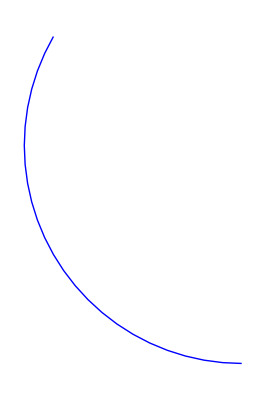

```mathematica
Graphics[{Blue,Circle[{0,0},0.03,{270Degree,150Degree}]}]
```

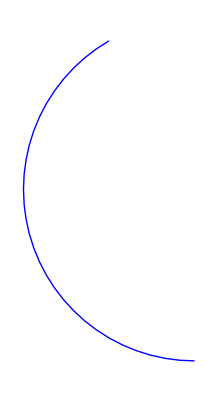

### figures

```mathematica
Graphics3D[{Black,Text[Style[O,14],{-0.05,-0.05,-0.05}],
                       Red,Arrow[{{0,0,0},{1,0,0}}],Text[Style[x,12],{1.05,0,0}],
                       Blue,Arrow[{{0,0,0},{0,1,0}}],Text[Style[y,12],{0,1.09,0}],
                       Magenta,Arrow[{{0,0,0},{0,0,1}}],Text[Style[z,12],{0,0,1.05}],
                        Yellow,Cuboid[{0,0,0},{0.2,0.4,0.6}]},PlotRange->{{-1,1},{-1,1},{-1,1}}
                           ,Boxed->False]
```

-Graphics3D-

-Graphics-

-Graphics-

-Graphics-

```mathematica
Graphics3D[{Red,Sphere[{0,0,0},1],Green,Sphere[{0,0,1},1.25],Blue,Sphere[{0,1,0.5},1.5],Cyan,Sphere[{1,0,0},1.8]}]
```

-Graphics3D-

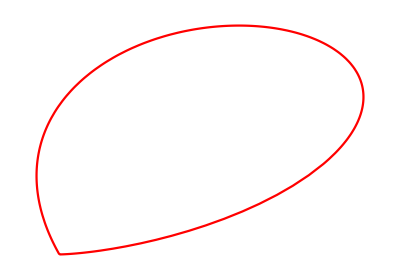

```mathematica
PolarPlot[0.1Sin[t^2],{t,0,√π},PlotStyle->{Red},Axes->False,AspectRatio->.7]
```

z

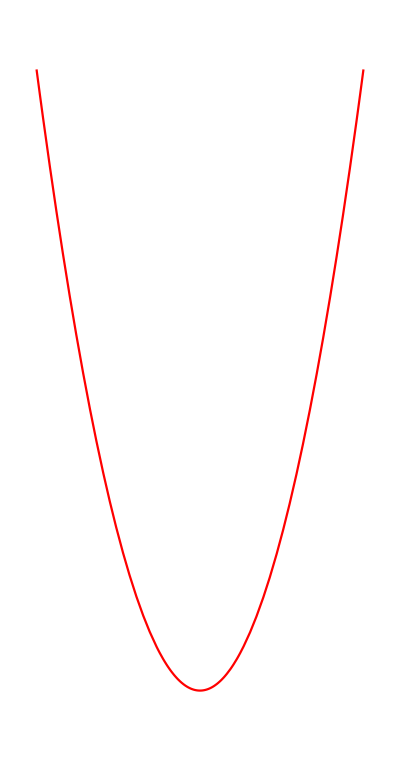

```mathematica
Plot[x^2,{x,-0.02π,0.02π},PlotStyle->Red,Axes->False,AspectRatio->1.9]
```

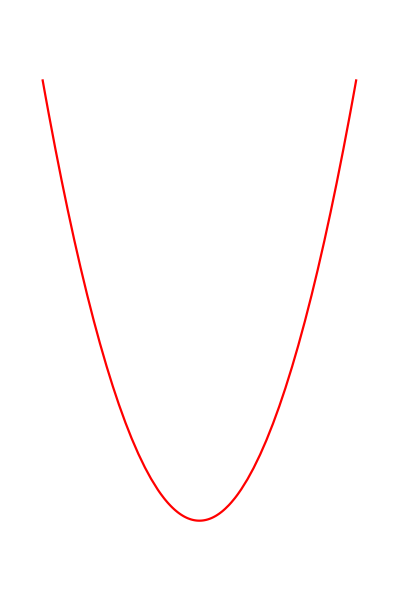

-Graphics-

```mathematica
θ3=k/m2(1+2 m2/m1);
θ=θ3;
A={{2k- m1 θ,-k,-k},{-k,k-m2 θ,0},{-k,0,k-m2 θ}};
xv={x1,x2,x3};
Solve[A.xv==0,xv]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x2→-(m1 x1)/(2 m2),x3→-(m1 x1)/(2 m2)}}

还有，应体会上式的意义：用于

平动系中观察到的矢量的变化，不是表示为平动系的坐标基矢的线性组合，

而是表示为本体系的坐标基矢的线性组合。

例题 9.2.03

飞盘被以水平投掷到空中，飞盘除了绕垂直于飞盘平面的对称轴旋转之外，

飞盘面还会偏离水平上下摆动。试证明摆动角速度是自旋速度的两倍。

-Graphics-

解：

三个主惯量：I_3=2 I_1=2 I_2=1/2 m R^2

接下去我们可以类似证明：描述刚体有限的定点运动的正交矩阵 𝒜 ，也与基点的选择无关。

此性质与“角速度与基点的选择无关”性质的最大区别在于，这里是有限的定点运动。

如图：
O 为空间系 Σ 原点
(O^)_1 和 O_2 为刚体上两点
分别选 O_1^ 和 O_2 作为基点
刚体除了相对于 O^ 平动
还以 O_1^ 或 O_2^为基点
       做 定点运动^。-Graphics-

以 O_1 点作为基点建立本体系 Σ_1 时，有

(r⃗)_1=[ (e⃗)_1^(1),(e⃗)_2^(1),(e⃗)_3^(1)][x_1^(1)
x_3^(1)
x_3^(1)]      记为矩阵形式：  (r⃗)_1=(e⃗)^((1) T)(x⃗)^(1)

其中 (e⃗)_1^(1),(e⃗)_2^(1),(e⃗)_3^(1)为本体系 Σ_1 系三个直角基矢量，x_i^(1) 为 (r⃗)_1 在 Σ_1 系的坐标

r⃗=(R⃗)_1+(r⃗)_1=(R⃗)_1+(e⃗)^((1) T)(x⃗)^(1)= (R⃗)_1+(e⃗)^T 𝒜_1^T(x⃗)^(1)          (†)

其中 𝒜_1 为描述 (e⃗)^(1)和 e⃗ 之间变换的矩阵，即为表征绕 O_1 定点运动的正交矩阵

(e⃗)^(1)=[(e⃗)_1^(1)
(e⃗)_2^(1)
(e⃗)_3^(1)]=𝒜_1 e⃗=𝒜_1[(e⃗)_1^
(e⃗)_2^
(e⃗)_3^]     或       (e⃗)^((1)T)=(e⃗)^T 𝒜_1^T

类似地：有

r⃗=(R⃗)_2+(r⃗)_2=(R⃗)_2+(e⃗)^((2) T)(x⃗)^(2)= (R⃗)_2+(e⃗)^T 𝒜_2^T(x⃗)^(2)              (‡)

其中    (e⃗)_1^(2),(e⃗)_2^(2),(e⃗)_3^(2)为 Σ_2 系三个直角基矢量，x_i^(2) 为 (r⃗)_2 在 Σ_2 系的坐标

𝒜_2 为描述 (e⃗)^(2)和 e⃗ 之间变换的矩阵，即为表征绕 O_2 定点运动的正交矩阵

式  (‡) -式 (†)   得：

R⃗= (R⃗)_2- (R⃗)_1=(e⃗)^T 𝒜_1^T(x⃗)^(1)-(e⃗)^T 𝒜_2^T(x⃗)^(2)                                                                            (#)

但是，R⃗=(r⃗)_1-(r⃗)_2，在 Σ_1 系，

R⃗=(e⃗)^((1) T)[(x⃗)^(1)-(x⃗)^(2)]=(e⃗)^T 𝒜_1^T[(x⃗)^(1)-(x⃗)^(2)]=(e⃗)^T 𝒜_1^T(x⃗)^(1)-(e⃗)^T 𝒜_1^T(x⃗)^(2)             (§)

比较 (#)和 (§) 两式，得：(e⃗)^T 𝒜_2^T(x⃗)^(2)=(e⃗)^T 𝒜_1^T(x⃗)^(2)    ⟹    𝒜_2^T=𝒜_1^T

其中利用了  (x⃗)^(2) 是任意的。

所以，描述刚体定点运动的正交矩阵 𝒜 与基点的选取无关。

对无穷小定点运动，其矢量表示 ⅆ Ω⃗  自然也与基点的选择无关

注：上一小节的思考题表明当基点确定时，矩阵𝒜 与刚体上的质点无关。

思考：基点是定点运动中不动的那个点，为什么还可以有不同选择？本节的两个唯一性的意义何在？

刚体运动，总可以看成刚体上任意一点平动（平动系相对于空间系）和绕这一点的定点运动

本节的意思是：随意选取平动坐标系的原点，描述刚体定点运动的瞬时角速度、正交矩阵都相同。

选取不同基点，对运动描述的差异，全归结到相对容易处理的刚体平动中。

在无外力矩的条件下，Euler 动力学方程

{I_1(ω̇)_1-ω_2 ω_3(I_2-I_3)=0
I_2(ω̇)_2-ω_3 ω_1(I_3-I_1)=0
I_3(ω̇)_3-ω_1 ω_2(I_1-I_2)=0

化为

{(L̇)_1=(I_2-I_3)/(I_2 I_3)L_2 L_3
(L̇)_2=(I_3-I_1)/(I_3 I_1)L_3 L_1
(L̇)_3=(I_1-I_2)/(I_1 I_2)L_1 L_2

在平动系上看，无外力矩，角动量守恒。

角动量方向始终沿紫色箭号方向，大小等于球半径。

这些要求就确定了刚体惯性椭球的取向，从而也就确定了刚体的取向。

就是：要转动惯性椭球，使得

从基点（原点）到椭球面与球面的交线上的一点

的矢量方向沿着表示角动量方向的紫色箭号方向。

而转动惯性椭球就是转动刚体。

因为我们这里仅仅用它来讨论绕主轴转动的稳定性问题，因此我们没有转动椭球。

而是反过来理解为主轴方向不变，角动量矢量末端在椭球面与球面的交线上移动。

为此我们仅把椭球面与球面的交线画出来。

从球增大过程的动态图可见，沿最大和最小惯量的主轴方向，交线是一个小圆。

角动量矢量末端在交线上移动（实际上是惯性椭球在转角动量方向不转），因而转动是稳定的。

而沿主惯量为中间值的主轴方向，椭球面与球面的交线不再是条闭合曲线，

表明这时惯量椭球的转动不再围绕着该主轴方向的转动，因而转动是不稳定的。

```mathematica
Graphics3D[{Yellow,Opacity[0.5],Cuboid[{0.5,0,0},{1.5,2.5,3}],{Red,Arrow[{{0.5,0,0},{3,0,0}}]},
                     {Green,Arrow[{{0.5,0,0},{0.5,4.5,0}}]},{Blue,Arrow[{{0.5,0,0},{0.5,0,4}}]},
                      {Red,Sphere[{1.5,0,0},0.1]},{Green,Sphere[{0.5,2.5,0},0.1]},{Blue,Sphere[{.5,0,3},0.1]},
                       {Red,FontSize->25,Text[x,{3.2,0,0}]},{Green,FontSize->25,Text[y,{0.5,4.7,0}]},
                        {Blue,FontSize->25,Text[z,{0.5,0,4.2}]}, {Black,FontSize->25,Text[O,{0,0,0}]}
                     },Boxed->False]
```

-Graphics3D-

```mathematica
Graphics3D[{Black,Text[Style[O,Large,FontWeight->Bold],{-0.1,-0.1,-0.15}],Opacity[0.59],Sphere[{0,0,0},0.04],
 Red,Arrow[{{0,0,0},{1,0,0}}],Text[Style[x,Large,FontWeight->Bold],{1.15,0,0}],Sphere[{0.2,0,0},0.03],
 Blue,Arrow[{{0,0,0},{0,1,0}}],Text[Style[y,Large,FontWeight->Bold],{0,1.15,0}],Sphere[{0,0.5,0},0.035],
 Magenta,Arrow[{{0,0,0},{0,0,1}}],Text[Style[z,Large,FontWeight->Bold],{0,0,1.2}],Sphere[{0,0,0.7},0.03],
                        Yellow,Cuboid[{0,0,0},{0.2,0.5,0.7}]},PlotRange->{{-1,1},{-1,1},{-1,1}}
                           ,Boxed->False]
```

-Graphics3D-